# A. Offspring control (Mike version)

## Recursions (written as in appendix, generic loci order) [Enter]

### Haploid selection

We start with haploid selection, which occurs in sperm/pollen only. We assume male sperm/pollen compete for eggs, and that the allele at the autosomal locus determines their competitive ability (with relative fitnesses wA and wa). After selection on male gametes/pollen the frequencies of gametes in each sex are

```mathematica
(*mean fitness of female gametes*)
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);

(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;

(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;

(*mean fitness of male gametes*)
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);

(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;

(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
```

Check that frequencies sum to one in each sex after haploid selection:

```mathematica
1==XAMms+XaMms+YAMms+YaMms+XAmms+Xamms+YAmms+Yamms//Factor (*male gametes*)
1==XAMfs+XaMfs+XAmfs+Xamfs+YAMfs+YaMfs+YAmfs+Yamfs//Factor (*eggs*)
```

True

True

### Random mating

After random mating, the frequencies of the diploid genotypes are

```mathematica
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);

(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);

(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);

(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);

(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);

(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);

(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);

(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);

(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);

(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);
```

Check that they sum to one

```mathematica
1==XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMXAMmale+XAMXaMmale+XaMXaMmale+
XAMYAMmale+XAMYaMmale+XaMYAMmale+XaMYaMmale+
XAMYAMfemale+XAMYaMfemale+XaMYAMfemale+XaMYaMfemale+
YAMYAMmale+YAMYaMmale+YaMYaMmale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmXAMmale+XAmXaMmale+XAMXammale+XamXaMmale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAmYAMmale+XAmYaMmale+XamYAMmale+XamYaMmale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
XAMYAmmale+XAMYammale+XaMYAmmale+XaMYammale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
YAmYAMmale+YAmYaMmale+YamYAMmale+YamYaMmale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmXAmmale+XAmXammale+XamXammale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
XAmYAmmale+XAmYammale+XamYAmmale+XamYammale+
YAmYAmfemale+YAmYamfemale+YamYamfemale+
YAmYAmmale+YAmYammale+YamYammale//Factor
```

True

### Diploid selection

We next model selection in diploids, which can differ among the sexes. Let FAA, FAa, and Faa be the relative fitnesses of females homozygous for allele A, heterozygous, or homozygous for allele a at the autosomal locus. Similarly we use MAA, MAa, and Maa in males. Frequencies after selection in diploid are indicated by appending an s to the name.

```mathematica
(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;
```

Frequency of males after diplod selection should sum to 1

```mathematica
1==XAMXAMmales+XAMXaMmales+XaMXaMmales+
XAMYAMmales+XAMYaMmales+XaMYAMmales+XaMYaMmales+
YAMYAMmales+YAMYaMmales+YaMYaMmales+
XAmXAMmales+XAmXaMmales+XAMXammales+XamXaMmales+
XAmYAMmales+XAmYaMmales+XamYAMmales+XamYaMmales+
XAMYAmmales+XAMYammales+XaMYAmmales+XaMYammales+
YAmYAMmales+YAmYaMmales+YamYAMmales+YamYaMmales+
XAmXAmmales+XAmXammales+XamXammales+
XAmYAmmales+XAmYammales+XamYAmmales+XamYammales+
YAmYAmmales+YAmYammales+YamYammales//Factor
```

True

```mathematica
(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;
```

Frequency of females after diplod selection should sum to 1

```mathematica
1==XAMXAMfemales+XAMXaMfemales+XaMXaMfemales+
XAMYAMfemales+XAMYaMfemales+XaMYAMfemales+XaMYaMfemales+
YAMYAMfemales+YAMYaMfemales+YaMYaMfemales+
XAmXAMfemales+XAmXaMfemales+XAMXamfemales+XamXaMfemales+
XAmYAMfemales+XAmYaMfemales+XamYAMfemales+XamYaMfemales+
XAMYAmfemales+XAMYamfemales+XaMYAmfemales+XaMYamfemales+
YAmYAMfemales+YAmYaMfemales+YamYAMfemales+YamYaMfemales+
XAmXAmfemales+XAmXamfemales+XamXamfemales+
XAmYAmfemales+XAmYamfemales+XamYAmfemales+XamYamfemales+
YAmYAmfemales+YAmYamfemales+YamYamfemales//Factor
```

True

### Meiosis

Translate into new notation:

first two letters refer to SDR locus genotype, then numbers ij giving A and M locus genotype where 
1-AM
2-aM
3-Am
4-am
then m or f indicating male or female
then s to indicate that these are frequencies after selection
e.g., xy41ms is a male with genotype X-a-m Y-A-M. 
Where i and j are interchangable (in YY and XX individuals) the lowest number is given first.

```mathematica
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;
```

```mathematica
xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
```

First, we consider female gametes

```mathematica
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-Rf)+xx23fs*Rf)αf+
xy11fs/2+(xy12fs(1-rMMf)+xy21fs (rMMf))αf+
(xy13fs(1-χf)+xy31fs (χf))/2+
xy14fs *αf+
(xy14fs (-(Rf+rMmf+χf))+ 
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-Rf)+xx14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(rMMf)+xy21fs(1-rMMf))(1-αf)+
(xy24fs (1-χf)+xy42fs (χf))/2+
xy23fs*(1-αf)+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-Rf)+Rf*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))αf+
(xy13fs(χf)+xy31fs(1-χf))/2+
xy32fs *αf+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-Rf)+xx23fs*Rf+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(1-αf)+
(xy24fs(χf)+xy42fs(1-χf))/2+
xy41fs*(1-αf)+
(xy14fs(rMmf+χf-Rf)+
xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-Rf)+yy23fs*Rf)αf+
xy11fs/2+(xy12fs(rMMf)+xy21fs (1-rMMf))(αf)+
(xy13fs(χf)+xy31fs (1-χf))/2+
xy41fs*αf+
(xy14fs (rMmf+χf-Rf)+
 xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-Rf)+yy14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(1-rMMf)+xy21fs(rMMf))(1-αf)+
(xy24fs (χf)+xy42fs (1-χf))/2+
xy32fs*(1-αf)+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-Rf)+Rf*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(αf)+
(xy13fs(1-χf)+xy31fs(χf))/2+
xy23fs*αf+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-Rf)+yy23fs*Rf+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))(1-αf)+
(xy24fs(1-χf)+xy42fs(χf))/2+
xy14fs*(1-αf)+
(xy14fs(-(Rf+rMmf+χf))+
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))(1-αf)/2;
```

```mathematica
Factor[nextXAMf+nextXaMf+nextXAmf+nextXamf+nextYAMf+nextYaMf+nextYAmf+nextYamf]
```

1

We can consider male gametes similarly

```mathematica
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-Rm)+xx23ms*Rm)αm+
xy11ms/2+(xy12ms(1-rMMm)+xy21ms (rMMm))αm+
(xy13ms(1-χm)+xy31ms (χm))/2+
xy14ms *αm+
(xy14ms (-(Rm+rMmm+χm))+ 
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-Rm)+xx14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(rMMm)+xy21ms(1-rMMm))(1-αm)+
(xy24ms (1-χm)+xy42ms (χm))/2+
xy23ms*(1-αm)+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-Rm)+Rm*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))αm+
(xy13ms(χm)+xy31ms(1-χm))/2+
xy32ms *αm+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-Rm)+xx23ms*Rm+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(1-αm)+
(xy24ms(χm)+xy42ms(1-χm))/2+
xy41ms*(1-αm)+
(xy14ms(rMmm+χm-Rm)+
xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-Rm)+yy23ms*Rm)αm+
xy11ms/2+(xy12ms(rMMm)+xy21ms (1-rMMm))(αm)+
(xy13ms(χm)+xy31ms (1-χm))/2+
xy41ms*αm+
(xy14ms (rMmm+χm-Rm)+
 xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-Rm)+yy14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(1-rMMm)+xy21ms(rMMm))(1-αm)+
(xy24ms (χm)+xy42ms (1-χm))/2+
xy32ms*(1-αm)+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-Rm)+Rm*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(αm)+
(xy13ms(1-χm)+xy31ms(χm))/2+
xy23ms*αm+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-Rm)+yy23ms*Rm+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))(1-αm)+
(xy24ms(1-χm)+xy42ms(χm))/2+
xy14ms*(1-αm)+
(xy14ms(-(Rm+rMmm+χm))+
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))(1-αm)/2;
```

```mathematica
Factor[nextXAMm+nextXaMm+nextXAmm+nextXamm+nextYAMm+nextYaMm+nextYAmm+nextYamm]
```

1

Generally want to at least assume that recombination is not affected by M or sex

```mathematica
SUBSR={
Rm->R,
Rf->R,
rMMm->r,
rMmm->r,
rmmm->r,
rMMf->r,
rMmf->r,
rmmf->r,
χm->χ,
χf->χ
};
```

Often also want to assume the following about k:

```mathematica
SUBS={
Rm->R,
Rf->R,
rMMm->r,
rMmm->r,
rmmm->r,
rMMf->r,
rMmf->r,
rmmf->r,
χm->χ,
χf->χ,
kXX->1,
kXY->0,
kYY->0,
kMmXX->k,
kMmXY->k,
kMmYY->k,
kmm->k,
kmm->k,
kmm->k
};
```

## Complete linkage case

### Equilibrium [ENTER]

Working in allele frequencies rather than haplotype frequencies:

```mathematica
subequil={
XAMf->pXf,
XaMf->(1-pXf),
YAMf->0,
YaMf->0,
XAMm->pXm(1-freqYm),
XaMm->(1-pXm)(1-freqYm),
YAMm->pYm*freqYm,
YaMm->(1-pYm)*freqYm,
XAmf->0,
Xamf->0,
XAmm->0,
Xamm->0,
YAmm->0,
Yamm->0,
YAmf->0,
Yamf->0
};
```

```mathematica
equilA0={pXf->(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm->-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),pYm->0,freqYm->(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))};
```

```mathematica
equilAp0={pXf->(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm->(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),pYm->1,freqYm->(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))};
```

```mathematica
equilB0={pXf->1,pXm->1,pYm->0,freqYm->1-αm};
```

```mathematica
equilBp0={pXf->0,pXm->0,pYm->1,freqYm->αm};
```

```mathematica
equilC0={pXf->(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),pXm->(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),pYm->(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYm->(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))};
```

Factor[differenceEqs /. r -> 0 /. {equilA0, equilAp0, equilB0, equilBp0, equilC0}]

{{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}

To be relevant, this last equilibrium equilC0 requires that the numerators of the frequency of A and a in females are both positive or both negative (they share the same denominator, which is the sum of the numerators):

```mathematica
{pXf,1-pXf}/.equilC0//Factor
```

{(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm),(wAf (-2 MAa wam+MAA wAm+2 MAa wam αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm)}

Hence, either 2(1-αm) MAa wam > MAA wAm and 2 αm MAa wAm > Maa wam (akin to heterozygous advantage without pollen selection) or 2(1-αm) MAa wam < MAA wAm and 2 αm MAa wAm < Maa wam (akin to heterozygous disadvantage) otherwise pXf won’t lie between 0 and 1.

equilC0 will be shown later to not be internally stable when it exists, so this equilibrium can be ignored when examining the evolution of recombination.

The next order terms in the recombination rate, r (used in the weak selection approximations to assess the effect of r):

```mathematica
equilA1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))^2,pXmsm->(2 FAa MAa r αm (-Faa Maa^2 waf^2 wam^2 (-1+αf)+wAf αf (4 FAA MAa^2 wAf wAm^2 αm^2+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)^2)) ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))^2,pYmsm->(2 MAa r wam αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r (-1+2 αm) (-(Maa MAa wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))+(MAa wam wAm αm (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (-Maa wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (Maa MAA+4 MAa^2 (-1+αm) αm)-1/wam(FAa^2 (Maa waf^2 (-1+αf)^2+wAf αf (-2 MAa waf (-1+αf)+MAA wAf αf)) (Maa wam+2 MAa wAm αm)^2+2 FAa (Maa wam+2 MAa wAm αm) (Faa Maa waf wam (MAa waf (-1+αf)-MAA wAf αf)-2 FAA MAa wAf wAm (MAa wAf αf+Maa (waf-waf αf)) αm)+Maa (Faa^2 Maa MAA waf^2 wam^2+4 Faa FAA MAa^2 waf wAf wam wAm αm+4 FAA^2 MAa^2 wAf^2 wAm^2 αm^2))))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))^2};
```

```mathematica
equilAp1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm))^2 (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pXmsm->(2 FAa MAa r (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (wAf αf (FAA MAA^2 wAf wAm^2+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))^2)-4 Faa MAa^2 waf^2 wam^2 (-1+αf) (-1+αm)^2) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pYmsm->-(2 MAa r wAm (-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (-1+αm))/(-2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (-Maa wam+2 MAa wAm αm)+FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r ((FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) αm+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAA MAA wAf wAm (-Maa wam+MAa wAm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf-MAa (waf wAm (-1+αf)+wAf wam αf)) (-MAA wAm+2 MAa wam (-1+αm))+2 Faa MAa waf wam (MAa wam-MAA wAm) (-1+αm)) (-1+αm) (2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))-(MAa MAA wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-1+2 αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))))/(FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm)))^2};
```

```mathematica
equilB1={pXfsm->-(2 FAa MAa r wAf wam (-1+αf) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pXmsm->(2 MAa r wAm (FAA wAf+FAa waf (-1+αf)) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pYmsm->-(2 MAa r wam αm)/(MAA wAm+2 MAa wam (-1+αm)),freqYmsm->r (-1+2 αm-(MAA wAm αm (-1+2 αm))/(MAA wAm+2 MAa wam (-1+αm))+(FAa Maa waf wam (-1+αf) (-1+αm) (-1+2 αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))};
```

```mathematica
equilBp1={pXfsm->-(2 FAa MAa r waf wAm αf αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pXmsm->-(2 MAa r wam (Faa waf-FAa wAf αf) αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pYmsm->(2 MAa r wAm (-1+αm))/(-Maa wam+2 MAa wAm αm),freqYmsm->r αm (-1+2 αm) ((FAa MAA wAf wAm αf)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm))+(-Maa wam+2 MAa wAm)/(Maa wam-2 MAa wAm αm))};
```

### Equilibrium Derivation

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following four equations are zero

```mathematica
differenceEqs={
nextXAMf-XAMf,
nextXAMm-XAMm,
nextYAMm-YAMm,
nextYAMm+nextYaMm-(YAMm+YaMm)
}/.SUBS/.subequil;
```

```mathematica
sub1=Flatten[Solve[differenceEqs[[3]]==0,pXf]]//Factor
```

{pXf→(2 pYm waf (-freqYm Maa wam+freqYm Maa pYm wam-freqYm MAa pYm wAm+MAa wAm αm-MAa r wAm αm))/(-2 freqYm Maa pYm waf wam+2 freqYm Maa pYm^2 waf wam+2 freqYm MAa pYm wAf wam-2 freqYm MAa pYm^2 wAf wam-2 freqYm MAa pYm^2 waf wAm-MAA pYm wAf wAm+2 freqYm MAA pYm^2 wAf wAm-2 MAa r wAf wam αm+2 MAa pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pYm r waf wAm αm)}

```mathematica
differenceEqs[[2]]/.sub1//Factor
```

(-Maa MAA pXm pYm wam wAm+freqYm Maa MAA pXm pYm wam wAm+freqYm Maa MAA pYm^2 wam wAm+Maa MAA pXm pYm^2 wam wAm-freqYm Maa MAA pXm pYm^2 wam wAm-freqYm Maa MAA pYm^3 wam wAm-MAa MAA pXm pYm^2 wAm^2+freqYm MAa MAA pXm pYm^2 wAm^2+freqYm MAa MAA pYm^3 wAm^2+2 freqYm Maa MAa pYm wam^2 αm-4 freqYm Maa MAa pYm^2 wam^2 αm+2 freqYm Maa MAa pYm^3 wam^2 αm-2 Maa MAa pXm r wam^2 αm+2 freqYm Maa MAa pXm r wam^2 αm-2 freqYm Maa MAa pYm r wam^2 αm+4 Maa MAa pXm pYm r wam^2 αm-4 freqYm Maa MAa pXm pYm r wam^2 αm+4 freqYm Maa MAa pYm^2 r wam^2 αm-2 Maa MAa pXm pYm^2 r wam^2 αm+2 freqYm Maa MAa pXm pYm^2 r wam^2 αm-2 freqYm Maa MAa pYm^3 r wam^2 αm+2 MAa^2 pXm pYm wam wAm αm-2 freqYm MAa^2 pXm pYm wam wAm αm+2 freqYm MAa^2 pYm^2 wam wAm αm-2 MAa^2 pXm pYm^2 wam wAm αm+2 freqYm MAa^2 pXm pYm^2 wam wAm αm-2 freqYm MAa^2 pYm^3 wam wAm αm-4 MAa^2 pXm pYm r wam wAm αm+4 freqYm MAa^2 pXm pYm r wam wAm αm-4 freqYm MAa^2 pYm^2 r wam wAm αm+4 MAa^2 pXm pYm^2 r wam wAm αm-4 freqYm MAa^2 pXm pYm^2 r wam wAm αm+4 freqYm MAa^2 pYm^3 r wam wAm αm-MAa MAA pYm^2 wAm^2 αm+2 MAa MAA pXm pYm^2 wAm^2 αm-2 freqYm MAa MAA pXm pYm^2 wAm^2 αm+2 MAa MAA pYm^2 r wAm^2 αm-2 MAa MAA pXm pYm^2 r wAm^2 αm+2 freqYm MAa MAA pXm pYm^2 r wAm^2 αm-2 freqYm MAa MAA pYm^3 r wAm^2 αm-2 MAa^2 pYm wam wAm αm^2+2 MAa^2 pYm^2 wam wAm αm^2+4 MAa^2 pYm r wam wAm αm^2-4 MAa^2 pYm^2 r wam wAm αm^2)/(Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+MAa MAA pYm^2 wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-2 MAa^2 pYm wam wAm αm+2 MAa^2 pYm^2 wam wAm αm+4 MAa^2 pYm r wam wAm αm-4 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 wAm^2 αm+2 MAa MAA pYm^2 r wAm^2 αm)

```mathematica
sub2=Flatten[Solve[Factor[differenceEqs[[2]]/.sub1]==0,pXm]]//Factor
```

{pXm→-(pYm (-freqYm Maa MAA pYm wam wAm+freqYm Maa MAA pYm^2 wam wAm-freqYm MAa MAA pYm^2 wAm^2-2 freqYm Maa MAa wam^2 αm+4 freqYm Maa MAa pYm wam^2 αm-2 freqYm Maa MAa pYm^2 wam^2 αm+2 freqYm Maa MAa r wam^2 αm-4 freqYm Maa MAa pYm r wam^2 αm+2 freqYm Maa MAa pYm^2 r wam^2 αm-2 freqYm MAa^2 pYm wam wAm αm+2 freqYm MAa^2 pYm^2 wam wAm αm+4 freqYm MAa^2 pYm r wam wAm αm-4 freqYm MAa^2 pYm^2 r wam wAm αm+MAa MAA pYm wAm^2 αm-2 MAa MAA pYm r wAm^2 αm+2 freqYm MAa MAA pYm^2 r wAm^2 αm+2 MAa^2 wam wAm αm^2-2 MAa^2 pYm wam wAm αm^2-4 MAa^2 r wam wAm αm^2+4 MAa^2 pYm r wam wAm αm^2))/((-1+freqYm) (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-MAa MAA pYm^2 wAm^2-2 Maa MAa r wam^2 αm+4 Maa MAa pYm r wam^2 αm-2 Maa MAa pYm^2 r wam^2 αm+2 MAa^2 pYm wam wAm αm-2 MAa^2 pYm^2 wam wAm αm-4 MAa^2 pYm r wam wAm αm+4 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm))}

```mathematica
differenceEqs[[4]]/.sub1/.sub2//Factor
```

(2 freqYm Maa MAa pYm wam^2-4 freqYm Maa MAa pYm^2 wam^2+2 freqYm Maa MAa pYm^3 wam^2-4 freqYm Maa MAa pYm r wam^2+8 freqYm Maa MAa pYm^2 r wam^2-4 freqYm Maa MAa pYm^3 r wam^2+Maa MAA pYm wam wAm-2 freqYm Maa MAA pYm wam wAm+4 freqYm MAa^2 pYm^2 wam wAm-Maa MAA pYm^2 wam wAm+2 freqYm Maa MAA pYm^2 wam wAm-4 freqYm MAa^2 pYm^3 wam wAm-8 freqYm MAa^2 pYm^2 r wam wAm+8 freqYm MAa^2 pYm^3 r wam wAm-2 freqYm MAa MAA pYm^2 wAm^2+2 freqYm MAa MAA pYm^3 wAm^2+2 MAa MAA pYm^2 r wAm^2-4 freqYm MAa MAA pYm^3 r wAm^2-4 freqYm Maa MAa pYm wam^2 αm+8 freqYm Maa MAa pYm^2 wam^2 αm-4 freqYm Maa MAa pYm^3 wam^2 αm+2 Maa MAa r wam^2 αm-4 freqYm Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+16 freqYm Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-20 freqYm Maa MAa pYm^2 r wam^2 αm+8 freqYm Maa MAa pYm^3 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 freqYm MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm-12 freqYm MAa^2 pYm^2 wam wAm αm+8 freqYm MAa^2 pYm^3 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 freqYm MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm+24 freqYm MAa^2 pYm^2 r wam wAm αm-16 freqYm MAa^2 pYm^3 r wam wAm αm+4 freqYm MAa MAA pYm^2 wAm^2 αm-4 freqYm MAa MAA pYm^3 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm-4 freqYm MAa MAA pYm^2 r wAm^2 αm+8 freqYm MAa MAA pYm^3 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2)/(2 (Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+MAa MAA pYm^2 wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-2 MAa^2 pYm wam wAm αm+2 MAa^2 pYm^2 wam wAm αm+4 MAa^2 pYm r wam wAm αm-4 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 wAm^2 αm+2 MAa MAA pYm^2 r wAm^2 αm))

```mathematica
sub3=Flatten[Solve[Factor[differenceEqs[[4]]/.sub1/.sub2]==0,freqYm]]//Factor
```

{freqYm→-(Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2)/(2 (Maa MAa pYm wam^2-2 Maa MAa pYm^2 wam^2+Maa MAa pYm^3 wam^2-2 Maa MAa pYm r wam^2+4 Maa MAa pYm^2 r wam^2-2 Maa MAa pYm^3 r wam^2-Maa MAA pYm wam wAm+2 MAa^2 pYm^2 wam wAm+Maa MAA pYm^2 wam wAm-2 MAa^2 pYm^3 wam wAm-4 MAa^2 pYm^2 r wam wAm+4 MAa^2 pYm^3 r wam wAm-MAa MAA pYm^2 wAm^2+MAa MAA pYm^3 wAm^2-2 MAa MAA pYm^3 r wAm^2-2 Maa MAa pYm wam^2 αm+4 Maa MAa pYm^2 wam^2 αm-2 Maa MAa pYm^3 wam^2 αm-2 Maa MAa r wam^2 αm+8 Maa MAa pYm r wam^2 αm-10 Maa MAa pYm^2 r wam^2 αm+4 Maa MAa pYm^3 r wam^2 αm+2 MAa^2 pYm wam wAm αm-6 MAa^2 pYm^2 wam wAm αm+4 MAa^2 pYm^3 wam wAm αm-4 MAa^2 pYm r wam wAm αm+12 MAa^2 pYm^2 r wam wAm αm-8 MAa^2 pYm^3 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^3 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa MAA pYm^3 r wAm^2 αm))}

```mathematica
equilsol=Numerator[Factor[differenceEqs[[1]]/.sub1/.sub2/.sub3]]
```

-(-1+pYm) pYm (2 FAa Maa^3 MAa pYm^2 waf wam^5-4 Faa Maa^2 MAa^2 pYm^2 waf wam^5-6 FAa Maa^3 MAa pYm^3 waf wam^5+12 Faa Maa^2 MAa^2 pYm^3 waf wam^5+«1951»+448 FAa MAa^4 pYm^3 r^3 waf wam^2 wAm^3 αf αm^4-512 FAa MAa^4 pYm^4 r^3 waf wam^2 wAm^3 αf αm^4+256 FAa MAa^4 pYm^5 r^3 waf wam^2 wAm^3 αf αm^4)

In the following we assume r=0 to leading order to determine the equilibrium in the case where the A locus resides in the SDR:

```mathematica
equilsol/.r->0//Factor
```

(-1+pYm)^3 pYm^3 (-2 MAa wam+MAA wAm+2 MAa wam αm) (Maa wam-2 MAa wAm αm) (FAa Maa^2 waf wam^3-2 Faa Maa MAa waf wam^3-FAa Maa^2 pYm waf wam^3+2 Faa Maa MAa pYm waf wam^3+Faa Maa MAA waf wam^2 wAm+2 FAa Maa MAa pYm waf wam^2 wAm-4 Faa MAa^2 pYm waf wam^2 wAm-Faa Maa MAA pYm waf wam^2 wAm+FAa Maa MAA pYm waf wam wAm^2+2 Faa MAa MAA pYm waf wam wAm^2-FAA Maa MAA pYm wAf wam wAm^2-FAa Maa^2 waf wam^3 αf+FAa Maa^2 pYm waf wam^3 αf+2 FAa Maa MAa wAf wam^3 αf-2 FAa Maa MAa pYm wAf wam^3 αf-2 FAa Maa MAa pYm waf wam^2 wAm αf-FAa Maa MAA wAf wam^2 wAm αf+4 FAa MAa^2 pYm wAf wam^2 wAm αf+FAa Maa MAA pYm wAf wam^2 wAm αf-FAa Maa MAA pYm waf wam wAm^2 αf-FAa MAA^2 pYm wAf wAm^3 αf+2 Faa Maa MAa waf wam^3 αm-2 Faa Maa MAa pYm waf wam^3 αm-2 FAa Maa MAa pYm waf wam^2 wAm αm+8 Faa MAa^2 pYm waf wam^2 wAm αm-2 FAA Maa MAa wAf wam^2 wAm αm+2 FAA Maa MAa pYm wAf wam^2 wAm αm-4 FAa MAa^2 pYm waf wam wAm^2 αm-2 Faa MAa MAA pYm waf wam wAm^2 αm-2 FAa MAa MAA pYm waf wAm^3 αm+2 FAA MAa MAA pYm wAf wAm^3 αm-2 FAa Maa MAa wAf wam^3 αf αm+2 FAa Maa MAa pYm wAf wam^3 αf αm+2 FAa Maa MAa pYm waf wam^2 wAm αf αm+4 FAa MAa^2 wAf wam^2 wAm αf αm-12 FAa MAa^2 pYm wAf wam^2 wAm αf αm+4 FAa MAa^2 pYm waf wam wAm^2 αf αm-2 FAa MAa MAA wAf wam wAm^2 αf αm+2 FAa MAa MAA pYm wAf wam wAm^2 αf αm+2 FAa MAa MAA pYm waf wAm^3 αf αm-4 Faa MAa^2 pYm waf wam^2 wAm αm^2-4 FAa MAa^2 waf wam wAm^2 αm^2+8 FAa MAa^2 pYm waf wam wAm^2 αm^2+4 FAA MAa^2 wAf wam wAm^2 αm^2-4 FAA MAa^2 pYm wAf wam wAm^2 αm^2-4 FAa MAa^2 wAf wam^2 wAm αf αm^2+8 FAa MAa^2 pYm wAf wam^2 wAm αf αm^2+4 FAa MAa^2 waf wam wAm^2 αf αm^2-8 FAa MAa^2 pYm waf wam wAm^2 αf αm^2)

```mathematica
equilsol2=Solve[%==0,pYm]//Simplify
```

{{pYm→0},{pYm→0},{pYm→0},{pYm→1},{pYm→1},{pYm→1},{pYm→(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))}}

In the following, we assume that pYm is either 0, 1, or the last of the above solutions.  When r=0 and pYm = 0 or 1, its safest to rederive the solution for {pXf, pXm, freqYm} (using the substitutions to define these goes astray because some of the intermediate steps are zero when r = 0 and pYm = 0 or 1).

First, consider cases where pYm=0.

With allele A fixed on Y (pYm=0), then {pXf, pXm, freqYm} equal:

```mathematica
Solve[(differenceEqs/.r->0/.pYm->1//Factor)=={0,0,0,0},{pXf,pXm,freqYm}]//Simplify
```

{{pXf→0,pXm→0,freqYm→αm},{pXf→1,pXm→1,freqYm→1/2},{pXf→(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm→(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),freqYm→(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))}}

The last of these has a polymorphism on the X chromosome; we’ll call this equilA0 (“0” because this is the leading order term in r...we could take additional order terms to get the linear approximation in r, etc.).  

The first of these {pXf→0,pXm→0,freqYm→αm} is also polymorphic (Y fixed on A and X fixed on a), which we’ll call equilB0.

Next, consider cases where pYm=0.

With allele A fixed on Y (pYm=0), then {pXf, pXm, freqYm} equal:

```mathematica
Solve[(differenceEqs/.r->0/.pYm->0//Factor)=={0,0,0,0},{pXf,pXm,freqYm}]//Simplify
```

{{pXf→0,pXm→0,freqYm→1/2},{pXf→1,pXm→1,freqYm→1-αm},{pXf→(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm→-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),freqYm→(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))}}

The last of these has a polymorphism on the X chromosome; we’ll call this equilAp0 (“p” for prime -- the alternate allele is fixed on the Y).  

The second of these {pXf→1,pXm→1,freqYm→1-αm} is also polymorphic (Y fixed on a and X fixed on A), which we’ll call equilBp0.

Finally, we have the equilibrium (which will turn out to not be stable) with freq(A) on Y = (wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))):

```mathematica
Factor[{pXf,pXm,pYm,freqYm}/.sub1/.sub2/.sub3/.r->0]/.Last[equilsol2]//Simplify
```

{(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))}

We’ll call this equilC.

Getting the next order in the recombination rate (these are needed during the derivation of the external stability conditions to ensure that all of the small terms not involving the modifier cancel):

(This takes a while...)

```mathematica
Factor[Normal[Series[differenceEqs/.pXf->pXf+pXfsm*sm/.pXm->pXm+pXmsm*sm/.pYm->pYm+pYmsm*sm/.freqYm->freqYm+freqYmsm*sm/.r->r*sm/.equilA0,{sm,0,1}]]]/.sm->1;
```

```mathematica
equilA1=Flatten[Simplify[Solve[%==0,{pXfsm,pXmsm,pYmsm,freqYmsm}]]]
```

{pXfsm→(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))^2,pXmsm→(2 FAa MAa r αm (-Faa Maa^2 waf^2 wam^2 (-1+αf)+wAf αf (4 FAA MAa^2 wAf wAm^2 αm^2+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)^2)) ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))^2,pYmsm→(2 MAa r wam αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm→(MAa r (-1+2 αm) (-(Maa MAa wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))+(MAa wam wAm αm (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (-Maa wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (Maa MAA+4 MAa^2 (-1+αm) αm)-1/wam(FAa^2 (Maa waf^2 (-1+αf)^2+wAf αf (-2 MAa waf (-1+αf)+MAA wAf αf)) (Maa wam+2 MAa wAm αm)^2+2 FAa (Maa wam+2 MAa wAm αm) (Faa Maa waf wam (MAa waf (-1+αf)-MAA wAf αf)-2 FAA MAa wAf wAm (MAa wAf αf+Maa (waf-waf αf)) αm)+Maa (Faa^2 Maa MAA waf^2 wam^2+4 Faa FAA MAa^2 waf wAf wam wAm αm+4 FAA^2 MAa^2 wAf^2 wAm^2 αm^2))))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))^2}

```mathematica
Factor[Normal[Series[differenceEqs/.pXf->pXf+pXfsm*sm/.pXm->pXm+pXmsm*sm/.pYm->pYm+pYmsm*sm/.freqYm->freqYm+freqYmsm*sm/.r->r*sm/.equilAp0,{sm,0,1}]]]/.sm->1;
```

```mathematica
equilAp1=Flatten[Simplify[Solve[%==0,{pXfsm,pXmsm,pYmsm,freqYmsm}]]]
```

{pXfsm→(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm))^2 (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pXmsm→(2 FAa MAa r (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (wAf αf (FAA MAA^2 wAf wAm^2+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))^2)-4 Faa MAa^2 waf^2 wam^2 (-1+αf) (-1+αm)^2) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pYmsm→-(2 MAa r wAm (-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (-1+αm))/(-2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (-Maa wam+2 MAa wAm αm)+FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm→(MAa r ((FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) αm+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAA MAA wAf wAm (-Maa wam+MAa wAm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf-MAa (waf wAm (-1+αf)+wAf wam αf)) (-MAA wAm+2 MAa wam (-1+αm))+2 Faa MAa waf wam (MAa wam-MAA wAm) (-1+αm)) (-1+αm) (2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))-(MAa MAA wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-1+2 αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))))/(FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm)))^2}

```mathematica
Factor[Normal[Series[differenceEqs/.pXf->pXf+pXfsm*sm/.pXm->pXm+pXmsm*sm/.pYm->pYm+pYmsm*sm/.freqYm->freqYm+freqYmsm*sm/.r->r*sm/.equilB0,{sm,0,1}]]]/.sm->1;
```

```mathematica
equilB1=Flatten[Simplify[Solve[%==0,{pXfsm,pXmsm,pYmsm,freqYmsm}]]]
```

{pXfsm→-(2 FAa MAa r wAf wam (-1+αf) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pXmsm→(2 MAa r wAm (FAA wAf+FAa waf (-1+αf)) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pYmsm→-(2 MAa r wam αm)/(MAA wAm+2 MAa wam (-1+αm)),freqYmsm→r (-1+2 αm-(MAA wAm αm (-1+2 αm))/(MAA wAm+2 MAa wam (-1+αm))+(FAa Maa waf wam (-1+αf) (-1+αm) (-1+2 αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))}

```mathematica
Factor[Normal[Series[differenceEqs/.pXf->pXf+pXfsm*sm/.pXm->pXm+pXmsm*sm/.pYm->pYm+pYmsm*sm/.freqYm->freqYm+freqYmsm*sm/.r->r*sm/.equilBp0,{sm,0,1}]]]/.sm->1;
```

```mathematica
equilBp1=Flatten[Simplify[Solve[%==0,{pXfsm,pXmsm,pYmsm,freqYmsm}]]]
```

{pXfsm→-(2 FAa MAa r waf wAm αf αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pXmsm→-(2 MAa r wam (Faa waf-FAa wAf αf) αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pYmsm→(2 MAa r wAm (-1+αm))/(-Maa wam+2 MAa wAm αm),freqYmsm→r αm (-1+2 αm) ((FAa MAA wAf wAm αf)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm))+(-Maa wam+2 MAa wAm)/(Maa wam-2 MAa wAm αm))}

### Validity and stability of polymorphic equilibrium (M fixed) - tight linkage

Assumptions used to simplify the results:

```mathematica
simpcond=Reduce[{0<MAA,0<MAa,0<Maa,0<FAA,0<FAa,0<Faa,0<wAf,0<waf,0<wAm,0<wam,0<αm<1,0<αf<1,0≤Rm≤1/2,0≤Rf≤1/2}];
```

We also consider only equilibria A, B, and C (i.e., with a fixed on Y).  The conditions required for equilibria A’ and B’ can be obtained by interchanging the alleles, A and a.

#### General [ENTER]

The local stability matrix with the M allele fixed:

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs={nextXAMf,nextXAMm/(nextXAMm+nextXaMm),nextYAMm/(nextYAMm+nextYaMm),nextYAMm+nextYaMm}/.SUBS/.subequil;
matIntFull=Transpose[{
D[eqs,pXf],
D[eqs,pXm],
D[eqs,pYm],
D[eqs,freqYm]
}]/.SUBS/.subequil//Factor;
```

The last column of matIntFull is full of zeros, corresponding to an eigenvalue of zero and indicating that the sex ratio in the system equilibrates immediately:

```mathematica
Transpose[matIntFull][[4]]
```

{0,0,0,0}

As a consequence, we drop the last row and column in matIntFull:

```mathematica
matIntFull=Table[matIntFull[[i,j]],{i,1,3},{j,1,3}];
```

From this we can derive the characteristic polynomial with r = 0:

```mathematica
charpolyIntFull=Det[(matIntFull/.r->0)-IdentityMatrix[3]*λ];
```

#### Equilibrium A (r ~ 0)

```mathematica
eq1=Factor[pXf/.equilA0]
```

(waf (Faa Maa waf wam-FAa Maa wAf wam αf-2 FAa MAa wAf wAm αf αm))/(Faa Maa waf^2 wam-FAa Maa waf wAf wam-2 FAa MAa waf wAf wAm αm+2 FAA MAa wAf^2 wAm αm)

```mathematica
eq2=Factor[pXm/.equilA0]
```

(2 MAa αm (-Faa Maa waf wam+FAa Maa wAf wam αf+2 FAa MAa wAf wAm αf αm))/(FAa Maa^2 waf wam-FAa Maa^2 waf wam αf-2 Faa Maa MAa waf wam αm+2 FAa Maa MAa waf wAm αm-2 FAA Maa MAa wAf wAm αm+2 FAa Maa MAa wAf wam αf αm-2 FAa Maa MAa waf wAm αf αm+4 FAa MAa^2 wAf wAm αf αm^2)

```mathematica
eq3=Factor[pYm/.equilA0]
```

0

We must have each of the following terms be positive for the equilibrium to be valid:

```mathematica
{{eq1,1-eq1},{eq2,1-eq2}}//Simplify
```

{{(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),(wAf (2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))},{-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),(Maa (2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))}}

```mathematica
Reduce[{0<eq1<1,0<eq2<1,simpcond},{FAA,Faa}]
```

(0≤Rf≤1/2&&MAA>0&&0≤Rm≤1/2&&wAf>0&&0<αm<1&&waf>0&&Maa>0&&MAa>0&&0<αf<1&&wam>0&&wAm>0&&FAa>0&&0<FAA<(FAa Maa waf wam-FAa Maa waf wam αf+2 FAa MAa waf wAm αm-2 FAa MAa waf wAm αf αm)/(2 MAa wAf wAm αm)&&0<Faa<(FAa Maa wAf wam αf+2 FAa MAa wAf wAm αf αm)/(Maa waf wam))||(0≤Rf≤1/2&&MAA>0&&0≤Rm≤1/2&&wAf>0&&0<αm<1&&waf>0&&Maa>0&&MAa>0&&0<αf<1&&wam>0&&wAm>0&&FAa>0&&FAA>(FAa Maa waf wam-FAa Maa waf wam αf+2 FAa MAa waf wAm αm-2 FAa MAa waf wAm αf αm)/(2 MAa wAf wAm αm)&&Faa>(FAa Maa wAf wam αf+2 FAa MAa wAf wAm αf αm)/(Maa waf wam))

Notice that the numerators are common in sign for {eq1,1-eq1} and {eq2,1-eq2}.  Thus, either the numerators and denominators must be both positive or both negative, the equilibrium will not be valid otherwise.  That is, we must have either:

Condition 1:	(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) > Faa and (FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)> FAA

or

Condition 2:	(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) < Faa and (FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)< FAA

That is, equilA0 is valid if:

```mathematica
validcondA=((FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))||(FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa>(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)));
```

Making a set of substitutions that might help simplify factors below:

```mathematica
subA1=(Solve[eq1==pXf,MAa]//Flatten)
```

{MAa→(Maa waf wam (-Faa waf+Faa pXf waf-FAa pXf wAf+FAa wAf αf))/(2 wAf wAm (FAa pXf waf-FAA pXf wAf-FAa waf αf) αm)}

```mathematica
subA2=Solve[(eq2-pXm/.subA1)==0,FAa]//Flatten
```

{FAa→((-pXf+pXf^2) (-Faa waf wam+Faa pXm waf wam+FAA pXm wAf wAm))/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (pXf-αf))}

```mathematica
subA2b=Solve[(eq2-pXm/.subA1)==0,αf]//Flatten
```

{αf→(pXf (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm))/(FAa (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))}

The equilibrium A is stable if the three eigenvalues of the stability matrix are all less than one in magnitude:

```mathematica
eigenA=Simplify[Eigenvalues[matIntFull/.r->0/.equilA0]]
```

{(wAm (Faa Maa MAA waf wam+4 FAA MAa^2 wAf wAm αm^2+FAa (Maa wam+2 MAa wAm αm) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(wam (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))),(-Faa FAa Maa^2 waf^2 wam^2+Faa FAa Maa^2 waf^2 wam^2 αf+2 Faa FAA Maa MAa waf wAf wam wAm αm-4 FAa FAA MAa^2 wAf^2 wAm^2 αf αm^2+FAa^2 Maa^2 waf wAf wam^2 αf √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-FAa^2 Maa^2 waf wAf wam^2 αf^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-2 Faa FAA Maa MAa waf wAf wam wAm αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+4 FAa^2 Maa MAa waf wAf wam wAm αf αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-4 FAa^2 Maa MAa waf wAf wam wAm αf^2 αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+4 FAa^2 MAa^2 waf wAf wAm^2 αf αm^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-4 FAa^2 MAa^2 waf wAf wAm^2 αf^2 αm^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2)))/(2 waf wAf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)),(-Faa FAa Maa^2 waf^2 wam^2+Faa FAa Maa^2 waf^2 wam^2 αf+2 Faa FAA Maa MAa waf wAf wam wAm αm-4 FAa FAA MAa^2 wAf^2 wAm^2 αf αm^2-FAa^2 Maa^2 waf wAf wam^2 αf √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+FAa^2 Maa^2 waf wAf wam^2 αf^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+2 Faa FAA Maa MAa waf wAf wam wAm αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-4 FAa^2 Maa MAa waf wAf wam wAm αf αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+4 FAa^2 Maa MAa waf wAf wam wAm αf^2 αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-4 FAa^2 MAa^2 waf wAf wAm^2 αf αm^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+4 FAa^2 MAa^2 waf wAf wAm^2 αf^2 αm^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2)))/(2 waf wAf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2))}

We are guaranteed that the eigenvalues are real  and that the largest of the eigenvalues is non-negative by the Perron-Frobenius theorem, given that the stability matrix is non-negative.

This first eigenvalue is consistent with stability if the following is positive:

```mathematica
Collect[1-eigenA[[1]]/.subA1/.subA2,MAA,Factor]
```

(MAA pXf (-1+pXm) wAf wAm αm)/(Maa (-1+pXf) waf wam (-pXm-αm+2 pXm αm))-(pXf pXm wAf wam+pXf wAf wam αm-2 pXf pXm wAf wam αm-pXm waf wAm αm+pXf pXm waf wAm αm)/(pXf wAf wam (-pXm-αm+2 pXm αm))

which we write more clearly as:

```mathematica
-(MAA (1-pXm) pXf wAf wAm αm)/(Maa (1-pXf) waf wam (pXm(1-αm)+αm(1-pXm)))+(pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm(1-pXf) waf wAm αm)/(pXf wAf wam (pXm(1-αm)+αm(1-pXm)));
```

The first term is never positive, so we require that MAA be sufficiently small, MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm), which itself requires that the second term is positive (i.e., we must have pXf wAf wam (pX1(1-αm)+αm(1-pX1))-pX1 (1-pXf) waf wAm αm>0 for there to be any parameter set in which MAA can be positive and less than this quantity):

```mathematica
Solve[%==0,MAA]//Simplify
```

{{MAA→(Maa (-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))/(pXf^2 (-1+pXm) wAf^2 wAm αm)}}

The last two eigenvalues are more readily interpreted by analysing the quadratic portion of the characteristic polynomial (with leading +λ^2 term):

```mathematica
Table[matIntFull[[i,j]],{i,1,2},{j,1,2}]/.r->0/.equilA0//Factor;
charpolyA=Det[%-λ IdentityMatrix[2]]//Factor;
```

Stability requires that the slope at λ=1 is positive and that the intercept at λ=1 is positive, otherwise one or both of these two eigenvalues will be greater than one:

```mathematica
slopeA=D[charpolyA,λ]/.λ->1/.subA1/.subA2//Factor
```

(-Faa pXf^2 waf wAf wam^2+2 Faa pXf^2 pXm waf wAf wam^2-Faa pXf^2 pXm^2 waf wAf wam^2+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+FAA pXf pXm^2 waf wAf wAm^2-FAA pXf^2 pXm^2 waf wAf wAm^2-Faa pXf waf wAf wam^2 αf+2 Faa pXf^2 waf wAf wam^2 αf+2 Faa pXf pXm waf wAf wam^2 αf-4 Faa pXf^2 pXm waf wAf wam^2 αf-Faa pXf pXm^2 waf wAf wam^2 αf+2 Faa pXf^2 pXm^2 waf wAf wam^2 αf-2 Faa pXm waf^2 wam wAm αf+4 Faa pXf pXm waf^2 wam wAm αf-2 Faa pXf^2 pXm waf^2 wam wAm αf+2 Faa pXm^2 waf^2 wam wAm αf-4 Faa pXf pXm^2 waf^2 wam wAm αf+2 Faa pXf^2 pXm^2 waf^2 wam wAm αf-2 FAA pXf^2 pXm wAf^2 wam wAm αf+2 FAA pXf^2 pXm^2 wAf^2 wam wAm αf+FAA pXm^2 waf wAf wAm^2 αf-3 FAA pXf pXm^2 waf wAf wAm^2 αf+2 FAA pXf^2 pXm^2 waf wAf wAm^2 αf)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf))

```mathematica
slopeA2=D[charpolyA,λ]/.λ->1/.subA1/.subA2b//Factor
```

(Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm))

```mathematica
interceptA=charpolyA/.λ->1/.subA1/.subA2//Factor
```

(Faa pXf waf wam-Faa pXf pXm waf wam-Faa pXf waf wam αf+Faa pXf pXm waf wam αf-FAA pXm wAf wAm αf+FAA pXf pXm wAf wAm αf)/(-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf)

The intercept is easier to interpret using subA2b:

```mathematica
interceptA2=charpolyA/.λ->1/.subA1/.subA2b//Factor
```

(Faa pXf waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm)/(-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm)

Using Collect, this can be written as:

```mathematica
(-Faa pXf (1-pXm)waf wam-FAA (1-pXf) pXm wAf wAm+FAa (pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm))/(Faa (1-pXf) (1-pXm)waf wam+FAA pXf pXm wAf wAm+FAa (pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm));
Factor[interceptA2/%]
```

1

The denominator is always positive, so we require the numerator to be positive for stability, that is, FAa must be large enough for the intercept at λ=1 to be positive, FAa>(Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm).

Note that the fraction can be interpretted further in light of the validity conditions:

```mathematica
validcondA
```

(FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))||(FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa>(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))

Under the first of these conditions (equivalent to overdominance), (Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) will be less than

```mathematica
((FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) pXf (1-pXm)waf wam+(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm) (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm)/.subA1/.subA2b//Factor
```

FAa

which makes it guaranteed that FAa>(Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) (i.e., the validity conditions in the overdominance-like case ensure intercept condition for stability is satisfied). 

Under the second of these conditions (equivalent to underdominance), however, (Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) will be greater than FAa by the same calculations, making it impossible to satisfy the intercept condition for stability.

We conclude that only under the first validity conditions (equivalent to overdominance) is stability and validity of the equilibrium  possible.  Furthermore, under the first validity conditions, we are guaranteed that the intercept is positive at λ=1.

To complete the proof, we show below that the slope at λ=1 provides no further conditions on stability:

```mathematica
slopeA//Factor
```

(-Faa pXf^2 waf wAf wam^2+2 Faa pXf^2 pXm waf wAf wam^2-Faa pXf^2 pXm^2 waf wAf wam^2+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+FAA pXf pXm^2 waf wAf wAm^2-FAA pXf^2 pXm^2 waf wAf wAm^2-Faa pXf waf wAf wam^2 αf+2 Faa pXf^2 waf wAf wam^2 αf+2 Faa pXf pXm waf wAf wam^2 αf-4 Faa pXf^2 pXm waf wAf wam^2 αf-Faa pXf pXm^2 waf wAf wam^2 αf+2 Faa pXf^2 pXm^2 waf wAf wam^2 αf-2 Faa pXm waf^2 wam wAm αf+4 Faa pXf pXm waf^2 wam wAm αf-2 Faa pXf^2 pXm waf^2 wam wAm αf+2 Faa pXm^2 waf^2 wam wAm αf-4 Faa pXf pXm^2 waf^2 wam wAm αf+2 Faa pXf^2 pXm^2 waf^2 wam wAm αf-2 FAA pXf^2 pXm wAf^2 wam wAm αf+2 FAA pXf^2 pXm^2 wAf^2 wam wAm αf+FAA pXm^2 waf wAf wAm^2 αf-3 FAA pXf pXm^2 waf wAf wAm^2 αf+2 FAA pXf^2 pXm^2 waf wAf wAm^2 αf)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf))

After a few attempts, it turned out to be easier to work with slopeA2 for this proof...

```mathematica
slopeA2//Factor
```

(Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm))

The proof we use involves rewriting the above in terms of the intercept, shown above to be positive:

```mathematica
subtry=Solve[int==interceptA2,FAa]//Flatten
```

{FAa→(Faa int waf wam+Faa pXf waf wam-Faa int pXf waf wam-Faa int pXm waf wam-Faa pXf pXm waf wam+Faa int pXf pXm waf wam+FAA pXm wAf wAm-FAA pXf pXm wAf wAm+FAA int pXf pXm wAf wAm)/((-1+int) (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))}

Multiplying slopeA2 by a positive quantity to get rid of the denominator:

```mathematica
slopeA2*((pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) (Faa waf wam (1-pXf)(1-pXm)+FAA wAf wAm pXf pXm+FAa ( wAf wam pXf(1-pXm)+ waf wAm(1-pXf)pXm)))//Factor
```

Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2

```mathematica
Collect[Factor[% (1-int)/.subtry],{int,Faa,FAa,FAA},Factor]
```

-FAA pXm wAf wAm (-2 pXf wAf wam+2 pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm)+Faa (-1+pXm) waf wam (-pXf wAf wam+pXf pXm wAf wam-2 pXm waf wAm+2 pXf pXm waf wAm)+int (Faa pXf (-1+pXm)^2 waf wAf wam^2-FAA (-1+pXf) pXm^2 waf wAf wAm^2)

Below, we show that (1-int) is also positive (that is, the intercept at λ=1 is never greater than +1), the remaining quantity can be written as the following:

```mathematica
Faa waf wam (1-pXm) (pXf(1-pXm)wAf wam+2 pXm(1-pXf)waf wAm)+FAA wAf wAm pXm  (2 pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm)+int (Faa pXf (1-pXm)^2 waf wAf wam^2+FAA (1-pXf) pXm^2 waf wAf wAm^2);
%%-%//Factor
```

0

If the intercept is negative, we already know that the system is unstable (above proof).  If the intercept is positive, then the slope will also be positive because all of the terms in the above are positive and so is (1-int), shown next:

```mathematica
Factor[1-interceptA2]
```

-(-Faa waf wam+Faa pXm waf wam-FAA pXm wAf wAm)/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)

Using Collect, this can be written as the strictly positive quantity:

```mathematica
(Faa waf wam(1-pXm)+FAA wAf wAm pXm)/(Faa waf wam (1-pXf)(1-pXm)+FAA wAf wAm pXf pXm+FAa ( wAf wam pXf(1-pXm)+ waf wAm(1-pXf)pXm));
Factor[(1-interceptA2)-%]
```

0

Hence the slope at λ=1 is positive, assuming that the intercept at λ=1 is positive, and adds no further constraint on the stability conditions.

Putting together the constraints on all of the eigenvalues, as well as the validity conditions, the conditions required for validity and stability are:

```mathematica
stabcondA=Simplify[Reduce[{MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm),validcondA[[1]],simpcond,0<pXf<1,0<pXm<1}]]
```

0≤Rf≤1/2&&0≤Rm≤1/2&&0<αm<1&&0<pXm<1&&0<pXf<1&&wAm>0&&wam>0&&wAf>0&&0<waf<-(pXf wAf wam (pXm+αm-2 pXm αm))/((-1+pXf) pXm wAm αm)&&MAA>0&&Maa>(MAA pXf^2 (-1+pXm) wAf^2 wAm αm)/((-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))&&0<αf<1&&MAa>0&&FAA>0&&FAa>-(2 FAA MAa wAf wAm αm)/(waf (-1+αf) (Maa wam+2 MAa wAm αm))&&0<Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)

We can regain the validity and stability conditions from Otto (2014):
	Condition for validity and stability:	(1+Maa)/(2Maa) > Faa and (1+Maa)/2> FAA and 1-((1-Maa) ((1+Maa)/2-FAA))/(Maa ((1+Maa)/(2Maa)-Faa))>MAA.
 by reducing the model to that one (wAf=waf=wAm=wam=1, αm=αf=1/2, FAa=MAa=1):

```mathematica
validcondA[[1]]/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2,FAa->1,MAa->1}
```

FAA<(1+Maa)/2&&Faa<(1+Maa)/(2 Maa)

```mathematica
(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2,FAa->1,MAa->1}//Simplify
```

(Maa (-1+pXf) (pXf-pXm+pXf pXm))/(pXf^2 (-1+pXm))

Note that this last condition is the same as 1-((1-Maa) ((1+Maa)/2-FAA))/(Maa ((1+Maa)/(2Maa)-Faa))>MAA:

```mathematica
(Maa (1-pXf)  (pXf -pXm (1-pXf)))/((1-pXm) pXf^2)-(1-((1-Maa) ((1+Maa)/2-FAA))/(Maa ((1+Maa)/(2Maa)-Faa)))/.equilA0/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2,FAa->1,MAa->1}//Factor
```

0

We cannot have underdominance in marginal fitness in females (including ovule selection):

```mathematica
Reduce[{stabcondA,FAA wAf>FAa waf,Faa waf>FAa wAf}]
```

False

How do we get this to reduce to the equation on page 1433 of Otto 2014?

```mathematica
-(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)+MAA/.equilA0/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2}//Simplify;
%/((MAa-Maa)/Maa(((Maa+MAa)/(2MAa)-FAA/FAa)/((Maa+MAa)/(2Maa)-Faa/FAa))+(MAA-Maa)/MAa)//FullSimplify
```

(MAa (2 MAa (-(Faa+FAA) Maa+FAA MAa)+FAa (Maa+MAa) (Maa-MAA)+2 Faa Maa MAA))/(2 FAA MAa (-Maa+MAa)+FAa (Maa+MAa) (2 Maa-MAa-MAA)+2 Faa Maa (-Maa+MAA))

An alternate reduction, with haploid selection

```mathematica
-(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)+MAA<0/.equilA0//Simplify;
%/.Faa->(Faa/.Solve[ϕ==αf wAf FAa(wam Maa+2αm wAm MAa)-wam waf Maa Faa,Faa])//Simplify;
%/.FAA->(FAA/.Solve[ψ==(1-αf)waf FAa(wam Maa+2αm wAm MAa)-2αm wAm wAf MAa FAA,FAA])//Simplify
```

{{-wAm ϕ (MAA wAm ϕ-Maa wam ψ+2 MAa (wam (-1+αm) ϕ+wAm αm ψ))}}>0

which reduces to the same problem we outline below (which is the approach taken in the main text).

With haploid selection fixation on the Y requires ϕ>0 and ψ>0 as well as the mean fitness of Ya to be greater than the mean fitness of YA

```mathematica
wam(2pXf(1-αm)wAf MAa+(1-pXf)waf Maa)-wAm(pXf wAf MAA+2(1-pXf)αm waf MAa)>0/.equilA0//Simplify;
%/.Faa->(Faa/.Solve[ϕ==αf wAf FAa(wam Maa+2αm wAm MAa)-wam waf Maa Faa,Faa])//Simplify;
%/.FAA->(FAA/.Solve[ψ==(1-αf)waf FAa(wam Maa+2αm wAm MAa)-2αm wAm wAf MAa FAA,FAA])//Simplify
```

{{waf wAf (waf ϕ+wAf ψ) (MAA wAm ϕ-Maa wam ψ+2 MAa (wam (-1+αm) ϕ+wAm αm ψ))}}<0

the problem thus reduces to

```mathematica
(MAA wAm ϕ-Maa wam ψ+2 MAa (wam (-1+αm) ϕ+wAm αm ψ))<0;
Collect[%/.waf->1/.wAf->1,{wAm,wam}]
```

wam (2 MAa (-1+αm) ϕ-Maa ψ)+wAm (MAA ϕ+2 MAa αm ψ)<0

and with no haploid selection this is

```mathematica
Collect[(MAA wAm ϕ-Maa wam ψ+2 MAa (wam (-1+αm) ϕ+wAm αm ψ))<0/.{wAm->1,wam->1,αm->1/2},{ϕ,ψ}]
```

(-MAa+MAA) ϕ+(-Maa+MAa) ψ<0

#### Equilibrium B (r ~ 0)

```mathematica
matIntFull/.r->0/.equilB0//Factor;
%//MatrixForm
```

(-(FAa waf (-1+αf))/(FAA wAf) | -(FAa wam (-1+αf))/(FAA wAm) | 0
(Maa waf)/(2 MAa wAf αm) | 0 | 0
0 | 0 | -(MAA wAm)/(2 MAa wam (-1+αm)))

One eigenvalue is (MAA wAm)/(2 MAa wam (1-αm)).  And the last two are the roots of a 2x2.

```mathematica
eigenB=Simplify[Eigenvalues[matIntFull/.r->0/.equilB0]]
```

{(MAA wAm)/(2 MAa wam-2 MAa wam αm),-(FAa MAa waf wAm (-1+αf) αm+√(FAa MAa waf wAm (-1+αf) αm (-2 FAA Maa wAf wam+FAa MAa waf wAm (-1+αf) αm)))/(2 FAA MAa wAf wAm αm),(-FAa MAa waf wAm (-1+αf) αm+√(FAa MAa waf wAm (-1+αf) αm (-2 FAA Maa wAf wam+FAa MAa waf wAm (-1+αf) αm)))/(2 FAA MAa wAf wAm αm)}

Equilibrium B is locally stable when all eigenvalues are less than one in magnitude.  We are guaranteed that the eigenvalues are real and that the largest of the eigenvalues is non-negative by the Perron-Frobenius theorem, given that the stability matrix is non-negative.

The last two eigenvalues are more readily interpreted by analysing the quadratic portion of the characteristic polynomial (with leading +λ^2 term):

```mathematica
charpolyB=Collect[Det[Table[matIntFull[[i,j]]/.r->0/.equilB0,{i,1,2},{j,1,2}]-λ*IdentityMatrix[2]],λ,Factor]
```

(FAa Maa waf wam (-1+αf))/(2 FAA MAa wAf wAm αm)+(FAa waf (-1+αf) λ)/(FAA wAf)+λ^2

Stability requires that the slope at λ=1 is positive and that the intercept at λ=1 is positive, otherwise one or both of these two eigenvalues will be greater than one:

```mathematica
slopeB=D[charpolyB,λ]/.λ->1//Factor
```

(-FAa waf+2 FAA wAf+FAa waf αf)/(FAA wAf)

```mathematica
interceptB=charpolyB/.λ->1//Factor
```

(-FAa Maa waf wam+FAa Maa waf wam αf-2 FAa MAa waf wAm αm+2 FAA MAa wAf wAm αm+2 FAa MAa waf wAm αf αm)/(2 FAA MAa wAf wAm αm)

SlopeB is strictly greater than interceptB, so both will be positive if interceptB is positive:

```mathematica
slopeB-interceptB//Factor
```

(FAa Maa waf wam-FAa Maa waf wam αf+2 FAA MAa wAf wAm αm)/(2 FAA MAa wAf wAm αm)

Thus, for equilibrium B to be stable, we must have (MAA wAm)/(2 MAa wam (1-αm))<1 and FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm):

```mathematica
stabcondB=Reduce[{(MAA wAm)/(2 MAa wam (1-αm))<1,interceptB>0,simpcond},{MAa,Maa,FAA}]//Factor
```

0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&wAf>0&&waf>0&&MAA>0&&FAa>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&Maa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

```mathematica
Solve[interceptB==0,FAA]//Simplify
```

{{FAA→-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)}}

#### Equilibrium C (r ~ 0): Never stable when it exists

```mathematica
eq1=pXf/.equilC0//Simplify
```

(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))

```mathematica
eq2=pXm/.equilC0//Simplify
```

(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm))))

```mathematica
eq3=pYm/.equilC0//Simplify
```

(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))

For pXf to lie between 0 and 1 requires that:

	pXf = (waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))> 0
	
	1-pXf = (wAf (MAA wAm+2 MAa wam (-1+αm)))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))> 0

so that either the numerators and denominators are both positive (without haploid selection, requires overdominance in males) or both negative (without haploid selection, requires underdominance in males).  The equilibrium will not be valid if (MAA wAm)/(2 wam (1-αm)) > MAa > (Maa wam)/(2 wAm αm) or if (MAA wAm)/(2 wam (1-αm)) < MAa < (Maa wam)/(2 wAm αm).

Evaluating the characteristic polynomial at λ = 1 (if this is negative, we know the leading eigenvalue is greater than one because the leading term of the characteristic polynomial is λ^3 and so it must eventually cross the horizontal axis at some λ>1):

```mathematica
stab=Factor[Det[IdentityMatrix[3]-matIntFull]/.r->0/.equilC0]
```

-((-2 MAa wam+MAA wAm+2 MAa wam αm) (Maa wam-2 MAa wAm αm) (-2 FAa Maa MAa waf wam^2+4 Faa MAa^2 waf wam^2-FAa Maa MAA waf wam wAm-2 Faa MAa MAA waf wam wAm+FAA Maa MAA wAf wam wAm+2 FAa Maa MAa waf wam^2 αf-4 FAa MAa^2 wAf wam^2 αf+FAa Maa MAA waf wam wAm αf+FAa MAA^2 wAf wAm^2 αf+2 FAa Maa MAa waf wam^2 αm-8 Faa MAa^2 waf wam^2 αm+4 FAa MAa^2 waf wam wAm αm+2 Faa MAa MAA waf wam wAm αm+2 FAa MAa MAA waf wAm^2 αm-2 FAA MAa MAA wAf wAm^2 αm-2 FAa Maa MAa waf wam^2 αf αm+8 FAa MAa^2 wAf wam^2 αf αm-4 FAa MAa^2 waf wam wAm αf αm-2 FAa MAa MAA waf wAm^2 αf αm+4 Faa MAa^2 waf wam^2 αm^2-4 FAa MAa^2 waf wam wAm αm^2-4 FAa MAa^2 wAf wam^2 αf αm^2+4 FAa MAa^2 waf wam wAm αf αm^2) (FAa Maa^2 waf wam^2-2 Faa Maa MAa waf wam^2+Faa Maa MAA waf wam wAm-FAa Maa^2 waf wam^2 αf+2 FAa Maa MAa wAf wam^2 αf-FAa Maa MAA wAf wam wAm αf+2 Faa Maa MAa waf wam^2 αm-2 FAA Maa MAa wAf wam wAm αm-2 FAa Maa MAa wAf wam^2 αf αm+4 FAa MAa^2 wAf wam wAm αf αm-2 FAa MAa MAA wAf wAm^2 αf αm-4 FAa MAa^2 waf wAm^2 αm^2+4 FAA MAa^2 wAf wAm^2 αm^2-4 FAa MAa^2 wAf wam wAm αf αm^2+4 FAa MAa^2 waf wAm^2 αf αm^2))/(waf wAf wam^2 wAm^2 (Maa MAA-4 MAa^2 αm+4 MAa^2 αm^2)^2 (FAa FAA Maa^2 wam^2-2 Faa FAA Maa MAa wam^2+Faa FAA Maa MAA wam wAm-FAa FAA Maa^2 wam^2 αf+4 Faa FAa MAa^2 wam^2 αf-4 Faa FAa MAa MAA wam wAm αf+Faa FAa MAA^2 wAm^2 αf+2 Faa FAA Maa MAa wam^2 αm-4 FAa FAA Maa MAa wam wAm αm+4 Faa FAA MAa^2 wam wAm αm-2 Faa FAA MAa MAA wAm^2 αm-8 Faa FAa MAa^2 wam^2 αf αm+4 FAa FAA Maa MAa wam wAm αf αm+4 Faa FAa MAa MAA wam wAm αf αm-4 Faa FAA MAa^2 wam wAm αm^2+4 FAa FAA MAa^2 wAm^2 αm^2+4 Faa FAa MAa^2 wam^2 αf αm^2-4 FAa FAA MAa^2 wAm^2 αf αm^2))

Making a set of substitutions that might help simplify factors below:

```mathematica
subC1=(Solve[eq1==pXf,MAa]//Flatten)
```

{MAa→(-Maa waf wam+Maa pXf waf wam+MAA pXf wAf wAm)/(2 (pXf wAf wam-pXf wAf wam αm-waf wAm αm+pXf waf wAm αm))}

```mathematica
subC2=Solve[(eq2-pXm/.subC1)==0,FAA]//Flatten
```

{FAA→1/((-pXf+pXf^2) pXm wAf wAm)(-Faa pXf waf wam+Faa pXf^2 waf wam+Faa pXf pXm waf wam-Faa pXf^2 pXm waf wam-FAa pXf^2 wAf wam+FAa pXf^2 pXm wAf wam-FAa pXf pXm waf wAm+FAa pXf^2 pXm waf wAm+FAa pXf wAf wam αf-FAa pXf pXm wAf wam αf+FAa pXm waf wAm αf-FAa pXf pXm waf wAm αf)}

```mathematica
subC3=Solve[(eq3-pYm/.subC1/.subC2//Factor)==0,MAA]//Flatten
```

{MAA→(Maa (-1+pXf) waf wam (-pXf pXm wAf wam+pXf pXm pYm wAf wam+pXm pYm waf wAm-pXf pXm pYm waf wAm-pXf wAf wam αm+2 pXf pXm wAf wam αm+pXf pYm wAf wam αm-2 pXf pXm pYm wAf wam αm+pXm waf wAm αm-pXf pXm waf wAm αm-2 pXm pYm waf wAm αm+2 pXf pXm pYm waf wAm αm))/(pXf wAf wAm (pXf pYm wAf wam-pXf pXm pYm wAf wam-pXm pYm waf wAm+pXf pXm pYm waf wAm+pXf wAf wam αm-pXf pXm wAf wam αm-2 pXf pYm wAf wam αm+2 pXf pXm pYm wAf wam αm-pYm waf wAm αm+pXf pYm waf wAm αm+2 pXm pYm waf wAm αm-2 pXf pXm pYm waf wAm αm))}

With these substitutions, the sign of stab reduces to:

```mathematica
stab/.subC1/.subC2/.subC3//Factor;
Collect[Factor[%/((1-pYm) pYm wam (pXf (1-pXm) wAf wam-pXm (1-pXf) waf wAm)^2 /(pXm (pXf (1-pYm) wAf wam-pYm (1-pXf) waf wAm)^2 (Faa (1-pXf) (1-pXm) waf wam+FAa (pXf (1-pXm)wAf wam+pXm (1-pXf)waf wAm )(1-αf))))],{Faa,FAa,FAA},Factor]
```

Faa (-1+pXf) waf-FAa wAf (pXf-αf)

If (pXf-αf) is positive, the fraction is strictly positive, implying that stab is negative and the leading eigenvalue must be greater than one.

The case where (pXf-αf) is negative is better handled by repeating the above but with a different subC2 (replacing for Faa instead):

```mathematica
subC2b=Solve[(eq2-pXm/.subC1)==0,Faa]//Flatten
```

{Faa→1/((-pXf+pXf^2) (-1+pXm) waf wam)(-FAa pXf^2 wAf wam+FAa pXf^2 pXm wAf wam-FAa pXf pXm waf wAm+FAa pXf^2 pXm waf wAm+FAA pXf pXm wAf wAm-FAA pXf^2 pXm wAf wAm+FAa pXf wAf wam αf-FAa pXf pXm wAf wam αf+FAa pXm waf wAm αf-FAa pXf pXm waf wAm αf)}

```mathematica
subC3b=Solve[(eq3-pYm/.subC1/.subC2b//Factor)==0,MAA]//Flatten
```

{MAA→(Maa (-1+pXf) waf wam (-pXf pXm wAf wam+pXf pXm pYm wAf wam+pXm pYm waf wAm-pXf pXm pYm waf wAm-pXf wAf wam αm+2 pXf pXm wAf wam αm+pXf pYm wAf wam αm-2 pXf pXm pYm wAf wam αm+pXm waf wAm αm-pXf pXm waf wAm αm-2 pXm pYm waf wAm αm+2 pXf pXm pYm waf wAm αm))/(pXf wAf wAm (pXf pYm wAf wam-pXf pXm pYm wAf wam-pXm pYm waf wAm+pXf pXm pYm waf wAm+pXf wAf wam αm-pXf pXm wAf wam αm-2 pXf pYm wAf wam αm+2 pXf pXm pYm wAf wam αm-pYm waf wAm αm+pXf pYm waf wAm αm+2 pXm pYm waf wAm αm-2 pXf pXm pYm waf wAm αm))}

```mathematica
stab/.subC1/.subC2b/.subC3b//Factor;
Collect[Factor[%/((1-pYm) pYm wAm (pXf (1-pXm) wAf wam-pXm (1-pXf) waf wAm)^2 /((1-pXm) (pXf (1-pYm) wAf wam-pYm (1-pXf) waf wAm)^2 (FAA pXf pXm wAf wAm+FAa (pXf (1-pXm)wAf wam+pXm (1-pXf)waf wAm )αf)))],{Faa,FAa,FAA},Factor]
```

-FAA pXf wAf+FAa waf (pXf-αf)

Hence, if (pXf-αf) is negative, stab is also negative, and the leading eigenvalue must be greater than one.

We conclude that in no case can equilC0 represent a stable equilibrium.

```mathematica
(-((o1-pX1)^2 (1-pY1) pY1 (1-o1)(FAA o1(Oa+OA)-FAa (o1 Oa-OA(1-o1))))/((1-o1)(o1-pY1)^2(1-pX1)(FAA o1 (Oa+OA) pX1+FAa OA (o1(1-pX1)+pX1(1-o1)))));
%/stab/.subC1/.subC2/.subC3//Factor
```

((-o1+pX1)^2 pXm (-1+pY1) pY1 (pXf wAf wam-pXf pYm wAf wam-pYm waf wAm+pXf pYm waf wAm)^2 (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm-FAa pXf wAf wam αf+FAa pXf pXm wAf wam αf-FAa pXm waf wAm αf+FAa pXf pXm waf wAm αf) (Faa o1 Oa pXf waf wam+Faa o1 OA pXf waf wam-Faa o1 Oa pXf^2 waf wam-Faa o1 OA pXf^2 waf wam-Faa o1 Oa pXf pXm waf wam-Faa o1 OA pXf pXm waf wam+Faa o1 Oa pXf^2 pXm waf wam+Faa o1 OA pXf^2 pXm waf wam+FAa o1 Oa pXf^2 wAf wam+FAa o1 OA pXf^2 wAf wam-FAa o1 Oa pXf^2 pXm wAf wam-FAa o1 OA pXf^2 pXm wAf wam+FAa o1 Oa pXf pXm waf wAm+FAa o1 OA pXf pXm waf wAm-FAa o1 Oa pXf^2 pXm waf wAm-FAa o1 OA pXf^2 pXm waf wAm-FAa o1 Oa pXf pXm wAf wAm+FAa OA pXf pXm wAf wAm-FAa o1 OA pXf pXm wAf wAm+FAa o1 Oa pXf^2 pXm wAf wAm-FAa OA pXf^2 pXm wAf wAm+FAa o1 OA pXf^2 pXm wAf wAm-FAa o1 Oa pXf wAf wam αf-FAa o1 OA pXf wAf wam αf+FAa o1 Oa pXf pXm wAf wam αf+FAa o1 OA pXf pXm wAf wam αf-FAa o1 Oa pXm waf wAm αf-FAa o1 OA pXm waf wAm αf+FAa o1 Oa pXf pXm waf wAm αf+FAa o1 OA pXf pXm waf wAm αf))/((-1+pX1) (o1-pY1)^2 (-1+pYm) pYm wam (pXf wAf wam-pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm)^2 (-Faa waf+Faa pXf waf-FAa pXf wAf+FAa wAf αf) (Faa o1 Oa pX1 pXf waf wam+Faa o1 OA pX1 pXf waf wam-Faa o1 Oa pX1 pXf^2 waf wam-Faa o1 OA pX1 pXf^2 waf wam-Faa o1 Oa pX1 pXf pXm waf wam-Faa o1 OA pX1 pXf pXm waf wam+Faa o1 Oa pX1 pXf^2 pXm waf wam+Faa o1 OA pX1 pXf^2 pXm waf wam+FAa o1 Oa pX1 pXf^2 wAf wam+FAa o1 OA pX1 pXf^2 wAf wam-FAa o1 Oa pX1 pXf^2 pXm wAf wam-FAa o1 OA pX1 pXf^2 pXm wAf wam+FAa o1 Oa pX1 pXf pXm waf wAm+FAa o1 OA pX1 pXf pXm waf wAm-FAa o1 Oa pX1 pXf^2 pXm waf wAm-FAa o1 OA pX1 pXf^2 pXm waf wAm+FAa o1 OA pXf pXm wAf wAm+FAa OA pX1 pXf pXm wAf wAm-2 FAa o1 OA pX1 pXf pXm wAf wAm-FAa o1 OA pXf^2 pXm wAf wAm-FAa OA pX1 pXf^2 pXm wAf wAm+2 FAa o1 OA pX1 pXf^2 pXm wAf wAm-FAa o1 Oa pX1 pXf wAf wam αf-FAa o1 OA pX1 pXf wAf wam αf+FAa o1 Oa pX1 pXf pXm wAf wam αf+FAa o1 OA pX1 pXf pXm wAf wam αf-FAa o1 Oa pX1 pXm waf wAm αf-FAa o1 OA pX1 pXm waf wAm αf+FAa o1 Oa pX1 pXf pXm waf wAm αf+FAa o1 OA pX1 pXf pXm waf wAm αf))

Thus, if (o1 Oa-OA(1-o1)) is negative, the fraction is again strictly positive, implying that stab is negative and the leading eigenvalue must be greater than one.

We conclude that in no case can equilC0 represent a stable equilibrium.

### External stability to a new sex determining allele m

#### General [ENTER]

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

Assumptions used to simplify the results:

```mathematica
simpcond=Reduce[{0<MAA,0<MAa,0<Maa,0<FAA,0<FAa,0<Faa,0<wAf,0<waf,0<wAm,0<wam,0<αm<1,0<αf<1,0≤Rm≤1/2,0≤Rf≤1/2}];
```

```mathematica
subequil
```

{XAMf→pXf,XaMf→1-pXf,YAMf→0,YaMf→0,XAMm→(1-freqYm) pXm,XaMm→(1-freqYm) (1-pXm),YAMm→freqYm pYm,YaMm→freqYm (1-pYm),XAmf→0,Xamf→0,XAmm→0,Xamm→0,YAmm→0,Yamm→0,YAmf→0,Yamf→0}

```mathematica
interceptB=(-FAa Maa waf wam+FAa Maa waf wam αf-2 FAa MAa waf wAm αm+2 FAA MAa wAf wAm αm+2 FAa MAa waf wAm αf αm)/(2 FAA MAa wAf wAm αm);
```

```mathematica
stabcondA=Reduce[{0≤Rf≤1/2&&0≤Rm≤1/2&&0<αm<1&&0<pXm<1&&0<pXf<1&&wAm>0&&wam>0&&wAf>0&&0<waf<-(pXf wAf wam (pXm+αm-2 pXm αm))/((-1+pXf) pXm wAm αm)&&MAA>0&&Maa>(MAA pXf^2 (-1+pXm) wAf^2 wAm αm)/((-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))&&0<αf<1&&MAa>0&&FAA>0&&FAa>-(2 FAA MAa wAf wAm αm)/(waf (-1+αf) (Maa wam+2 MAa wAm αm))&&0<Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)}];
```

```mathematica
stabcondB=Reduce[{0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&wAf>0&&waf>0&&MAA>0&&FAa>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&Maa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)}];
```

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs={nextXAmf,nextXamf,nextXAmm,nextXamm,nextYAmm,nextYamm}/.SUBS;
matExtFull=Transpose[{
D[eqs,XAmf],
D[eqs,Xamf],
D[eqs,XAmm],
D[eqs,Xamm],
D[eqs,YAmm],
D[eqs,Yamm]
}]/.SUBS/.subequil//Factor;
```

From this we can derive the characteristic polynomial with r = 0 (in which case χ=0 or χ=R, depending on the order of loci):

why set R=χ=0??!!

```mathematica
charpolyExtFull=Numerator[Factor[Det[(matExtFull/.r->0/.R->0/.χ->0)-IdentityMatrix[6]*λ]]]
```

(-Maa waf wam+k Maa waf wam+Maa pXf waf wam-k Maa pXf waf wam-2 MAa pXf wAf wam+2 k MAa pXf wAf wam+2 MAa pXf wAf wam αm-2 k MAa pXf wAf wam αm+2 freqYm Maa waf wam λ-2 freqYm Maa pXf waf wam λ-2 freqYm Maa pYm waf wam λ+2 freqYm Maa pXf pYm waf wam λ+2 freqYm MAa pXf wAf wam λ-2 freqYm MAa pXf pYm wAf wam λ+2 freqYm MAa pYm waf wAm λ-2 freqYm MAa pXf pYm waf wAm λ+2 freqYm MAA pXf pYm wAf wAm λ) (-MAA pXf wAf wAm+k MAA pXf wAf wAm-2 MAa waf wAm αm+2 k MAa waf wAm αm+2 MAa pXf waf wAm αm-2 k MAa pXf waf wAm αm+2 freqYm Maa waf wam λ-2 freqYm Maa pXf waf wam λ-2 freqYm Maa pYm waf wam λ+2 freqYm Maa pXf pYm waf wam λ+2 freqYm MAa pXf wAf wam λ-2 freqYm MAa pXf pYm wAf wam λ+2 freqYm MAa pYm waf wAm λ-2 freqYm MAa pXf pYm waf wAm λ+2 freqYm MAA pXf pYm wAf wAm λ) (FAa k Maa pXf waf wAf wam^2-FAa k^2 Maa pXf waf wAf wam^2-Faa k MAa pXf waf wAf wam^2+Faa k^2 MAa pXf waf wAf wam^2-FAa k Maa pXf pXm waf wAf wam^2+FAa freqYm k Maa pXf pXm waf wAf wam^2+FAa k^2 Maa pXf pXm waf wAf wam^2-FAa freqYm k^2 Maa pXf pXm waf wAf wam^2+Faa k MAa pXf pXm waf wAf wam^2-Faa freqYm k MAa pXf pXm waf wAf wam^2-Faa k^2 MAa pXf pXm waf wAf wam^2+Faa freqYm k^2 MAa pXf pXm waf wAf wam^2-FAa freqYm k Maa pXf pYm waf wAf wam^2+FAa freqYm k^2 Maa pXf pYm waf wAf wam^2+Faa freqYm k MAa pXf pYm waf wAf wam^2-Faa freqYm k^2 MAa pXf pYm waf wAf wam^2-FAa k Maa pXm waf^2 wam wAm+FAa freqYm k Maa pXm waf^2 wam wAm+FAa k^2 Maa pXm waf^2 wam wAm-FAa freqYm k^2 Maa pXm waf^2 wam wAm+Faa k MAa pXm waf^2 wam wAm-Faa freqYm k MAa pXm waf^2 wam wAm-Faa k^2 MAa pXm waf^2 wam wAm+Faa freqYm k^2 MAa pXm waf^2 wam wAm+FAa k Maa pXf pXm waf^2 wam wAm-FAa freqYm k Maa pXf pXm waf^2 wam wAm-FAa k^2 Maa pXf pXm waf^2 wam wAm+FAa freqYm k^2 Maa pXf pXm waf^2 wam wAm-Faa k MAa pXf pXm waf^2 wam wAm+Faa freqYm k MAa pXf pXm waf^2 wam wAm+Faa k^2 MAa pXf pXm waf^2 wam wAm-Faa freqYm k^2 MAa pXf pXm waf^2 wam wAm-FAa freqYm k Maa pYm waf^2 wam wAm+FAa freqYm k^2 Maa pYm waf^2 wam wAm+Faa freqYm k MAa pYm waf^2 wam wAm-Faa freqYm k^2 MAa pYm waf^2 wam wAm+FAa freqYm k Maa pXf pYm waf^2 wam wAm-FAa freqYm k^2 Maa pXf pYm waf^2 wam wAm-Faa freqYm k MAa pXf pYm waf^2 wam wAm+Faa freqYm k^2 MAa pXf pYm waf^2 wam wAm-FAa k Maa pXf waf wAf wam^2 αf+FAa k^2 Maa pXf waf wAf wam^2 αf+FAa k Maa pXf pXm waf wAf wam^2 αf-FAa freqYm k Maa pXf pXm waf wAf wam^2 αf-FAa k^2 Maa pXf pXm waf wAf wam^2 αf+FAa freqYm k^2 Maa pXf pXm waf wAf wam^2 αf+FAa freqYm k Maa pXf pYm waf wAf wam^2 αf-FAa freqYm k^2 Maa pXf pYm waf wAf wam^2 αf+FAa k Maa pXm waf^2 wam wAm αf-FAa freqYm k Maa pXm waf^2 wam wAm αf-FAa k^2 Maa pXm waf^2 wam wAm αf+FAa freqYm k^2 Maa pXm waf^2 wam wAm αf-FAa k Maa pXf pXm waf^2 wam wAm αf+FAa freqYm k Maa pXf pXm waf^2 wam wAm αf+FAa k^2 Maa pXf pXm waf^2 wam wAm αf-FAa freqYm k^2 Maa pXf pXm waf^2 wam wAm αf+FAa freqYm k Maa pYm waf^2 wam wAm αf-FAa freqYm k^2 Maa pYm waf^2 wam wAm αf-FAa freqYm k Maa pXf pYm waf^2 wam wAm αf+FAa freqYm k^2 Maa pXf pYm waf^2 wam wAm αf+Faa k MAa pXf waf wAf wam^2 αm-Faa k^2 MAa pXf waf wAf wam^2 αm-Faa k MAa pXf pXm waf wAf wam^2 αm+Faa freqYm k MAa pXf pXm waf wAf wam^2 αm+Faa k^2 MAa pXf pXm waf wAf wam^2 αm-Faa freqYm k^2 MAa pXf pXm waf wAf wam^2 αm-Faa freqYm k MAa pXf pYm waf wAf wam^2 αm+Faa freqYm k^2 MAa pXf pYm waf wAf wam^2 αm-Faa k MAa pXm waf^2 wam wAm αm+Faa freqYm k MAa pXm waf^2 wam wAm αm+Faa k^2 MAa pXm waf^2 wam wAm αm-Faa freqYm k^2 MAa pXm waf^2 wam wAm αm+Faa k MAa pXf pXm waf^2 wam wAm αm-Faa freqYm k MAa pXf pXm waf^2 wam wAm αm-Faa k^2 MAa pXf pXm waf^2 wam wAm αm+Faa freqYm k^2 MAa pXf pXm waf^2 wam wAm αm-Faa freqYm k MAa pYm waf^2 wam wAm αm+Faa freqYm k^2 MAa pYm waf^2 wam wAm αm+Faa freqYm k MAa pXf pYm waf^2 wam wAm αm-Faa freqYm k^2 MAa pXf pYm waf^2 wam wAm αm+Faa Maa waf^2 wam^2 λ-Faa freqYm Maa waf^2 wam^2 λ-Faa k Maa waf^2 wam^2 λ+2 Faa freqYm k Maa waf^2 wam^2 λ-2 Faa Maa pXf waf^2 wam^2 λ+2 Faa freqYm Maa pXf waf^2 wam^2 λ+2 Faa k Maa pXf waf^2 wam^2 λ-3 Faa freqYm k Maa pXf waf^2 wam^2 λ+Faa Maa pXf^2 waf^2 wam^2 λ-Faa freqYm Maa pXf^2 waf^2 wam^2 λ-Faa k Maa pXf^2 waf^2 wam^2 λ+Faa freqYm k Maa pXf^2 waf^2 wam^2 λ-Faa Maa pXm waf^2 wam^2 λ+Faa freqYm Maa pXm waf^2 wam^2 λ+Faa k Maa pXm waf^2 wam^2 λ-2 Faa freqYm k Maa pXm waf^2 wam^2 λ+Faa freqYm^2 k Maa pXm waf^2 wam^2 λ+2 Faa Maa pXf pXm waf^2 wam^2 λ-2 Faa freqYm Maa pXf pXm waf^2 wam^2 λ-2 Faa k Maa pXf pXm waf^2 wam^2 λ+3 Faa freqYm k Maa pXf pXm waf^2 wam^2 λ-Faa freqYm^2 k Maa pXf pXm waf^2 wam^2 λ-Faa Maa pXf^2 pXm waf^2 wam^2 λ+Faa freqYm Maa pXf^2 pXm waf^2 wam^2 λ+Faa k Maa pXf^2 pXm waf^2 wam^2 λ-Faa freqYm k Maa pXf^2 pXm waf^2 wam^2 λ-Faa freqYm k Maa pYm waf^2 wam^2 λ-Faa freqYm^2 k Maa pYm waf^2 wam^2 λ+Faa freqYm k Maa pXf pYm waf^2 wam^2 λ+Faa freqYm^2 k Maa pXf pYm waf^2 wam^2 λ+Faa freqYm k Maa pXm pYm waf^2 wam^2 λ-Faa freqYm^2 k Maa pXm pYm waf^2 wam^2 λ-Faa freqYm k Maa pXf pXm pYm waf^2 wam^2 λ+Faa freqYm^2 k Maa pXf pXm pYm waf^2 wam^2 λ+Faa freqYm^2 k Maa pYm^2 waf^2 wam^2 λ-Faa freqYm^2 k Maa pXf pYm^2 waf^2 wam^2 λ+FAa Maa pXf waf wAf wam^2 λ-FAa freqYm Maa pXf waf wAf wam^2 λ-FAa k Maa pXf waf wAf wam^2 λ+FAa freqYm k Maa pXf waf wAf wam^2 λ+2 Faa MAa pXf waf wAf wam^2 λ-2 Faa freqYm MAa pXf waf wAf wam^2 λ-2 Faa k MAa pXf waf wAf wam^2 λ+3 Faa freqYm k MAa pXf waf wAf wam^2 λ-FAa Maa pXf^2 waf wAf wam^2 λ+FAa freqYm Maa pXf^2 waf wAf wam^2 λ+FAa k Maa pXf^2 waf wAf wam^2 λ-FAa freqYm k Maa pXf^2 waf wAf wam^2 λ-2 Faa MAa pXf^2 waf wAf wam^2 λ+2 Faa freqYm MAa pXf^2 waf wAf wam^2 λ+2 Faa k MAa pXf^2 waf wAf wam^2 λ-2 Faa freqYm k MAa pXf^2 waf wAf wam^2 λ-FAa Maa pXf pXm waf wAf wam^2 λ+FAa freqYm Maa pXf pXm waf wAf wam^2 λ+FAa k Maa pXf pXm waf wAf wam^2 λ-FAa freqYm k Maa pXf pXm waf wAf wam^2 λ-2 Faa MAa pXf pXm waf wAf wam^2 λ+2 Faa freqYm MAa pXf pXm waf wAf wam^2 λ+2 Faa k MAa pXf pXm waf wAf wam^2 λ-3 Faa freqYm k MAa pXf pXm waf wAf wam^2 λ+Faa freqYm^2 k MAa pXf pXm waf wAf wam^2 λ+FAa Maa pXf^2 pXm waf wAf wam^2 λ-FAa freqYm Maa pXf^2 pXm waf wAf wam^2 λ-FAa k Maa pXf^2 pXm waf wAf wam^2 λ+FAa freqYm k Maa pXf^2 pXm waf wAf wam^2 λ+2 Faa MAa pXf^2 pXm waf wAf wam^2 λ-2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 λ-2 Faa k MAa pXf^2 pXm waf wAf wam^2 λ+2 Faa freqYm k MAa pXf^2 pXm waf wAf wam^2 λ-Faa freqYm k MAa pXf pYm waf wAf wam^2 λ-Faa freqYm^2 k MAa pXf pYm waf wAf wam^2 λ+Faa freqYm k MAa pXf pXm pYm waf wAf wam^2 λ-Faa freqYm^2 k MAa pXf pXm pYm waf wAf wam^2 λ+Faa freqYm^2 k MAa pXf pYm^2 waf wAf wam^2 λ+2 FAa MAa pXf^2 wAf^2 wam^2 λ-2 FAa freqYm MAa pXf^2 wAf^2 wam^2 λ-2 FAa k MAa pXf^2 wAf^2 wam^2 λ+2 FAa freqYm k MAa pXf^2 wAf^2 wam^2 λ-2 FAa MAa pXf^2 pXm wAf^2 wam^2 λ+2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 λ+2 FAa k MAa pXf^2 pXm wAf^2 wam^2 λ-2 FAa freqYm k MAa pXf^2 pXm wAf^2 wam^2 λ+FAa Maa pXm waf^2 wam wAm λ-FAa freqYm Maa pXm waf^2 wam wAm λ-FAa k Maa pXm waf^2 wam wAm λ+3 FAa freqYm k Maa pXm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pXm waf^2 wam wAm λ-2 FAa Maa pXf pXm waf^2 wam wAm λ+2 FAa freqYm Maa pXf pXm waf^2 wam wAm λ+2 FAa k Maa pXf pXm waf^2 wam wAm λ-4 FAa freqYm k Maa pXf pXm waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pXf pXm waf^2 wam wAm λ+FAa Maa pXf^2 pXm waf^2 wam wAm λ-FAa freqYm Maa pXf^2 pXm waf^2 wam wAm λ-FAa k Maa pXf^2 pXm waf^2 wam wAm λ+FAa freqYm k Maa pXf^2 pXm waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pYm waf^2 wam wAm λ+Faa freqYm k MAa pYm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pXf pYm waf^2 wam wAm λ-Faa freqYm k MAa pXf pYm waf^2 wam wAm λ-2 FAa freqYm k Maa pXm pYm waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pXm pYm waf^2 wam wAm λ-Faa freqYm k MAa pXm pYm waf^2 wam wAm λ+Faa freqYm^2 k MAa pXm pYm waf^2 wam wAm λ+2 FAa freqYm k Maa pXf pXm pYm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pXf pXm pYm waf^2 wam wAm λ+Faa freqYm k MAa pXf pXm pYm waf^2 wam wAm λ-Faa freqYm^2 k MAa pXf pXm pYm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pYm^2 waf^2 wam wAm λ-Faa freqYm^2 k MAa pYm^2 waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pXf pYm^2 waf^2 wam wAm λ+Faa freqYm^2 k MAa pXf pYm^2 waf^2 wam wAm λ+FAA Maa pXf pXm waf wAf wam wAm λ-FAA freqYm Maa pXf pXm waf wAf wam wAm λ-FAA k Maa pXf pXm waf wAf wam wAm λ+FAA freqYm k Maa pXf pXm waf wAf wam wAm λ+2 FAa MAa pXf pXm waf wAf wam wAm λ-2 FAa freqYm MAa pXf pXm waf wAf wam wAm λ-2 FAa k MAa pXf pXm waf wAf wam wAm λ+4 FAa freqYm k MAa pXf pXm waf wAf wam wAm λ-2 FAa freqYm^2 k MAa pXf pXm waf wAf wam wAm λ-FAA Maa pXf^2 pXm waf wAf wam wAm λ+FAA freqYm Maa pXf^2 pXm waf wAf wam wAm λ+FAA k Maa pXf^2 pXm waf wAf wam wAm λ-FAA freqYm k Maa pXf^2 pXm waf wAf wam wAm λ-2 FAa MAa pXf^2 pXm waf wAf wam wAm λ+2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm λ+2 FAa k MAa pXf^2 pXm waf wAf wam wAm λ-2 FAa freqYm k MAa pXf^2 pXm waf wAf wam wAm λ+2 FAa freqYm^2 k MAa pXf pYm waf wAf wam wAm λ+Faa freqYm k MAA pXf pYm waf wAf wam wAm λ-2 FAa freqYm k MAa pXf pXm pYm waf wAf wam wAm λ+2 FAa freqYm^2 k MAa pXf pXm pYm waf wAf wam wAm λ-Faa freqYm k MAA pXf pXm pYm waf wAf wam wAm λ+Faa freqYm^2 k MAA pXf pXm pYm waf wAf wam wAm λ-2 FAa freqYm^2 k MAa pXf pYm^2 waf wAf wam wAm λ-Faa freqYm^2 k MAA pXf pYm^2 waf wAf wam wAm λ+2 FAA MAa pXf^2 pXm wAf^2 wam wAm λ-2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm λ-2 FAA k MAa pXf^2 pXm wAf^2 wam wAm λ+2 FAA freqYm k MAa pXf^2 pXm wAf^2 wam wAm λ+2 FAa freqYm k MAa pXm pYm waf^2 wAm^2 λ-2 FAa freqYm^2 k MAa pXm pYm waf^2 wAm^2 λ-2 FAa freqYm k MAa pXf pXm pYm waf^2 wAm^2 λ+2 FAa freqYm^2 k MAa pXf pXm pYm waf^2 wAm^2 λ+2 FAa freqYm^2 k MAa pYm^2 waf^2 wAm^2 λ-2 FAa freqYm^2 k MAa pXf pYm^2 waf^2 wAm^2 λ+2 FAa freqYm k MAA pXf pXm pYm waf wAf wAm^2 λ-2 FAa freqYm^2 k MAA pXf pXm pYm waf wAf wAm^2 λ+2 FAa freqYm^2 k MAA pXf pYm^2 waf wAf wAm^2 λ-2 FAa freqYm k Maa pXm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pXm waf^2 wam wAm αf λ+2 FAa freqYm k Maa pXf pXm waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pXf pXm waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pYm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pXf pYm waf^2 wam wAm αf λ+2 FAa freqYm k Maa pXm pYm waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pXm pYm waf^2 wam wAm αf λ-2 FAa freqYm k Maa pXf pXm pYm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pXf pXm pYm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pYm^2 waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pXf pYm^2 waf^2 wam wAm αf λ-2 FAa freqYm k MAa pXf pXm waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXf pXm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pXf pYm waf wAf wam wAm αf λ+2 FAa freqYm k MAa pXf pXm pYm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 waf wAf wam wAm αf λ-2 FAa freqYm k MAa pXm pYm waf^2 wAm^2 αf λ+2 FAa freqYm^2 k MAa pXm pYm waf^2 wAm^2 αf λ+2 FAa freqYm k MAa pXf pXm pYm waf^2 wAm^2 αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm waf^2 wAm^2 αf λ-2 FAa freqYm^2 k MAa pYm^2 waf^2 wAm^2 αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 waf^2 wAm^2 αf λ-2 FAa freqYm k MAA pXf pXm pYm waf wAf wAm^2 αf λ+2 FAa freqYm^2 k MAA pXf pXm pYm waf wAf wAm^2 αf λ-2 FAa freqYm^2 k MAA pXf pYm^2 waf wAf wAm^2 αf λ-2 Faa MAa pXf waf wAf wam^2 αm λ+2 Faa freqYm MAa pXf waf wAf wam^2 αm λ+2 Faa k MAa pXf waf wAf wam^2 αm λ-2 Faa freqYm k MAa pXf waf wAf wam^2 αm λ+2 Faa MAa pXf^2 waf wAf wam^2 αm λ-2 Faa freqYm MAa pXf^2 waf wAf wam^2 αm λ-2 Faa k MAa pXf^2 waf wAf wam^2 αm λ+2 Faa freqYm k MAa pXf^2 waf wAf wam^2 αm λ+2 Faa MAa pXf pXm waf wAf wam^2 αm λ-2 Faa freqYm MAa pXf pXm waf wAf wam^2 αm λ-2 Faa k MAa pXf pXm waf wAf wam^2 αm λ+2 Faa freqYm k MAa pXf pXm waf wAf wam^2 αm λ-2 Faa MAa pXf^2 pXm waf wAf wam^2 αm λ+2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 αm λ+2 Faa k MAa pXf^2 pXm waf wAf wam^2 αm λ-2 Faa freqYm k MAa pXf^2 pXm waf wAf wam^2 αm λ-2 FAa MAa pXf^2 wAf^2 wam^2 αm λ+2 FAa freqYm MAa pXf^2 wAf^2 wam^2 αm λ+2 FAa k MAa pXf^2 wAf^2 wam^2 αm λ-2 FAa freqYm k MAa pXf^2 wAf^2 wam^2 αm λ+2 FAa MAa pXf^2 pXm wAf^2 wam^2 αm λ-2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 αm λ-2 FAa k MAa pXf^2 pXm wAf^2 wam^2 αm λ+2 FAa freqYm k MAa pXf^2 pXm wAf^2 wam^2 αm λ-2 FAa MAa pXf pXm waf wAf wam wAm αm λ+2 FAa freqYm MAa pXf pXm waf wAf wam wAm αm λ+2 FAa k MAa pXf pXm waf wAf wam wAm αm λ-2 FAa freqYm k MAa pXf pXm waf wAf wam wAm αm λ+2 FAa MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa k MAa pXf^2 pXm waf wAf wam wAm αm λ+2 FAa freqYm k MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAA MAa pXf^2 pXm wAf^2 wam wAm αm λ+2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm αm λ+2 FAA k MAa pXf^2 pXm wAf^2 wam wAm αm λ-2 FAA freqYm k MAa pXf^2 pXm wAf^2 wam wAm αm λ-2 Faa freqYm Maa waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm Maa pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pXm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pYm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pYm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pYm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXm pYm waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf pXm pYm waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf pXm pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam^2 λ^2-2 FAa freqYm Maa pXf waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pXm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pXm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pXm wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2-2 FAa freqYm Maa pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXm waf^2 wam wAm λ^2+4 FAa freqYm Maa pXf pXm waf^2 wam wAm λ^2-4 FAa freqYm^2 Maa pXf pXm waf^2 wam wAm λ^2-2 FAa freqYm Maa pXf^2 pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf^2 wam wAm λ^2-2 Faa freqYm MAa pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pYm waf^2 wam wAm λ^2+4 Faa freqYm MAa pXf pYm waf^2 wam wAm λ^2-4 Faa freqYm^2 MAa pXf pYm waf^2 wam wAm λ^2-2 Faa freqYm MAa pXf^2 pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXm pYm waf^2 wam wAm λ^2-4 FAa freqYm Maa pXf pXm pYm waf^2 wam wAm λ^2+4 FAa freqYm^2 Maa pXf pXm pYm waf^2 wam wAm λ^2-4 Faa freqYm MAa pXf pXm pYm waf^2 wam wAm λ^2+4 Faa freqYm^2 MAa pXf pXm pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAA freqYm Maa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pXm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf^2 pXm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf^2 pXm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pYm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf^2 pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf^2 pYm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm MAa pXf pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm Maa pXf^2 pXm pYm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf^2 pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm MAa pXf^2 pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf^2 pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf^2 pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm λ^2+2 FAA freqYm^2 MAa pXf^2 pXm wAf^2 wam wAm λ^2-2 FAa freqYm MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAa freqYm^2 MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAA freqYm MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2+2 FAa freqYm MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm MAa pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXm pYm waf^2 wAm^2 λ^2+4 FAa freqYm MAa pXf pXm pYm waf^2 wAm^2 λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf^2 wAm^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2-2 FAA freqYm MAa pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm^2 MAa pXf pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm^2 MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2+2 FAA freqYm^2 MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2) (-FAa k MAA pXf wAf^2 wam wAm αf+FAa k^2 MAA pXf wAf^2 wam wAm αf+FAa k MAA pXf pXm wAf^2 wam wAm αf-FAa freqYm k MAA pXf pXm wAf^2 wam wAm αf-FAa k^2 MAA pXf pXm wAf^2 wam wAm αf+FAa freqYm k^2 MAA pXf pXm wAf^2 wam wAm αf+FAa freqYm k MAA pXf pYm wAf^2 wam wAm αf-FAa freqYm k^2 MAA pXf pYm wAf^2 wam wAm αf+FAa k MAA pXm waf wAf wAm^2 αf-FAa freqYm k MAA pXm waf wAf wAm^2 αf-FAa k^2 MAA pXm waf wAf wAm^2 αf+FAa freqYm k^2 MAA pXm waf wAf wAm^2 αf-FAa k MAA pXf pXm waf wAf wAm^2 αf+FAa freqYm k MAA pXf pXm waf wAf wAm^2 αf+FAa k^2 MAA pXf pXm waf wAf wAm^2 αf-FAa freqYm k^2 MAA pXf pXm waf wAf wAm^2 αf+FAa freqYm k MAA pYm waf wAf wAm^2 αf-FAa freqYm k^2 MAA pYm waf wAf wAm^2 αf-FAa freqYm k MAA pXf pYm waf wAf wAm^2 αf+FAa freqYm k^2 MAA pXf pYm waf wAf wAm^2 αf+FAA k MAa pXf wAf^2 wam wAm αm-FAA k^2 MAa pXf wAf^2 wam wAm αm-FAA k MAa pXf pXm wAf^2 wam wAm αm+FAA freqYm k MAa pXf pXm wAf^2 wam wAm αm+FAA k^2 MAa pXf pXm wAf^2 wam wAm αm-FAA freqYm k^2 MAa pXf pXm wAf^2 wam wAm αm-FAA freqYm k MAa pXf pYm wAf^2 wam wAm αm+FAA freqYm k^2 MAa pXf pYm wAf^2 wam wAm αm-FAA k MAa pXm waf wAf wAm^2 αm+FAA freqYm k MAa pXm waf wAf wAm^2 αm+FAA k^2 MAa pXm waf wAf wAm^2 αm-FAA freqYm k^2 MAa pXm waf wAf wAm^2 αm+FAA k MAa pXf pXm waf wAf wAm^2 αm-FAA freqYm k MAa pXf pXm waf wAf wAm^2 αm-FAA k^2 MAa pXf pXm waf wAf wAm^2 αm+FAA freqYm k^2 MAa pXf pXm waf wAf wAm^2 αm-FAA freqYm k MAa pYm waf wAf wAm^2 αm+FAA freqYm k^2 MAa pYm waf wAf wAm^2 αm+FAA freqYm k MAa pXf pYm waf wAf wAm^2 αm-FAA freqYm k^2 MAa pXf pYm waf wAf wAm^2 αm+Faa MAA pXf waf wAf wam wAm λ-Faa freqYm MAA pXf waf wAf wam wAm λ-Faa k MAA pXf waf wAf wam wAm λ+Faa freqYm k MAA pXf waf wAf wam wAm λ-Faa MAA pXf^2 waf wAf wam wAm λ+Faa freqYm MAA pXf^2 waf wAf wam wAm λ+Faa k MAA pXf^2 waf wAf wam wAm λ-Faa freqYm k MAA pXf^2 waf wAf wam wAm λ+FAA freqYm k Maa pXm waf wAf wam wAm λ-FAA freqYm^2 k Maa pXm waf wAf wam wAm λ-FAA freqYm k Maa pXf pXm waf wAf wam wAm λ+FAA freqYm^2 k Maa pXf pXm waf wAf wam wAm λ-Faa MAA pXf pXm waf wAf wam wAm λ+Faa freqYm MAA pXf pXm waf wAf wam wAm λ+Faa k MAA pXf pXm waf wAf wam wAm λ-Faa freqYm k MAA pXf pXm waf wAf wam wAm λ+Faa MAA pXf^2 pXm waf wAf wam wAm λ-Faa freqYm MAA pXf^2 pXm waf wAf wam wAm λ-Faa k MAA pXf^2 pXm waf wAf wam wAm λ+Faa freqYm k MAA pXf^2 pXm waf wAf wam wAm λ+FAA freqYm^2 k Maa pYm waf wAf wam wAm λ-FAA freqYm^2 k Maa pXf pYm waf wAf wam wAm λ-FAA freqYm k Maa pXm pYm waf wAf wam wAm λ+FAA freqYm^2 k Maa pXm pYm waf wAf wam wAm λ+FAA freqYm k Maa pXf pXm pYm waf wAf wam wAm λ-FAA freqYm^2 k Maa pXf pXm pYm waf wAf wam wAm λ-FAA freqYm^2 k Maa pYm^2 waf wAf wam wAm λ+FAA freqYm^2 k Maa pXf pYm^2 waf wAf wam wAm λ+FAa MAA pXf^2 wAf^2 wam wAm λ-FAa freqYm MAA pXf^2 wAf^2 wam wAm λ-FAa k MAA pXf^2 wAf^2 wam wAm λ+FAa freqYm k MAA pXf^2 wAf^2 wam wAm λ+FAA freqYm k MAa pXf pXm wAf^2 wam wAm λ-FAA freqYm^2 k MAa pXf pXm wAf^2 wam wAm λ-FAa MAA pXf^2 pXm wAf^2 wam wAm λ+FAa freqYm MAA pXf^2 pXm wAf^2 wam wAm λ+FAa k MAA pXf^2 pXm wAf^2 wam wAm λ-FAa freqYm k MAA pXf^2 pXm wAf^2 wam wAm λ+FAA freqYm^2 k MAa pXf pYm wAf^2 wam wAm λ-FAA freqYm k MAa pXf pXm pYm wAf^2 wam wAm λ+FAA freqYm^2 k MAa pXf pXm pYm wAf^2 wam wAm λ-FAA freqYm^2 k MAa pXf pYm^2 wAf^2 wam wAm λ+FAa MAA pXf pXm waf wAf wAm^2 λ-FAa freqYm MAA pXf pXm waf wAf wAm^2 λ-FAa k MAA pXf pXm waf wAf wAm^2 λ+FAa freqYm k MAA pXf pXm waf wAf wAm^2 λ-FAa MAA pXf^2 pXm waf wAf wAm^2 λ+FAa freqYm MAA pXf^2 pXm waf wAf wAm^2 λ+FAa k MAA pXf^2 pXm waf wAf wAm^2 λ-FAa freqYm k MAA pXf^2 pXm waf wAf wAm^2 λ+FAA freqYm k MAa pXm pYm waf wAf wAm^2 λ-FAA freqYm^2 k MAa pXm pYm waf wAf wAm^2 λ-FAA freqYm k MAa pXf pXm pYm waf wAf wAm^2 λ+FAA freqYm^2 k MAa pXf pXm pYm waf wAf wAm^2 λ+FAA freqYm^2 k MAa pYm^2 waf wAf wAm^2 λ-FAA freqYm^2 k MAa pXf pYm^2 waf wAf wAm^2 λ+FAA MAA pXf^2 pXm wAf^2 wAm^2 λ-FAA freqYm MAA pXf^2 pXm wAf^2 wAm^2 λ-FAA k MAA pXf^2 pXm wAf^2 wAm^2 λ+FAA freqYm k MAA pXf^2 pXm wAf^2 wAm^2 λ+FAA freqYm k MAA pXf pXm pYm wAf^2 wAm^2 λ-FAA freqYm^2 k MAA pXf pXm pYm wAf^2 wAm^2 λ+FAA freqYm^2 k MAA pXf pYm^2 wAf^2 wAm^2 λ+2 FAa freqYm k Maa waf wAf wam^2 αf λ-2 FAa freqYm k Maa pXf waf wAf wam^2 αf λ-2 FAa freqYm k Maa pXm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pXm waf wAf wam^2 αf λ+2 FAa freqYm k Maa pXf pXm waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pXf pXm waf wAf wam^2 αf λ-2 FAa freqYm k Maa pYm waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pYm waf wAf wam^2 αf λ+2 FAa freqYm k Maa pXf pYm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pXf pYm waf wAf wam^2 αf λ+2 FAa freqYm k Maa pXm pYm waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pXm pYm waf wAf wam^2 αf λ-2 FAa freqYm k Maa pXf pXm pYm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pXf pXm pYm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pYm^2 waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pXf pYm^2 waf wAf wam^2 αf λ+2 FAa freqYm k MAa pXf wAf^2 wam^2 αf λ-2 FAa freqYm k MAa pXf pXm wAf^2 wam^2 αf λ+2 FAa freqYm^2 k MAa pXf pXm wAf^2 wam^2 αf λ-2 FAa freqYm k MAa pXf pYm wAf^2 wam^2 αf λ-2 FAa freqYm^2 k MAa pXf pYm wAf^2 wam^2 αf λ+2 FAa freqYm k MAa pXf pXm pYm wAf^2 wam^2 αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm wAf^2 wam^2 αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 wAf^2 wam^2 αf λ+2 FAa freqYm k MAa pYm waf wAf wam wAm αf λ-2 FAa freqYm k MAa pXf pYm waf wAf wam wAm αf λ-2 FAa freqYm k MAa pXm pYm waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXm pYm waf wAf wam wAm αf λ+2 FAa freqYm k MAa pXf pXm pYm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pYm^2 waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 waf wAf wam wAm αf λ+2 FAa freqYm k MAA pXf pYm wAf^2 wam wAm αf λ-2 FAa freqYm k MAA pXf pXm pYm wAf^2 wam wAm αf λ+2 FAa freqYm^2 k MAA pXf pXm pYm wAf^2 wam wAm αf λ-2 FAa freqYm^2 k MAA pXf pYm^2 wAf^2 wam wAm αf λ+2 Faa MAa waf^2 wam wAm αm λ-2 Faa freqYm MAa waf^2 wam wAm αm λ-2 Faa k MAa waf^2 wam wAm αm λ+2 Faa freqYm k MAa waf^2 wam wAm αm λ-4 Faa MAa pXf waf^2 wam wAm αm λ+4 Faa freqYm MAa pXf waf^2 wam wAm αm λ+4 Faa k MAa pXf waf^2 wam wAm αm λ-4 Faa freqYm k MAa pXf waf^2 wam wAm αm λ+2 Faa MAa pXf^2 waf^2 wam wAm αm λ-2 Faa freqYm MAa pXf^2 waf^2 wam wAm αm λ-2 Faa k MAa pXf^2 waf^2 wam wAm αm λ+2 Faa freqYm k MAa pXf^2 waf^2 wam wAm αm λ-2 Faa MAa pXm waf^2 wam wAm αm λ+2 Faa freqYm MAa pXm waf^2 wam wAm αm λ+2 Faa k MAa pXm waf^2 wam wAm αm λ-2 Faa freqYm k MAa pXm waf^2 wam wAm αm λ+4 Faa MAa pXf pXm waf^2 wam wAm αm λ-4 Faa freqYm MAa pXf pXm waf^2 wam wAm αm λ-4 Faa k MAa pXf pXm waf^2 wam wAm αm λ+4 Faa freqYm k MAa pXf pXm waf^2 wam wAm αm λ-2 Faa MAa pXf^2 pXm waf^2 wam wAm αm λ+2 Faa freqYm MAa pXf^2 pXm waf^2 wam wAm αm λ+2 Faa k MAa pXf^2 pXm waf^2 wam wAm αm λ-2 Faa freqYm k MAa pXf^2 pXm waf^2 wam wAm αm λ+2 FAa MAa pXf waf wAf wam wAm αm λ-2 FAa freqYm MAa pXf waf wAf wam wAm αm λ-2 FAa k MAa pXf waf wAf wam wAm αm λ+2 FAa freqYm k MAa pXf waf wAf wam wAm αm λ-2 FAa MAa pXf^2 waf wAf wam wAm αm λ+2 FAa freqYm MAa pXf^2 waf wAf wam wAm αm λ+2 FAa k MAa pXf^2 waf wAf wam wAm αm λ-2 FAa freqYm k MAa pXf^2 waf wAf wam wAm αm λ-2 FAa MAa pXf pXm waf wAf wam wAm αm λ+2 FAa freqYm MAa pXf pXm waf wAf wam wAm αm λ+2 FAa k MAa pXf pXm waf wAf wam wAm αm λ-2 FAa freqYm k MAa pXf pXm waf wAf wam wAm αm λ+2 FAa MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa k MAa pXf^2 pXm waf wAf wam wAm αm λ+2 FAa freqYm k MAa pXf^2 pXm waf wAf wam wAm αm λ+2 FAa MAa pXm waf^2 wAm^2 αm λ-2 FAa freqYm MAa pXm waf^2 wAm^2 αm λ-2 FAa k MAa pXm waf^2 wAm^2 αm λ+2 FAa freqYm k MAa pXm waf^2 wAm^2 αm λ-4 FAa MAa pXf pXm waf^2 wAm^2 αm λ+4 FAa freqYm MAa pXf pXm waf^2 wAm^2 αm λ+4 FAa k MAa pXf pXm waf^2 wAm^2 αm λ-4 FAa freqYm k MAa pXf pXm waf^2 wAm^2 αm λ+2 FAa MAa pXf^2 pXm waf^2 wAm^2 αm λ-2 FAa freqYm MAa pXf^2 pXm waf^2 wAm^2 αm λ-2 FAa k MAa pXf^2 pXm waf^2 wAm^2 αm λ+2 FAa freqYm k MAa pXf^2 pXm waf^2 wAm^2 αm λ+2 FAA MAa pXf pXm waf wAf wAm^2 αm λ-2 FAA freqYm MAa pXf pXm waf wAf wAm^2 αm λ-2 FAA k MAa pXf pXm waf wAf wAm^2 αm λ+2 FAA freqYm k MAa pXf pXm waf wAf wAm^2 αm λ-2 FAA MAa pXf^2 pXm waf wAf wAm^2 αm λ+2 FAA freqYm MAa pXf^2 pXm waf wAf wAm^2 αm λ+2 FAA k MAa pXf^2 pXm waf wAf wAm^2 αm λ-2 FAA freqYm k MAa pXf^2 pXm waf wAf wAm^2 αm λ-2 Faa freqYm Maa waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm Maa pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pXm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pYm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pYm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pYm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXm pYm waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf pXm pYm waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf pXm pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam^2 λ^2-2 FAa freqYm Maa pXf waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pXm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pXm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pXm wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2-2 FAa freqYm Maa pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXm waf^2 wam wAm λ^2+4 FAa freqYm Maa pXf pXm waf^2 wam wAm λ^2-4 FAa freqYm^2 Maa pXf pXm waf^2 wam wAm λ^2-2 FAa freqYm Maa pXf^2 pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf^2 wam wAm λ^2-2 Faa freqYm MAa pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pYm waf^2 wam wAm λ^2+4 Faa freqYm MAa pXf pYm waf^2 wam wAm λ^2-4 Faa freqYm^2 MAa pXf pYm waf^2 wam wAm λ^2-2 Faa freqYm MAa pXf^2 pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXm pYm waf^2 wam wAm λ^2-4 FAa freqYm Maa pXf pXm pYm waf^2 wam wAm λ^2+4 FAa freqYm^2 Maa pXf pXm pYm waf^2 wam wAm λ^2-4 Faa freqYm MAa pXf pXm pYm waf^2 wam wAm λ^2+4 Faa freqYm^2 MAa pXf pXm pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAA freqYm Maa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pXm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf^2 pXm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf^2 pXm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pYm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf^2 pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf^2 pYm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm MAa pXf pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm Maa pXf^2 pXm pYm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf^2 pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm MAa pXf^2 pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf^2 pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf^2 pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm λ^2+2 FAA freqYm^2 MAa pXf^2 pXm wAf^2 wam wAm λ^2-2 FAa freqYm MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAa freqYm^2 MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAA freqYm MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2+2 FAa freqYm MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm MAa pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXm pYm waf^2 wAm^2 λ^2+4 FAa freqYm MAa pXf pXm pYm waf^2 wAm^2 λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf^2 wAm^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2-2 FAA freqYm MAa pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm^2 MAa pXf pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm^2 MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2+2 FAA freqYm^2 MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2)

This involves two linear and two quadratic components:

```mathematica
part1=charpolyExtFull[[1]]
```

-Maa waf wam+k Maa waf wam+Maa pXf waf wam-k Maa pXf waf wam-2 MAa pXf wAf wam+2 k MAa pXf wAf wam+2 MAa pXf wAf wam αm-2 k MAa pXf wAf wam αm+2 freqYm Maa waf wam λ-2 freqYm Maa pXf waf wam λ-2 freqYm Maa pYm waf wam λ+2 freqYm Maa pXf pYm waf wam λ+2 freqYm MAa pXf wAf wam λ-2 freqYm MAa pXf pYm wAf wam λ+2 freqYm MAa pYm waf wAm λ-2 freqYm MAa pXf pYm waf wAm λ+2 freqYm MAA pXf pYm wAf wAm λ

```mathematica
part2=charpolyExtFull[[2]]
```

-MAA pXf wAf wAm+k MAA pXf wAf wAm-2 MAa waf wAm αm+2 k MAa waf wAm αm+2 MAa pXf waf wAm αm-2 k MAa pXf waf wAm αm+2 freqYm Maa waf wam λ-2 freqYm Maa pXf waf wam λ-2 freqYm Maa pYm waf wam λ+2 freqYm Maa pXf pYm waf wam λ+2 freqYm MAa pXf wAf wam λ-2 freqYm MAa pXf pYm wAf wam λ+2 freqYm MAa pYm waf wAm λ-2 freqYm MAa pXf pYm waf wAm λ+2 freqYm MAA pXf pYm wAf wAm λ

```mathematica
part3=charpolyExtFull[[3]]
```

FAa k Maa pXf waf wAf wam^2-FAa k^2 Maa pXf waf wAf wam^2-Faa k MAa pXf waf wAf wam^2+Faa k^2 MAa pXf waf wAf wam^2-FAa k Maa pXf pXm waf wAf wam^2+FAa freqYm k Maa pXf pXm waf wAf wam^2+FAa k^2 Maa pXf pXm waf wAf wam^2-FAa freqYm k^2 Maa pXf pXm waf wAf wam^2+Faa k MAa pXf pXm waf wAf wam^2-Faa freqYm k MAa pXf pXm waf wAf wam^2-Faa k^2 MAa pXf pXm waf wAf wam^2+Faa freqYm k^2 MAa pXf pXm waf wAf wam^2-FAa freqYm k Maa pXf pYm waf wAf wam^2+FAa freqYm k^2 Maa pXf pYm waf wAf wam^2+Faa freqYm k MAa pXf pYm waf wAf wam^2-Faa freqYm k^2 MAa pXf pYm waf wAf wam^2-FAa k Maa pXm waf^2 wam wAm+FAa freqYm k Maa pXm waf^2 wam wAm+FAa k^2 Maa pXm waf^2 wam wAm-FAa freqYm k^2 Maa pXm waf^2 wam wAm+Faa k MAa pXm waf^2 wam wAm-Faa freqYm k MAa pXm waf^2 wam wAm-Faa k^2 MAa pXm waf^2 wam wAm+Faa freqYm k^2 MAa pXm waf^2 wam wAm+FAa k Maa pXf pXm waf^2 wam wAm-FAa freqYm k Maa pXf pXm waf^2 wam wAm-FAa k^2 Maa pXf pXm waf^2 wam wAm+FAa freqYm k^2 Maa pXf pXm waf^2 wam wAm-Faa k MAa pXf pXm waf^2 wam wAm+Faa freqYm k MAa pXf pXm waf^2 wam wAm+Faa k^2 MAa pXf pXm waf^2 wam wAm-Faa freqYm k^2 MAa pXf pXm waf^2 wam wAm-FAa freqYm k Maa pYm waf^2 wam wAm+FAa freqYm k^2 Maa pYm waf^2 wam wAm+Faa freqYm k MAa pYm waf^2 wam wAm-Faa freqYm k^2 MAa pYm waf^2 wam wAm+FAa freqYm k Maa pXf pYm waf^2 wam wAm-FAa freqYm k^2 Maa pXf pYm waf^2 wam wAm-Faa freqYm k MAa pXf pYm waf^2 wam wAm+Faa freqYm k^2 MAa pXf pYm waf^2 wam wAm-FAa k Maa pXf waf wAf wam^2 αf+FAa k^2 Maa pXf waf wAf wam^2 αf+FAa k Maa pXf pXm waf wAf wam^2 αf-FAa freqYm k Maa pXf pXm waf wAf wam^2 αf-FAa k^2 Maa pXf pXm waf wAf wam^2 αf+FAa freqYm k^2 Maa pXf pXm waf wAf wam^2 αf+FAa freqYm k Maa pXf pYm waf wAf wam^2 αf-FAa freqYm k^2 Maa pXf pYm waf wAf wam^2 αf+FAa k Maa pXm waf^2 wam wAm αf-FAa freqYm k Maa pXm waf^2 wam wAm αf-FAa k^2 Maa pXm waf^2 wam wAm αf+FAa freqYm k^2 Maa pXm waf^2 wam wAm αf-FAa k Maa pXf pXm waf^2 wam wAm αf+FAa freqYm k Maa pXf pXm waf^2 wam wAm αf+FAa k^2 Maa pXf pXm waf^2 wam wAm αf-FAa freqYm k^2 Maa pXf pXm waf^2 wam wAm αf+FAa freqYm k Maa pYm waf^2 wam wAm αf-FAa freqYm k^2 Maa pYm waf^2 wam wAm αf-FAa freqYm k Maa pXf pYm waf^2 wam wAm αf+FAa freqYm k^2 Maa pXf pYm waf^2 wam wAm αf+Faa k MAa pXf waf wAf wam^2 αm-Faa k^2 MAa pXf waf wAf wam^2 αm-Faa k MAa pXf pXm waf wAf wam^2 αm+Faa freqYm k MAa pXf pXm waf wAf wam^2 αm+Faa k^2 MAa pXf pXm waf wAf wam^2 αm-Faa freqYm k^2 MAa pXf pXm waf wAf wam^2 αm-Faa freqYm k MAa pXf pYm waf wAf wam^2 αm+Faa freqYm k^2 MAa pXf pYm waf wAf wam^2 αm-Faa k MAa pXm waf^2 wam wAm αm+Faa freqYm k MAa pXm waf^2 wam wAm αm+Faa k^2 MAa pXm waf^2 wam wAm αm-Faa freqYm k^2 MAa pXm waf^2 wam wAm αm+Faa k MAa pXf pXm waf^2 wam wAm αm-Faa freqYm k MAa pXf pXm waf^2 wam wAm αm-Faa k^2 MAa pXf pXm waf^2 wam wAm αm+Faa freqYm k^2 MAa pXf pXm waf^2 wam wAm αm-Faa freqYm k MAa pYm waf^2 wam wAm αm+Faa freqYm k^2 MAa pYm waf^2 wam wAm αm+Faa freqYm k MAa pXf pYm waf^2 wam wAm αm-Faa freqYm k^2 MAa pXf pYm waf^2 wam wAm αm+Faa Maa waf^2 wam^2 λ-Faa freqYm Maa waf^2 wam^2 λ-Faa k Maa waf^2 wam^2 λ+2 Faa freqYm k Maa waf^2 wam^2 λ-2 Faa Maa pXf waf^2 wam^2 λ+2 Faa freqYm Maa pXf waf^2 wam^2 λ+2 Faa k Maa pXf waf^2 wam^2 λ-3 Faa freqYm k Maa pXf waf^2 wam^2 λ+Faa Maa pXf^2 waf^2 wam^2 λ-Faa freqYm Maa pXf^2 waf^2 wam^2 λ-Faa k Maa pXf^2 waf^2 wam^2 λ+Faa freqYm k Maa pXf^2 waf^2 wam^2 λ-Faa Maa pXm waf^2 wam^2 λ+Faa freqYm Maa pXm waf^2 wam^2 λ+Faa k Maa pXm waf^2 wam^2 λ-2 Faa freqYm k Maa pXm waf^2 wam^2 λ+Faa freqYm^2 k Maa pXm waf^2 wam^2 λ+2 Faa Maa pXf pXm waf^2 wam^2 λ-2 Faa freqYm Maa pXf pXm waf^2 wam^2 λ-2 Faa k Maa pXf pXm waf^2 wam^2 λ+3 Faa freqYm k Maa pXf pXm waf^2 wam^2 λ-Faa freqYm^2 k Maa pXf pXm waf^2 wam^2 λ-Faa Maa pXf^2 pXm waf^2 wam^2 λ+Faa freqYm Maa pXf^2 pXm waf^2 wam^2 λ+Faa k Maa pXf^2 pXm waf^2 wam^2 λ-Faa freqYm k Maa pXf^2 pXm waf^2 wam^2 λ-Faa freqYm k Maa pYm waf^2 wam^2 λ-Faa freqYm^2 k Maa pYm waf^2 wam^2 λ+Faa freqYm k Maa pXf pYm waf^2 wam^2 λ+Faa freqYm^2 k Maa pXf pYm waf^2 wam^2 λ+Faa freqYm k Maa pXm pYm waf^2 wam^2 λ-Faa freqYm^2 k Maa pXm pYm waf^2 wam^2 λ-Faa freqYm k Maa pXf pXm pYm waf^2 wam^2 λ+Faa freqYm^2 k Maa pXf pXm pYm waf^2 wam^2 λ+Faa freqYm^2 k Maa pYm^2 waf^2 wam^2 λ-Faa freqYm^2 k Maa pXf pYm^2 waf^2 wam^2 λ+FAa Maa pXf waf wAf wam^2 λ-FAa freqYm Maa pXf waf wAf wam^2 λ-FAa k Maa pXf waf wAf wam^2 λ+FAa freqYm k Maa pXf waf wAf wam^2 λ+2 Faa MAa pXf waf wAf wam^2 λ-2 Faa freqYm MAa pXf waf wAf wam^2 λ-2 Faa k MAa pXf waf wAf wam^2 λ+3 Faa freqYm k MAa pXf waf wAf wam^2 λ-FAa Maa pXf^2 waf wAf wam^2 λ+FAa freqYm Maa pXf^2 waf wAf wam^2 λ+FAa k Maa pXf^2 waf wAf wam^2 λ-FAa freqYm k Maa pXf^2 waf wAf wam^2 λ-2 Faa MAa pXf^2 waf wAf wam^2 λ+2 Faa freqYm MAa pXf^2 waf wAf wam^2 λ+2 Faa k MAa pXf^2 waf wAf wam^2 λ-2 Faa freqYm k MAa pXf^2 waf wAf wam^2 λ-FAa Maa pXf pXm waf wAf wam^2 λ+FAa freqYm Maa pXf pXm waf wAf wam^2 λ+FAa k Maa pXf pXm waf wAf wam^2 λ-FAa freqYm k Maa pXf pXm waf wAf wam^2 λ-2 Faa MAa pXf pXm waf wAf wam^2 λ+2 Faa freqYm MAa pXf pXm waf wAf wam^2 λ+2 Faa k MAa pXf pXm waf wAf wam^2 λ-3 Faa freqYm k MAa pXf pXm waf wAf wam^2 λ+Faa freqYm^2 k MAa pXf pXm waf wAf wam^2 λ+FAa Maa pXf^2 pXm waf wAf wam^2 λ-FAa freqYm Maa pXf^2 pXm waf wAf wam^2 λ-FAa k Maa pXf^2 pXm waf wAf wam^2 λ+FAa freqYm k Maa pXf^2 pXm waf wAf wam^2 λ+2 Faa MAa pXf^2 pXm waf wAf wam^2 λ-2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 λ-2 Faa k MAa pXf^2 pXm waf wAf wam^2 λ+2 Faa freqYm k MAa pXf^2 pXm waf wAf wam^2 λ-Faa freqYm k MAa pXf pYm waf wAf wam^2 λ-Faa freqYm^2 k MAa pXf pYm waf wAf wam^2 λ+Faa freqYm k MAa pXf pXm pYm waf wAf wam^2 λ-Faa freqYm^2 k MAa pXf pXm pYm waf wAf wam^2 λ+Faa freqYm^2 k MAa pXf pYm^2 waf wAf wam^2 λ+2 FAa MAa pXf^2 wAf^2 wam^2 λ-2 FAa freqYm MAa pXf^2 wAf^2 wam^2 λ-2 FAa k MAa pXf^2 wAf^2 wam^2 λ+2 FAa freqYm k MAa pXf^2 wAf^2 wam^2 λ-2 FAa MAa pXf^2 pXm wAf^2 wam^2 λ+2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 λ+2 FAa k MAa pXf^2 pXm wAf^2 wam^2 λ-2 FAa freqYm k MAa pXf^2 pXm wAf^2 wam^2 λ+FAa Maa pXm waf^2 wam wAm λ-FAa freqYm Maa pXm waf^2 wam wAm λ-FAa k Maa pXm waf^2 wam wAm λ+3 FAa freqYm k Maa pXm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pXm waf^2 wam wAm λ-2 FAa Maa pXf pXm waf^2 wam wAm λ+2 FAa freqYm Maa pXf pXm waf^2 wam wAm λ+2 FAa k Maa pXf pXm waf^2 wam wAm λ-4 FAa freqYm k Maa pXf pXm waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pXf pXm waf^2 wam wAm λ+FAa Maa pXf^2 pXm waf^2 wam wAm λ-FAa freqYm Maa pXf^2 pXm waf^2 wam wAm λ-FAa k Maa pXf^2 pXm waf^2 wam wAm λ+FAa freqYm k Maa pXf^2 pXm waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pYm waf^2 wam wAm λ+Faa freqYm k MAa pYm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pXf pYm waf^2 wam wAm λ-Faa freqYm k MAa pXf pYm waf^2 wam wAm λ-2 FAa freqYm k Maa pXm pYm waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pXm pYm waf^2 wam wAm λ-Faa freqYm k MAa pXm pYm waf^2 wam wAm λ+Faa freqYm^2 k MAa pXm pYm waf^2 wam wAm λ+2 FAa freqYm k Maa pXf pXm pYm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pXf pXm pYm waf^2 wam wAm λ+Faa freqYm k MAa pXf pXm pYm waf^2 wam wAm λ-Faa freqYm^2 k MAa pXf pXm pYm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pYm^2 waf^2 wam wAm λ-Faa freqYm^2 k MAa pYm^2 waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pXf pYm^2 waf^2 wam wAm λ+Faa freqYm^2 k MAa pXf pYm^2 waf^2 wam wAm λ+FAA Maa pXf pXm waf wAf wam wAm λ-FAA freqYm Maa pXf pXm waf wAf wam wAm λ-FAA k Maa pXf pXm waf wAf wam wAm λ+FAA freqYm k Maa pXf pXm waf wAf wam wAm λ+2 FAa MAa pXf pXm waf wAf wam wAm λ-2 FAa freqYm MAa pXf pXm waf wAf wam wAm λ-2 FAa k MAa pXf pXm waf wAf wam wAm λ+4 FAa freqYm k MAa pXf pXm waf wAf wam wAm λ-2 FAa freqYm^2 k MAa pXf pXm waf wAf wam wAm λ-FAA Maa pXf^2 pXm waf wAf wam wAm λ+FAA freqYm Maa pXf^2 pXm waf wAf wam wAm λ+FAA k Maa pXf^2 pXm waf wAf wam wAm λ-FAA freqYm k Maa pXf^2 pXm waf wAf wam wAm λ-2 FAa MAa pXf^2 pXm waf wAf wam wAm λ+2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm λ+2 FAa k MAa pXf^2 pXm waf wAf wam wAm λ-2 FAa freqYm k MAa pXf^2 pXm waf wAf wam wAm λ+2 FAa freqYm^2 k MAa pXf pYm waf wAf wam wAm λ+Faa freqYm k MAA pXf pYm waf wAf wam wAm λ-2 FAa freqYm k MAa pXf pXm pYm waf wAf wam wAm λ+2 FAa freqYm^2 k MAa pXf pXm pYm waf wAf wam wAm λ-Faa freqYm k MAA pXf pXm pYm waf wAf wam wAm λ+Faa freqYm^2 k MAA pXf pXm pYm waf wAf wam wAm λ-2 FAa freqYm^2 k MAa pXf pYm^2 waf wAf wam wAm λ-Faa freqYm^2 k MAA pXf pYm^2 waf wAf wam wAm λ+2 FAA MAa pXf^2 pXm wAf^2 wam wAm λ-2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm λ-2 FAA k MAa pXf^2 pXm wAf^2 wam wAm λ+2 FAA freqYm k MAa pXf^2 pXm wAf^2 wam wAm λ+2 FAa freqYm k MAa pXm pYm waf^2 wAm^2 λ-2 FAa freqYm^2 k MAa pXm pYm waf^2 wAm^2 λ-2 FAa freqYm k MAa pXf pXm pYm waf^2 wAm^2 λ+2 FAa freqYm^2 k MAa pXf pXm pYm waf^2 wAm^2 λ+2 FAa freqYm^2 k MAa pYm^2 waf^2 wAm^2 λ-2 FAa freqYm^2 k MAa pXf pYm^2 waf^2 wAm^2 λ+2 FAa freqYm k MAA pXf pXm pYm waf wAf wAm^2 λ-2 FAa freqYm^2 k MAA pXf pXm pYm waf wAf wAm^2 λ+2 FAa freqYm^2 k MAA pXf pYm^2 waf wAf wAm^2 λ-2 FAa freqYm k Maa pXm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pXm waf^2 wam wAm αf λ+2 FAa freqYm k Maa pXf pXm waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pXf pXm waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pYm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pXf pYm waf^2 wam wAm αf λ+2 FAa freqYm k Maa pXm pYm waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pXm pYm waf^2 wam wAm αf λ-2 FAa freqYm k Maa pXf pXm pYm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pXf pXm pYm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pYm^2 waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pXf pYm^2 waf^2 wam wAm αf λ-2 FAa freqYm k MAa pXf pXm waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXf pXm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pXf pYm waf wAf wam wAm αf λ+2 FAa freqYm k MAa pXf pXm pYm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 waf wAf wam wAm αf λ-2 FAa freqYm k MAa pXm pYm waf^2 wAm^2 αf λ+2 FAa freqYm^2 k MAa pXm pYm waf^2 wAm^2 αf λ+2 FAa freqYm k MAa pXf pXm pYm waf^2 wAm^2 αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm waf^2 wAm^2 αf λ-2 FAa freqYm^2 k MAa pYm^2 waf^2 wAm^2 αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 waf^2 wAm^2 αf λ-2 FAa freqYm k MAA pXf pXm pYm waf wAf wAm^2 αf λ+2 FAa freqYm^2 k MAA pXf pXm pYm waf wAf wAm^2 αf λ-2 FAa freqYm^2 k MAA pXf pYm^2 waf wAf wAm^2 αf λ-2 Faa MAa pXf waf wAf wam^2 αm λ+2 Faa freqYm MAa pXf waf wAf wam^2 αm λ+2 Faa k MAa pXf waf wAf wam^2 αm λ-2 Faa freqYm k MAa pXf waf wAf wam^2 αm λ+2 Faa MAa pXf^2 waf wAf wam^2 αm λ-2 Faa freqYm MAa pXf^2 waf wAf wam^2 αm λ-2 Faa k MAa pXf^2 waf wAf wam^2 αm λ+2 Faa freqYm k MAa pXf^2 waf wAf wam^2 αm λ+2 Faa MAa pXf pXm waf wAf wam^2 αm λ-2 Faa freqYm MAa pXf pXm waf wAf wam^2 αm λ-2 Faa k MAa pXf pXm waf wAf wam^2 αm λ+2 Faa freqYm k MAa pXf pXm waf wAf wam^2 αm λ-2 Faa MAa pXf^2 pXm waf wAf wam^2 αm λ+2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 αm λ+2 Faa k MAa pXf^2 pXm waf wAf wam^2 αm λ-2 Faa freqYm k MAa pXf^2 pXm waf wAf wam^2 αm λ-2 FAa MAa pXf^2 wAf^2 wam^2 αm λ+2 FAa freqYm MAa pXf^2 wAf^2 wam^2 αm λ+2 FAa k MAa pXf^2 wAf^2 wam^2 αm λ-2 FAa freqYm k MAa pXf^2 wAf^2 wam^2 αm λ+2 FAa MAa pXf^2 pXm wAf^2 wam^2 αm λ-2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 αm λ-2 FAa k MAa pXf^2 pXm wAf^2 wam^2 αm λ+2 FAa freqYm k MAa pXf^2 pXm wAf^2 wam^2 αm λ-2 FAa MAa pXf pXm waf wAf wam wAm αm λ+2 FAa freqYm MAa pXf pXm waf wAf wam wAm αm λ+2 FAa k MAa pXf pXm waf wAf wam wAm αm λ-2 FAa freqYm k MAa pXf pXm waf wAf wam wAm αm λ+2 FAa MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa k MAa pXf^2 pXm waf wAf wam wAm αm λ+2 FAa freqYm k MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAA MAa pXf^2 pXm wAf^2 wam wAm αm λ+2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm αm λ+2 FAA k MAa pXf^2 pXm wAf^2 wam wAm αm λ-2 FAA freqYm k MAa pXf^2 pXm wAf^2 wam wAm αm λ-2 Faa freqYm Maa waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm Maa pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pXm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pYm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pYm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pYm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXm pYm waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf pXm pYm waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf pXm pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam^2 λ^2-2 FAa freqYm Maa pXf waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pXm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pXm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pXm wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2-2 FAa freqYm Maa pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXm waf^2 wam wAm λ^2+4 FAa freqYm Maa pXf pXm waf^2 wam wAm λ^2-4 FAa freqYm^2 Maa pXf pXm waf^2 wam wAm λ^2-2 FAa freqYm Maa pXf^2 pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf^2 wam wAm λ^2-2 Faa freqYm MAa pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pYm waf^2 wam wAm λ^2+4 Faa freqYm MAa pXf pYm waf^2 wam wAm λ^2-4 Faa freqYm^2 MAa pXf pYm waf^2 wam wAm λ^2-2 Faa freqYm MAa pXf^2 pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXm pYm waf^2 wam wAm λ^2-4 FAa freqYm Maa pXf pXm pYm waf^2 wam wAm λ^2+4 FAa freqYm^2 Maa pXf pXm pYm waf^2 wam wAm λ^2-4 Faa freqYm MAa pXf pXm pYm waf^2 wam wAm λ^2+4 Faa freqYm^2 MAa pXf pXm pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAA freqYm Maa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pXm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf^2 pXm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf^2 pXm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pYm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf^2 pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf^2 pYm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm MAa pXf pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm Maa pXf^2 pXm pYm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf^2 pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm MAa pXf^2 pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf^2 pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf^2 pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm λ^2+2 FAA freqYm^2 MAa pXf^2 pXm wAf^2 wam wAm λ^2-2 FAa freqYm MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAa freqYm^2 MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAA freqYm MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2+2 FAa freqYm MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm MAa pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXm pYm waf^2 wAm^2 λ^2+4 FAa freqYm MAa pXf pXm pYm waf^2 wAm^2 λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf^2 wAm^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2-2 FAA freqYm MAa pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm^2 MAa pXf pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm^2 MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2+2 FAA freqYm^2 MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2

```mathematica
part4=charpolyExtFull[[4]]
```

-FAa k MAA pXf wAf^2 wam wAm αf+FAa k^2 MAA pXf wAf^2 wam wAm αf+FAa k MAA pXf pXm wAf^2 wam wAm αf-FAa freqYm k MAA pXf pXm wAf^2 wam wAm αf-FAa k^2 MAA pXf pXm wAf^2 wam wAm αf+FAa freqYm k^2 MAA pXf pXm wAf^2 wam wAm αf+FAa freqYm k MAA pXf pYm wAf^2 wam wAm αf-FAa freqYm k^2 MAA pXf pYm wAf^2 wam wAm αf+FAa k MAA pXm waf wAf wAm^2 αf-FAa freqYm k MAA pXm waf wAf wAm^2 αf-FAa k^2 MAA pXm waf wAf wAm^2 αf+FAa freqYm k^2 MAA pXm waf wAf wAm^2 αf-FAa k MAA pXf pXm waf wAf wAm^2 αf+FAa freqYm k MAA pXf pXm waf wAf wAm^2 αf+FAa k^2 MAA pXf pXm waf wAf wAm^2 αf-FAa freqYm k^2 MAA pXf pXm waf wAf wAm^2 αf+FAa freqYm k MAA pYm waf wAf wAm^2 αf-FAa freqYm k^2 MAA pYm waf wAf wAm^2 αf-FAa freqYm k MAA pXf pYm waf wAf wAm^2 αf+FAa freqYm k^2 MAA pXf pYm waf wAf wAm^2 αf+FAA k MAa pXf wAf^2 wam wAm αm-FAA k^2 MAa pXf wAf^2 wam wAm αm-FAA k MAa pXf pXm wAf^2 wam wAm αm+FAA freqYm k MAa pXf pXm wAf^2 wam wAm αm+FAA k^2 MAa pXf pXm wAf^2 wam wAm αm-FAA freqYm k^2 MAa pXf pXm wAf^2 wam wAm αm-FAA freqYm k MAa pXf pYm wAf^2 wam wAm αm+FAA freqYm k^2 MAa pXf pYm wAf^2 wam wAm αm-FAA k MAa pXm waf wAf wAm^2 αm+FAA freqYm k MAa pXm waf wAf wAm^2 αm+FAA k^2 MAa pXm waf wAf wAm^2 αm-FAA freqYm k^2 MAa pXm waf wAf wAm^2 αm+FAA k MAa pXf pXm waf wAf wAm^2 αm-FAA freqYm k MAa pXf pXm waf wAf wAm^2 αm-FAA k^2 MAa pXf pXm waf wAf wAm^2 αm+FAA freqYm k^2 MAa pXf pXm waf wAf wAm^2 αm-FAA freqYm k MAa pYm waf wAf wAm^2 αm+FAA freqYm k^2 MAa pYm waf wAf wAm^2 αm+FAA freqYm k MAa pXf pYm waf wAf wAm^2 αm-FAA freqYm k^2 MAa pXf pYm waf wAf wAm^2 αm+Faa MAA pXf waf wAf wam wAm λ-Faa freqYm MAA pXf waf wAf wam wAm λ-Faa k MAA pXf waf wAf wam wAm λ+Faa freqYm k MAA pXf waf wAf wam wAm λ-Faa MAA pXf^2 waf wAf wam wAm λ+Faa freqYm MAA pXf^2 waf wAf wam wAm λ+Faa k MAA pXf^2 waf wAf wam wAm λ-Faa freqYm k MAA pXf^2 waf wAf wam wAm λ+FAA freqYm k Maa pXm waf wAf wam wAm λ-FAA freqYm^2 k Maa pXm waf wAf wam wAm λ-FAA freqYm k Maa pXf pXm waf wAf wam wAm λ+FAA freqYm^2 k Maa pXf pXm waf wAf wam wAm λ-Faa MAA pXf pXm waf wAf wam wAm λ+Faa freqYm MAA pXf pXm waf wAf wam wAm λ+Faa k MAA pXf pXm waf wAf wam wAm λ-Faa freqYm k MAA pXf pXm waf wAf wam wAm λ+Faa MAA pXf^2 pXm waf wAf wam wAm λ-Faa freqYm MAA pXf^2 pXm waf wAf wam wAm λ-Faa k MAA pXf^2 pXm waf wAf wam wAm λ+Faa freqYm k MAA pXf^2 pXm waf wAf wam wAm λ+FAA freqYm^2 k Maa pYm waf wAf wam wAm λ-FAA freqYm^2 k Maa pXf pYm waf wAf wam wAm λ-FAA freqYm k Maa pXm pYm waf wAf wam wAm λ+FAA freqYm^2 k Maa pXm pYm waf wAf wam wAm λ+FAA freqYm k Maa pXf pXm pYm waf wAf wam wAm λ-FAA freqYm^2 k Maa pXf pXm pYm waf wAf wam wAm λ-FAA freqYm^2 k Maa pYm^2 waf wAf wam wAm λ+FAA freqYm^2 k Maa pXf pYm^2 waf wAf wam wAm λ+FAa MAA pXf^2 wAf^2 wam wAm λ-FAa freqYm MAA pXf^2 wAf^2 wam wAm λ-FAa k MAA pXf^2 wAf^2 wam wAm λ+FAa freqYm k MAA pXf^2 wAf^2 wam wAm λ+FAA freqYm k MAa pXf pXm wAf^2 wam wAm λ-FAA freqYm^2 k MAa pXf pXm wAf^2 wam wAm λ-FAa MAA pXf^2 pXm wAf^2 wam wAm λ+FAa freqYm MAA pXf^2 pXm wAf^2 wam wAm λ+FAa k MAA pXf^2 pXm wAf^2 wam wAm λ-FAa freqYm k MAA pXf^2 pXm wAf^2 wam wAm λ+FAA freqYm^2 k MAa pXf pYm wAf^2 wam wAm λ-FAA freqYm k MAa pXf pXm pYm wAf^2 wam wAm λ+FAA freqYm^2 k MAa pXf pXm pYm wAf^2 wam wAm λ-FAA freqYm^2 k MAa pXf pYm^2 wAf^2 wam wAm λ+FAa MAA pXf pXm waf wAf wAm^2 λ-FAa freqYm MAA pXf pXm waf wAf wAm^2 λ-FAa k MAA pXf pXm waf wAf wAm^2 λ+FAa freqYm k MAA pXf pXm waf wAf wAm^2 λ-FAa MAA pXf^2 pXm waf wAf wAm^2 λ+FAa freqYm MAA pXf^2 pXm waf wAf wAm^2 λ+FAa k MAA pXf^2 pXm waf wAf wAm^2 λ-FAa freqYm k MAA pXf^2 pXm waf wAf wAm^2 λ+FAA freqYm k MAa pXm pYm waf wAf wAm^2 λ-FAA freqYm^2 k MAa pXm pYm waf wAf wAm^2 λ-FAA freqYm k MAa pXf pXm pYm waf wAf wAm^2 λ+FAA freqYm^2 k MAa pXf pXm pYm waf wAf wAm^2 λ+FAA freqYm^2 k MAa pYm^2 waf wAf wAm^2 λ-FAA freqYm^2 k MAa pXf pYm^2 waf wAf wAm^2 λ+FAA MAA pXf^2 pXm wAf^2 wAm^2 λ-FAA freqYm MAA pXf^2 pXm wAf^2 wAm^2 λ-FAA k MAA pXf^2 pXm wAf^2 wAm^2 λ+FAA freqYm k MAA pXf^2 pXm wAf^2 wAm^2 λ+FAA freqYm k MAA pXf pXm pYm wAf^2 wAm^2 λ-FAA freqYm^2 k MAA pXf pXm pYm wAf^2 wAm^2 λ+FAA freqYm^2 k MAA pXf pYm^2 wAf^2 wAm^2 λ+2 FAa freqYm k Maa waf wAf wam^2 αf λ-2 FAa freqYm k Maa pXf waf wAf wam^2 αf λ-2 FAa freqYm k Maa pXm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pXm waf wAf wam^2 αf λ+2 FAa freqYm k Maa pXf pXm waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pXf pXm waf wAf wam^2 αf λ-2 FAa freqYm k Maa pYm waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pYm waf wAf wam^2 αf λ+2 FAa freqYm k Maa pXf pYm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pXf pYm waf wAf wam^2 αf λ+2 FAa freqYm k Maa pXm pYm waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pXm pYm waf wAf wam^2 αf λ-2 FAa freqYm k Maa pXf pXm pYm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pXf pXm pYm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pYm^2 waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pXf pYm^2 waf wAf wam^2 αf λ+2 FAa freqYm k MAa pXf wAf^2 wam^2 αf λ-2 FAa freqYm k MAa pXf pXm wAf^2 wam^2 αf λ+2 FAa freqYm^2 k MAa pXf pXm wAf^2 wam^2 αf λ-2 FAa freqYm k MAa pXf pYm wAf^2 wam^2 αf λ-2 FAa freqYm^2 k MAa pXf pYm wAf^2 wam^2 αf λ+2 FAa freqYm k MAa pXf pXm pYm wAf^2 wam^2 αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm wAf^2 wam^2 αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 wAf^2 wam^2 αf λ+2 FAa freqYm k MAa pYm waf wAf wam wAm αf λ-2 FAa freqYm k MAa pXf pYm waf wAf wam wAm αf λ-2 FAa freqYm k MAa pXm pYm waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXm pYm waf wAf wam wAm αf λ+2 FAa freqYm k MAa pXf pXm pYm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pYm^2 waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 waf wAf wam wAm αf λ+2 FAa freqYm k MAA pXf pYm wAf^2 wam wAm αf λ-2 FAa freqYm k MAA pXf pXm pYm wAf^2 wam wAm αf λ+2 FAa freqYm^2 k MAA pXf pXm pYm wAf^2 wam wAm αf λ-2 FAa freqYm^2 k MAA pXf pYm^2 wAf^2 wam wAm αf λ+2 Faa MAa waf^2 wam wAm αm λ-2 Faa freqYm MAa waf^2 wam wAm αm λ-2 Faa k MAa waf^2 wam wAm αm λ+2 Faa freqYm k MAa waf^2 wam wAm αm λ-4 Faa MAa pXf waf^2 wam wAm αm λ+4 Faa freqYm MAa pXf waf^2 wam wAm αm λ+4 Faa k MAa pXf waf^2 wam wAm αm λ-4 Faa freqYm k MAa pXf waf^2 wam wAm αm λ+2 Faa MAa pXf^2 waf^2 wam wAm αm λ-2 Faa freqYm MAa pXf^2 waf^2 wam wAm αm λ-2 Faa k MAa pXf^2 waf^2 wam wAm αm λ+2 Faa freqYm k MAa pXf^2 waf^2 wam wAm αm λ-2 Faa MAa pXm waf^2 wam wAm αm λ+2 Faa freqYm MAa pXm waf^2 wam wAm αm λ+2 Faa k MAa pXm waf^2 wam wAm αm λ-2 Faa freqYm k MAa pXm waf^2 wam wAm αm λ+4 Faa MAa pXf pXm waf^2 wam wAm αm λ-4 Faa freqYm MAa pXf pXm waf^2 wam wAm αm λ-4 Faa k MAa pXf pXm waf^2 wam wAm αm λ+4 Faa freqYm k MAa pXf pXm waf^2 wam wAm αm λ-2 Faa MAa pXf^2 pXm waf^2 wam wAm αm λ+2 Faa freqYm MAa pXf^2 pXm waf^2 wam wAm αm λ+2 Faa k MAa pXf^2 pXm waf^2 wam wAm αm λ-2 Faa freqYm k MAa pXf^2 pXm waf^2 wam wAm αm λ+2 FAa MAa pXf waf wAf wam wAm αm λ-2 FAa freqYm MAa pXf waf wAf wam wAm αm λ-2 FAa k MAa pXf waf wAf wam wAm αm λ+2 FAa freqYm k MAa pXf waf wAf wam wAm αm λ-2 FAa MAa pXf^2 waf wAf wam wAm αm λ+2 FAa freqYm MAa pXf^2 waf wAf wam wAm αm λ+2 FAa k MAa pXf^2 waf wAf wam wAm αm λ-2 FAa freqYm k MAa pXf^2 waf wAf wam wAm αm λ-2 FAa MAa pXf pXm waf wAf wam wAm αm λ+2 FAa freqYm MAa pXf pXm waf wAf wam wAm αm λ+2 FAa k MAa pXf pXm waf wAf wam wAm αm λ-2 FAa freqYm k MAa pXf pXm waf wAf wam wAm αm λ+2 FAa MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa k MAa pXf^2 pXm waf wAf wam wAm αm λ+2 FAa freqYm k MAa pXf^2 pXm waf wAf wam wAm αm λ+2 FAa MAa pXm waf^2 wAm^2 αm λ-2 FAa freqYm MAa pXm waf^2 wAm^2 αm λ-2 FAa k MAa pXm waf^2 wAm^2 αm λ+2 FAa freqYm k MAa pXm waf^2 wAm^2 αm λ-4 FAa MAa pXf pXm waf^2 wAm^2 αm λ+4 FAa freqYm MAa pXf pXm waf^2 wAm^2 αm λ+4 FAa k MAa pXf pXm waf^2 wAm^2 αm λ-4 FAa freqYm k MAa pXf pXm waf^2 wAm^2 αm λ+2 FAa MAa pXf^2 pXm waf^2 wAm^2 αm λ-2 FAa freqYm MAa pXf^2 pXm waf^2 wAm^2 αm λ-2 FAa k MAa pXf^2 pXm waf^2 wAm^2 αm λ+2 FAa freqYm k MAa pXf^2 pXm waf^2 wAm^2 αm λ+2 FAA MAa pXf pXm waf wAf wAm^2 αm λ-2 FAA freqYm MAa pXf pXm waf wAf wAm^2 αm λ-2 FAA k MAa pXf pXm waf wAf wAm^2 αm λ+2 FAA freqYm k MAa pXf pXm waf wAf wAm^2 αm λ-2 FAA MAa pXf^2 pXm waf wAf wAm^2 αm λ+2 FAA freqYm MAa pXf^2 pXm waf wAf wAm^2 αm λ+2 FAA k MAa pXf^2 pXm waf wAf wAm^2 αm λ-2 FAA freqYm k MAa pXf^2 pXm waf wAf wAm^2 αm λ-2 Faa freqYm Maa waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm Maa pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pXm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pYm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pYm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pYm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXm pYm waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf pXm pYm waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf pXm pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam^2 λ^2-2 FAa freqYm Maa pXf waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pXm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pXm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pXm wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2-2 FAa freqYm Maa pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXm waf^2 wam wAm λ^2+4 FAa freqYm Maa pXf pXm waf^2 wam wAm λ^2-4 FAa freqYm^2 Maa pXf pXm waf^2 wam wAm λ^2-2 FAa freqYm Maa pXf^2 pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf^2 wam wAm λ^2-2 Faa freqYm MAa pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pYm waf^2 wam wAm λ^2+4 Faa freqYm MAa pXf pYm waf^2 wam wAm λ^2-4 Faa freqYm^2 MAa pXf pYm waf^2 wam wAm λ^2-2 Faa freqYm MAa pXf^2 pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXm pYm waf^2 wam wAm λ^2-4 FAa freqYm Maa pXf pXm pYm waf^2 wam wAm λ^2+4 FAa freqYm^2 Maa pXf pXm pYm waf^2 wam wAm λ^2-4 Faa freqYm MAa pXf pXm pYm waf^2 wam wAm λ^2+4 Faa freqYm^2 MAa pXf pXm pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAA freqYm Maa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pXm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf^2 pXm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf^2 pXm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pYm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf^2 pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf^2 pYm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm MAa pXf pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm Maa pXf^2 pXm pYm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf^2 pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm MAa pXf^2 pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf^2 pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf^2 pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm λ^2+2 FAA freqYm^2 MAa pXf^2 pXm wAf^2 wam wAm λ^2-2 FAa freqYm MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAa freqYm^2 MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAA freqYm MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2+2 FAa freqYm MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm MAa pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXm pYm waf^2 wAm^2 λ^2+4 FAa freqYm MAa pXf pXm pYm waf^2 wAm^2 λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf^2 wAm^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2-2 FAA freqYm MAa pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm^2 MAa pXf pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm^2 MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2+2 FAA freqYm^2 MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2

Just in case the following aren’t yet entered (these are used below for analysing equilA0 and were defined in the section on internal stability of this equilibrium above):

```mathematica
subA1={MAa->(Maa waf wam (-Faa waf+Faa pXf waf-FAa pXf wAf+FAa wAf αf))/(2 wAf wAm (FAa pXf waf-FAA pXf wAf-FAa waf αf) αm)};
```

```mathematica
subA2={FAa->((-pXf+pXf^2) (-Faa waf wam+Faa pXm waf wam+FAA pXm wAf wAm))/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (pXf-αf))};
```

```mathematica
subA2b={αf->(pXf (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm))/(FAa (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))};
```

#### Equilibrium A (r ~ 0)

Analysing eigenvalues from part1

The first eigenvalue must be less than one:

```mathematica
Solve[(part1/.equilA0)==0,λ]//Flatten//Factor
```

{λ→1-k}

Analysing eigenvalues from part2

Because we must have MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)for this equilibrium to be stable, the second eigenvalue must also be less than one:

```mathematica
Solve[(part2/.equilA0)==0,λ]//Flatten//Factor
```

{λ→-((-1+k) wAm (Faa Maa MAA waf wam-FAa Maa MAA wAf wam αf-2 FAa Maa MAa waf wam αm+2 FAa Maa MAa waf wam αf αm-2 FAa MAa MAA wAf wAm αf αm-4 FAa MAa^2 waf wAm αm^2+4 FAA MAa^2 wAf wAm αm^2+4 FAa MAa^2 waf wAm αf αm^2))/(wam (-FAa Maa^2 waf wam+2 Faa Maa MAa waf wam+FAa Maa^2 waf wam αf-2 FAa Maa MAa wAf wam αf-2 Faa Maa MAa waf wam αm-2 FAa Maa MAa waf wAm αm+2 FAA Maa MAa wAf wAm αm+2 FAa Maa MAa wAf wam αf αm+2 FAa Maa MAa waf wAm αf αm-4 FAa MAa^2 wAf wAm αf αm+4 FAa MAa^2 wAf wAm αf αm^2))}

```mathematica
λ/.%/.subA1/.subA2//Factor
```

-((-1+k) (Maa pXm waf^2-2 Maa pXf pXm waf^2+Maa pXf^2 pXm waf^2+MAA pXf^2 wAf^2-MAA pXf^2 pXm wAf^2) wAm αm)/(Maa (-1+pXf) pXf waf wAf wam (-pXm-αm+2 pXm αm))

which can be written as (1-k)(1-factor) where factor is positive under the stability condition:

```mathematica
(1-k)(1-(((Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)-MAA) wAm wAf αm pXf(1-pXm))/(Maa (1-pXf) waf wam (pXm(1-αm)+αm(1-pXm))));
%%-%//Factor
```

0

Hence this second eigenvalue cannot be greater than one.

Analysing eigenvalues from part3

A neo-Y arriving into the system is neutral when r = R = 0 (effectively the same as the current SDR):

```mathematica
Factor[part3/.k->0/.pYm->0]
```

-(-1+freqYm) wam (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm) λ (Maa waf-Maa pXf waf+2 MAa pXf wAf-2 MAa pXf wAf αm-2 freqYm Maa waf λ+2 freqYm Maa pXf waf λ-2 freqYm MAa pXf wAf λ)

```mathematica
Solve[%==0,λ]/.equilA0//Factor
```

{{λ→0},{λ→1}}

A neo-W arriving into the system can invade:

```mathematica
Factor[part3/.k->1/.pYm->0]
```

-freqYm (-Maa waf+Maa pXf waf-MAa pXf wAf) wam λ (Faa waf wam-Faa pXm waf wam+Faa freqYm pXm waf wam+2 FAa pXm waf wAm-2 FAa freqYm pXm waf wAm-2 FAa pXm waf wAm αf+2 FAa freqYm pXm waf wAm αf-2 Faa waf wam λ+2 Faa freqYm waf wam λ+2 Faa pXf waf wam λ-2 Faa freqYm pXf waf wam λ+2 Faa pXm waf wam λ-2 Faa freqYm pXm waf wam λ-2 Faa pXf pXm waf wam λ+2 Faa freqYm pXf pXm waf wam λ-2 FAa pXf wAf wam λ+2 FAa freqYm pXf wAf wam λ+2 FAa pXf pXm wAf wam λ-2 FAa freqYm pXf pXm wAf wam λ-2 FAa pXm waf wAm λ+2 FAa freqYm pXm waf wAm λ+2 FAa pXf pXm waf wAm λ-2 FAa freqYm pXf pXm waf wAm λ-2 FAA pXf pXm wAf wAm λ+2 FAA freqYm pXf pXm wAf wAm λ)

```mathematica
Solve[%==0,λ]//Factor
```

{{λ→0},{λ→-(waf (Faa wam-Faa pXm wam+Faa freqYm pXm wam+2 FAa pXm wAm-2 FAa freqYm pXm wAm-2 FAa pXm wAm αf+2 FAa freqYm pXm wAm αf))/(2 (-1+freqYm) (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm))}}

```mathematica
lamA3=λ/.%[[2]];
```

with MScott appendix terms the lambda (table 2) is

```mathematica
λma=lamA3/.freqYm->1/2-((αm-1/2)MAa ϕ)/(MAa ϕ+Maa ψ)/.pXm->(2αm MAa ϕ)/(2αm MAa ϕ+MAA ψ)/.pXf->(waf ϕ)/(waf ϕ+wAf ψ)/.pYm->0//FullSimplify
```

-((waf ϕ+wAf ψ) (2 FAa MAa wAm (-1+αf) αm ϕ (2 MAa αm ϕ+Maa ψ)+Faa wam (2 MAa^2 (-1+αm) αm ϕ^2-MAa (MAA+Maa αm) ϕ ψ-Maa MAA ψ^2)))/(wAf (2 MAa αm ϕ+Maa ψ) (2 FAA MAa wAm αm ϕ^2+ψ (FAa (MAA wam+2 MAa wAm αm) ϕ+Faa MAA wam ψ)))

and the rho term (table 2) is (note that wbarF is mean diploid fitness times female frequency)

```mathematica
ρma=(R 2pAvem wAm waf FAa (1-αf))/(2 wbarHapFemale wbarHapMale wbarF)/.subequil/.SUBS/.pAvem->pYm freqYm+pXm (1-freqYm)/.freqYm->1/2-((αm-1/2)MAa ϕ)/(MAa ϕ+Maa ψ)/.pXm->(2αm MAa ϕ)/(2αm MAa ϕ+MAA ψ)/.pXf->(waf ϕ)/(waf ϕ+wAf ψ)/.pYm->0//Factor
```

-(2 FAa MAa R wAm (-1+αf) αm ϕ (waf ϕ+wAf ψ))/(wAf (2 FAA MAa wAm αm ϕ^2+FAa MAA wam ϕ ψ+2 FAa MAa wAm αm ϕ ψ+Faa MAA wam ψ^2))

With A/a polymorphic in females and a fixed in males (equilA0), the mean fitness in haploids is:

```mathematica
wbarHapFemale/.SUBS/.subequil//Factor
```

waf-pXf waf+pXf wAf

```mathematica
wbarHapMale/.SUBS/.subequil//Factor
```

wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm

The mean fitness in females times the frequency of females (i.e., the normalizing term in the recursions) is:

```mathematica
wbarF/.SUBS/.subequil//Factor
```

((-1+freqYm) (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm))/((-waf+pXf waf-pXf wAf) (wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm))

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil;
```

This mean fitness, meanF, is equivalent to wbarF/freqfemale:

```mathematica
meanF-wbarF/freqfemale/.SUBS/.subequil//Factor
```

0

A neo-W carrying the a allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females; the frequency of different haplotypes donated by males is given in large parentheses.]

```mathematica
((1-αf)/(1/2)FAa waf/wbarHapFemale (pXm(1-freqYm) wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pXm)(1-freqYm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (pYm freqYm wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pYm)freqYm wam/wbarHapMale))/.SUBS/.subequil//Factor
```

-(waf (Faa wam-Faa pXm wam+Faa freqYm pXm wam-Faa freqYm pYm wam+2 FAa pXm wAm-2 FAa freqYm pXm wAm+2 FAa freqYm pYm wAm-2 FAa pXm wAm αf+2 FAa freqYm pXm wAm αf-2 FAa freqYm pYm wAm αf))/((-waf+pXf waf-pXf wAf) (wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm))

This divided by the mean fitness of the wildtype M bearing females (meanF) divided by 2*freqfemale gives the leading eigenvalue in this case:

```mathematica
(%/meanF)/(2 freqfemale)//Factor;

%-lamA3/.SUBS/.subequil/.equilA0//Factor
```

0

Analysing eigenvalues from part4

A neo-Y has eigenvalues less than one from part4 (so that the leading eigenvalue is one from part3):

```mathematica
Factor[part4/.k->0/.pYm->0]
```

-(-1+freqYm) (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm) λ (MAA pXf wAf wAm+2 MAa waf wAm αm-2 MAa pXf waf wAm αm-2 freqYm Maa waf wam λ+2 freqYm Maa pXf waf wam λ-2 freqYm MAa pXf wAf wam λ)

```mathematica
Solve[%==0,λ]/.equilA0//Factor
```

{{λ→0},{λ→(wAm (Faa Maa MAA waf wam-FAa Maa MAA wAf wam αf-2 FAa Maa MAa waf wam αm+2 FAa Maa MAa waf wam αf αm-2 FAa MAa MAA wAf wAm αf αm-4 FAa MAa^2 waf wAm αm^2+4 FAA MAa^2 wAf wAm αm^2+4 FAa MAa^2 waf wAm αf αm^2))/(wam (-FAa Maa^2 waf wam+2 Faa Maa MAa waf wam+FAa Maa^2 waf wam αf-2 FAa Maa MAa wAf wam αf-2 Faa Maa MAa waf wam αm-2 FAa Maa MAa waf wAm αm+2 FAA Maa MAa wAf wAm αm+2 FAa Maa MAa wAf wam αf αm+2 FAa Maa MAa waf wAm αf αm-4 FAa MAa^2 wAf wAm αf αm+4 FAa MAa^2 wAf wAm αf αm^2))}}

which can be written as (1-factor) where factor is positive under the stability condition:

```mathematica
(1-(((Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)-MAA) wAm wAf αm pXf(1-pXm))/(Maa (1-pXf) waf wam (pXm(1-αm)+αm(1-pXm))));
(λ/.%%[[2]])-%/.subA1/.subA2//Factor
```

0

A neo-W arriving into the system can invade if:

```mathematica
Factor[part4/.k->1]
```

freqYm (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm) λ (FAA pXm wAf wAm-FAA freqYm pXm wAf wAm+FAA freqYm pYm wAf wAm+2 FAa wAf wam αf-2 FAa pXm wAf wam αf+2 FAa freqYm pXm wAf wam αf-2 FAa freqYm pYm wAf wam αf-2 Faa waf wam λ+2 Faa freqYm waf wam λ+2 Faa pXf waf wam λ-2 Faa freqYm pXf waf wam λ+2 Faa pXm waf wam λ-2 Faa freqYm pXm waf wam λ-2 Faa pXf pXm waf wam λ+2 Faa freqYm pXf pXm waf wam λ-2 FAa pXf wAf wam λ+2 FAa freqYm pXf wAf wam λ+2 FAa pXf pXm wAf wam λ-2 FAa freqYm pXf pXm wAf wam λ-2 FAa pXm waf wAm λ+2 FAa freqYm pXm waf wAm λ+2 FAa pXf pXm waf wAm λ-2 FAa freqYm pXf pXm waf wAm λ-2 FAA pXf pXm wAf wAm λ+2 FAA freqYm pXf pXm wAf wAm λ)

```mathematica
Solve[%==0,λ]//Factor
```

{{λ→0},{λ→-(wAf (FAA pXm wAm-FAA freqYm pXm wAm+FAA freqYm pYm wAm+2 FAa wam αf-2 FAa pXm wam αf+2 FAa freqYm pXm wam αf-2 FAa freqYm pYm wam αf))/(2 (-1+freqYm) (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm))}}

```mathematica
lamA4=λ/.%[[2]];
```

with MScott appendix terms the lambda (table 2) is

```mathematica
λmA=lamA4/.freqYm->1/2-((αm-1/2)MAa ϕ)/(MAa ϕ+Maa ψ)/.pXm->(2αm MAa ϕ)/(2αm MAa ϕ+MAA ψ)/.pXf->(waf ϕ)/(waf ϕ+wAf ψ)/.pYm->0//FullSimplify
```

((waf ϕ+wAf ψ) (FAA MAa wAm αm ϕ (2 MAa αm ϕ+Maa ψ)+2 FAa wam αf (-2 MAa^2 (-1+αm) αm ϕ^2+MAa (MAA+Maa αm) ϕ ψ+Maa MAA ψ^2)))/(waf (2 MAa αm ϕ+Maa ψ) (2 FAA MAa wAm αm ϕ^2+ψ (FAa (MAA wam+2 MAa wAm αm) ϕ+Faa MAA wam ψ)))

and the rho term (table 2) is (note that wbarF is mean diploid fitness times female frequency)

```mathematica
ρmA=(R 2(1-pAvem) wam wAf FAa αf)/(2  wbarHapFemale wbarHapMale wbarF)/.subequil/.SUBS/.pAvem->pYm freqYm+pXm (1-freqYm)/.freqYm->1/2-((αm-1/2)MAa ϕ)/(MAa ϕ+Maa ψ)/.pXm->(2αm MAa ϕ)/(2αm MAa ϕ+MAA ψ)/.pXf->(waf ϕ)/(waf ϕ+wAf ψ)/.pYm->0//Factor
```

-(2 FAa R wam αf (waf ϕ+wAf ψ) (-2 MAa^2 αm ϕ^2+2 MAa^2 αm^2 ϕ^2-MAa MAA ϕ ψ-Maa MAa αm ϕ ψ-Maa MAA ψ^2))/(waf (2 MAa αm ϕ+Maa ψ) (2 FAA MAa wAm αm ϕ^2+FAa MAA wam ϕ ψ+2 FAa MAa wAm αm ϕ ψ+Faa MAA wam ψ^2))

A neo-W carrying the A allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females.]

```mathematica
(FAA wAf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm freqYm wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)/.SUBS/.subequil//Factor
```

(wAf (-FAA pXm wAm+FAA freqYm pXm wAm-FAA freqYm pYm wAm-2 FAa wam αf+2 FAa pXm wam αf-2 FAa freqYm pXm wam αf+2 FAa freqYm pYm wam αf))/((waf-pXf waf+pXf wAf) (-wam+pXm wam-freqYm pXm wam+freqYm pYm wam-pXm wAm+freqYm pXm wAm-freqYm pYm wAm))

This divided by the mean fitness of the wildtype M bearing females (meanF) divided by 2*freqfemale gives the leading eigenvalue in this case:

```mathematica
(%/meanF)/(2 freqfemale)/.SUBS/.subequil//Factor;

%-lamA4/.equilA0//Factor
```

0

Again, the 2 freqfemale in the denominator describes a sex ratio advantage of being in the rarer sex.

In the absence of haploid selection, the neo-W gets in whenever it is fitter on average than the standard X:

```mathematica
{lamA3,lamA4}/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}//Factor
```

{(-2 Faa FAa Maa^2+2 Faa^2 Maa MAa-Faa FAa Maa MAa-FAa^2 Maa MAa+4 Faa FAA Maa MAa-Faa FAa MAa^2-FAa^2 MAa^2)/(-FAa^2 Maa^2-2 FAa^2 Maa MAa+4 Faa FAA Maa MAa-FAa^2 MAa^2),(2 FAa^2 Maa^2-2 Faa FAa Maa MAa+3 FAa^2 Maa MAa-2 Faa FAA Maa MAa-3 FAa FAA Maa MAa+FAa^2 MAa^2+FAa FAA MAa^2)/(FAa^2 Maa^2+2 FAa^2 Maa MAa-4 Faa FAA Maa MAa+FAa^2 MAa^2)}

Note that, without haploid selection, these two terms are just:

```mathematica
term1=(FAa  (pXm(1-freqYm) )+Faa  ((1-pXm)(1-freqYm) )+FAa  (pYm freqYm )+Faa  ((1-pYm)freqYm ))/meanF/.SUBS/.subequil/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2};
%-lamA3/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}//Factor
```

0

```mathematica
term2=(FAA  (pXm(1-freqYm) )+FAa  ((1-pXm)(1-freqYm) )+FAA  (pYm freqYm )+FAa  ((1-pYm)freqYm ))/meanF/.SUBS/.subequil/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2};
%-lamA4/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}//Factor
```

0

This is difficult with only sexually antagonistic selection because the neo-W often makes daughters with the Y-a haplotype, increasing the flow of “a” alleles (that are fixed on the Y and in that sense male-beneficial) into the daughters.  But if (fitness[W-a]/meanF)/(2 freqfemale) or if (fitness[W-A]/meanF)/(2 freqfemale)>1  then invasion is possible.

Invasion can occur when increased recombination is favored in the modifier model of Otto (2014), for example in the blue region in Figure 1:

```mathematica
Simplify[Reduce[{(lamA3>1||lamA4>1),stabcondA}/.equilA0/.{Faa->75/100,FAa->1,FAA->75/100}/.{Maa->6/10,MAa->1,MAA->9/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}],{0≤Rm≤1/2&&0≤Rf≤1/2}]
```

True

and in Figure 2:

```mathematica
Simplify[Reduce[{(lamA3>1||lamA4>1),stabcondA}/.equilA0/.{Faa->105/100,FAa->1,FAA->6/10}/.{Maa->5/10,MAa->1,MAA->5/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}],{0≤Rm≤1/2&&0≤Rf≤1/2}]
```

True

These examples involve cases where “a” is fixed on the Y and yet “a” is also favored in females (but X-a is selected against in males).  But this is not a necessary condition for the spread of the neo-W.  [CONJECTURE:  When this condition holds true, then it should be the case that one of fitness[W-a]/meanF or  fitness[W-A]/meanF will be greater than one, although that does not mean that the eigenvalues will be greater than one, (fitness[W-a]/meanF)/(2 freqfemale) or if (fitness[W-A]/meanF)/(2 freqfemale), because of the additional effects of the sex ratio. Without haploid selection, though, it should be the case that invasion always occurs when the X witnesses selection in opposite directions in males (A favored despite Y being fixed for a) and females (a favored).  TO DO:  Graphs like those in Otto (2014).]

For example, consider the following example with directional selection in both males and females, which maintains a polymorphism as long as FAA<11/10 but does not obey the conditions set out in Otto (2014):

```mathematica
Reduce[{stabcondA}/.equilA0/.{Faa->8/10,FAa->1}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}]//Factor
```

0≤Rm≤1/2&&0<FAA<11/10&&0≤Rf≤1/2

The neo-W can invade as long as FAA<18/17:

```mathematica
Reduce[{(lamA3>1||lamA4>1),stabcondA}/.equilA0/.{Faa->8/10,FAa->1}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}]//Factor
```

0≤Rm≤1/2&&0<FAA<18/17&&0≤Rf≤1/2

And in particular the neo-W with allele A invades in this example of directional selection:

```mathematica
{lamA3,lamA4}/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify
```

{0.87374,1.02255}

The spread of neo-W with allele A in this case can be thought of as specialization for the female benefit allele, because the W-A haplotype avoids producing really unfit aa daughters, even though the neo-W does receive a lot of a-bearing alleles from the father (those associated with the Y).

```mathematica
equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify
```

{pXf→0.664804,pXm→0.623037,pYm→0,freqYm→1/2}

```mathematica
(FAA (pXm(1-freqYm) )+FAa  ((1-pXm)(1-freqYm) )+FAA  (pYm freqYm (*Not made at this equilibrium*))+FAa  ((1-pYm)freqYm ))/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify
```

1.00916

The mean fitness in females is lower:

```mathematica
(FAA  pXf pXm+FAa pXf(1-pXm)+FAa(1-pXf)pXm+Faa(1-pXf)(1-pXm))/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify

meanF/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify
```

0.986911

0.986911

With gametophytic selection:

```mathematica
{((1-αf)/(1/2)FAa waf/wbarHapFemale (pXm(1-freqYm) wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pXm)(1-freqYm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (pYm freqYm wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pYm)freqYm wam/wbarHapMale))/meanF,(FAA wAf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm freqYm wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)/meanF}/(freqfemale/(1/2));

%-{lamA3,lamA4}/.SUBS/.subequil/.equilA0//Factor
```

{0,0}

Thus, gametophytic selection can facilitate the spread of the neo-W if it helps improve the mean fitness of females bearing the W (including female gametophytic selection) when averaged over the gametes received from males and/or if it generates a male-skewed sex ratio bias (freqfemale<1/2).

For example, consider meiotic drive in males (αm≠1/2) with directional selection in both males and females, but now we choose FAA=37/34, which is outside of the range that would favor the spread of the neo-W if the sex ratio were equal (above):

```mathematica
Reduce[{stabcondA}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2}]//Factor//N
```

0.≤Rm≤0.5&&0.36<αm<0.51&&0.≤Rf≤0.5

```mathematica
Reduce[{(lamA3>1||lamA4>1),stabcondA}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2}]//Factor//N
```

0.≤Rm≤0.5&&0.36<αm<0.489032&&0.≤Rf≤0.5

Nevertheless, as long as the sex ratio is male biased enough, the neo-W can invade (here with A) because of the sex ratio advantage, e.g.,

```mathematica
{lamA3,lamA4}/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->48/100}/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify//N
```

{0.86494,1.02418}

The spread of neo-W with allele A in this case occurs despite the fact that the W-A haplotype actually is less fit than the average female at this equilibrium (nevertheless, it spreadsbecause of the sex ratio advantage):

```mathematica
(FAA (pXm(1-freqYm) )+FAa  ((1-pXm)(1-freqYm) )+FAA  (pYm freqYm (*Not made at this equilibrium*))+FAa  ((1-pYm)freqYm ))/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->48/100}/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify//N
```

1.0313

The mean fitness in females is higher:

```mathematica
(FAA  pXf pXm+FAa pXf(1-pXm)+FAa(1-pXf)pXm +Faa(1-pXf)(1-pXm))/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->48/100}/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify//N

meanF/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->48/100}/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify//N
```

1.03763

1.03763

A similar scenario arises if the sex ratio skew is due to gametophytic selection (wam≠1):

```mathematica
Reduce[{stabcondA}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,αf->1/2,αm->1/2}]//Factor//N
```

0.≤Rm≤0.5&&0.980392<wam<1.38889&&0.≤Rf≤0.5

```mathematica
Reduce[{(lamA3>1||lamA4>1),stabcondA}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,αf->1/2,αm->1/2}]//Factor//N
```

0.≤Rm≤0.5&&1.03152<wam<1.38889&&0.≤Rf≤0.5

Thus, as long as the sex ratio is male biased enough, the neo-W can invade (here with A) because of the sex ratio advantage:

```mathematica
{lamA3,lamA4}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1.04,αf->1/2,αm->1/2}//Factor//N
```

{0.852304,1.00795}

The spread of neo-W with allele A in this case occurs despite the fact that the W-A haplotype actually is less fit than the average female at this equilibrium (nevertheless, it spreads because of the sex ratio advantage):

```mathematica
(FAA (pXm(1-freqYm) wAm/wbarHapMale)+FAa  ((1-pXm)(1-freqYm)wam/wbarHapMale )+FAA  (pYm freqYm wAm/wbarHapMale(*Not made at this equilibrium*))+FAa  ((1-pYm)freqYm wam/wbarHapMale))/.SUBS/.subequil/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1.04,αf->1/2,αm->1/2}//Factor//N
```

1.03208

The mean fitness in females is again higher:

```mathematica
(FAA  pXf (pXm 1/2 wAm/wbarHapMale)/freqfemale+FAa pXf((1-pXm)1/2 wam/wbarHapMale)/freqfemale+FAa(1-pXf)(pXm 1/2 wAm/wbarHapMale)/freqfemale+Faa(1-pXf)((1-pXm)1/2 wam/wbarHapMale)/freqfemale)/.SUBS/.subequil/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1.04,αf->1/2,αm->1/2}//Factor//N

meanF//.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1.04,αf->1/2,αm->1/2}//Factor//N
```

1.03905

1.03905

#### Table 2 terms for equilibrium A

the four terms of table 2

```mathematica
λmA/((waf ϕ+wAf ψ)/(2 FAA MAa wAm αm ϕ^2+ψ (FAa (MAA wam+2 MAa wAm αm) ϕ+Faa MAA wam ψ)))(a/b)/.(-2 MAa^2 (-1+αm) αm ϕ^2+MAa (MAA+Maa αm) ϕ ψ+Maa MAA ψ^2)->c/2/. 2 MAa αm ϕ+Maa ψ->d
```

(a (c FAa wam αf+d FAA MAa wAm αm ϕ))/(b d waf)

```mathematica
λma/((waf ϕ+wAf ψ)/(2 FAA MAa wAm αm ϕ^2+ψ (FAa (MAA wam+2 MAa wAm αm) ϕ+Faa MAA wam ψ)))(a/b)/. (2 MAa^2 (-1+αm) αm ϕ^2-MAa (MAA+Maa αm) ϕ ψ-Maa MAA ψ^2)->-c/2/. 2 MAa αm ϕ+Maa ψ->d
```

-(a (-1/2 c Faa wam+2 d FAa MAa wAm (-1+αf) αm ϕ))/(b d wAf)

```mathematica
ρmA/((waf ϕ+wAf ψ)/(2 FAA MAa wAm αm ϕ^2+FAa MAA wam ϕ ψ+2 FAa MAa wAm αm ϕ ψ+Faa MAA wam ψ^2))(a/b)/.-2 MAa^2 αm ϕ^2+2 MAa^2 αm^2 ϕ^2-MAa MAA ϕ ψ-Maa MAa αm ϕ ψ-Maa MAA ψ^2->c/2/. 2 MAa αm ϕ+Maa ψ->d
```

-(a c FAa R wam αf)/(b d waf)

```mathematica
ρma/((waf ϕ+wAf ψ)/(2 FAA MAa wAm αm ϕ^2+FAa MAA wam ϕ ψ+2 FAa MAa wAm αm ϕ ψ+Faa MAA wam ψ^2))(a/b)
```

-(2 a FAa MAa R wAm (-1+αf) αm ϕ)/(b wAf)

#### Equilibrium B (r ~ 0)

Analysing eigenvalues from part1

The first eigenvalue must be less than one:

```mathematica
Solve[(part1/.equilB0)==0,λ]//Factor
```

{{λ→1-k}}

Analysing eigenvalues from part2

Because we must have (MAA wAm)/(2 MAa wam (1-αm))<1 for this equilibrium to be stable, the second eigenvalue (1-k)(MAA wAm)/(2 MAa wam (1-αm)) must also be less than one:

```mathematica
Solve[(part2/.equilB0)==0,λ]//Factor
```

{{λ→((-1+k) MAA wAm)/(2 MAa wam (-1+αm))}}

Analysing eigenvalues from part3

```mathematica
Factor[part3/.equilB0]
```

-wAf wam (-1+αm) (FAa k Maa waf wam-FAa k^2 Maa waf wam-Faa k MAa waf wam+Faa k^2 MAa waf wam-FAa k Maa waf wam αf+FAa k^2 Maa waf wam αf+Faa k MAa waf wam αm-Faa k^2 MAa waf wam αm+Faa k MAa waf wam λ-Faa k MAa waf wam αm λ+2 FAa k MAa waf wAm αm λ+2 FAA MAa wAf wAm αm λ-2 FAA k MAa wAf wAm αm λ-2 FAa k MAa waf wAm αf αm λ-2 FAA MAa wAf wAm αm λ^2)

A neo-Y arriving into the system is neutral when r = R = 0 (effectively the same as the current SDR):

```mathematica
Solve[(part3/.equilB0/.k->0)==0,λ]
```

{{λ→0},{λ→1}}

A neo-W arriving into the system can invade under some conditions (in the eigenvalues given by both part3 and part4):

```mathematica
Solve[(part3/.equilB0/.k->1)==0,λ]
```

{{λ→0},{λ→(Faa waf wam-Faa waf wam αm+2 FAa waf wAm αm-2 FAa waf wAm αf αm)/(2 FAA wAf wAm αm)}}

```mathematica
lamB3=(Faa waf wam-Faa waf wam αm+2 FAa waf wAm αm-2 FAa waf wAm αf αm)/(2 FAA wAf wAm αm);
```

DEFINING A FEW TERMS TO INTERPRET THE ABOVE:

With A fixed in females and a in males (equilB0), the mean fitness in haploids is:

```mathematica
wbarHapFemale/.SUBS/.subequil/.equilB0//Factor
```

wAf

```mathematica
wbarHapMale/.SUBS/.subequil/.equilB0//Factor
```

wam-wam αm+wAm αm

The mean fitness in females times the frequency of females (i.e., the normalizing term in the recursions) is:

```mathematica
wbarF/.SUBS/.subequil/.equilB0//Factor
```

(FAA wAm αm)/(wam-wam αm+wAm αm)

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil//Factor;
```

(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)/((-waf+pXf waf-pXf wAf) (-wam+pXm wam-pXm wAm))

At equilB0 this is:

```mathematica
%/.equilB0//Factor
```

FAA

This mean fitness, meanF, is equivalent to wbarF/freqfemale:

```mathematica
meanF-wbarF/freqfemale/.SUBS/.subequil/.equilB0//Factor
```

0

A neo-W carrying the a allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females.]

```mathematica
((1-αf)/(1/2)FAa waf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+Faa waf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+(1-αf)/(1/2)FAa waf/wbarHapFemale pYm freqYm wAm/wbarHapMale+Faa waf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)/.SUBS/.subequil/.equilB0//Factor
```

(waf (-Faa wam+Faa wam αm-2 FAa wAm αm+2 FAa wAm αf αm))/(wAf (-wam+wam αm-wAm αm))

This divided by the mean fitness of the wildtype M bearing females (meanF=FAA) divided by 2*freqfemale gives the leading eigenvalue in this case:

```mathematica
(%/meanF)/(2 freqfemale)/.SUBS/.subequil/.equilB0//Factor;

%-lamB3/.equilB0//Factor
```

0

The 2 freqfemale in the denominator describes a sex ratio advantage of being in the rarer sex.  If the combination of meiotic drive and pollen selection in males causes females to be rare, then the neo-W will gain an advantage.

```mathematica
Reduce[{(Faa waf wam-Faa waf wam αm+2 FAa waf wAm αm-2 FAa waf wAm αf αm)/(2 FAA wAf wAm αm)>1,(MAA wAm)/(2 MAa wam (1-αm))<1,interceptB>0,simpcond},{MAa,Maa,FAA}]//Factor
```

0≤Rf≤1/2&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&Faa>0&&FAa>0&&wAf>0&&waf>0&&MAA>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&0<Maa<(Faa MAa (-1+αm))/(FAa (-1+αf))&&-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)<FAA<-(waf (-Faa wam+Faa wam αm-2 FAa wAm αm+2 FAa wAm αf αm))/(2 wAf wAm αm)

Analysing eigenvalues from part4

```mathematica
Factor[part4/.equilB0]
```

-wAf^2 (FAa k MAA wam wAm αf-FAa k^2 MAA wam wAm αf-FAA k MAa wam wAm αm+FAA k^2 MAa wam wAm αm-FAa k MAA wam wAm αf αm+FAa k^2 MAA wam wAm αf αm+FAA k MAa wam wAm αm^2-FAA k^2 MAa wam wAm αm^2-2 FAa k MAa wam^2 αf λ-FAA k MAa wam wAm αm λ-FAA MAA wAm^2 αm λ+FAA k MAA wAm^2 αm λ+4 FAa k MAa wam^2 αf αm λ+FAA k MAa wam wAm αm^2 λ-2 FAa k MAa wam^2 αf αm^2 λ+2 FAA MAa wam wAm αm λ^2-2 FAA MAa wam wAm αm^2 λ^2)

A neo-Y has eigenvalues less than one from part4 (so that the leading eigenvalue is one from part3):

```mathematica
Solve[(part4/.equilB0/.k->0)==0,λ]
```

{{λ→0},{λ→-(MAA wAm)/(2 MAa wam (-1+αm))}}

A neo-W arriving into the system can invade if:

```mathematica
Solve[(part4/.equilB0/.k->1)==0,λ]
```

{{λ→0},{λ→(2 FAa wam αf+FAA wAm αm-2 FAa wam αf αm)/(2 FAA wAm αm)}}

```mathematica
lamB4=(2 FAa wam αf+FAA wAm αm-2 FAa wam αf αm)/(2 FAA wAm αm);
```

A neo-W carrying the A allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females.]

```mathematica
(FAA wAf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm freqYm wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)/.SUBS/.subequil/.equilB0//Factor
```

(-2 FAa wam αf-FAA wAm αm+2 FAa wam αf αm)/(-wam+wam αm-wAm αm)

This divided by the mean fitness of the wildtype M bearing females (meanF=FAA) divided by 2*freqfemale gives the leading eigenvalue in this case:

```mathematica
(%/meanF)/(2 freqfemale)/.SUBS/.subequil/.equilB0//Factor;

%-lamB4/.equilB0//Factor
```

0

Again, the 2 freqfemale in the denominator describes a sex ratio advantage of being in the rarer sex.

In the absence of haploid selection, the neo-W gets in whenever it is fitter on average than the standard X:

```mathematica
{lamB3,lamB4}/.equilB0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}
```

{(Faa/2+FAa/2)/FAA,(FAa/2+FAA/2)/FAA}

This is impossible with purely sexually antagonistic selection, where “a” is directionally favored in males (Y-a is fixed) and “A” is directionally favored in females.  Essentially, the X is already as specialized as possible for the female beneficial allele (X-A is fixed), and the neo-W often makes daughters with the Y-a haplotype, increasing the flow of “a” alleles into the daughters, which reduces fitness of those daughters.  

If selection doesn’t uniformly favor “A” in females, however, the neo-W can spread at this equilibium if FAa>FAA or if Faa/2+FAa/2>FAA.  If FAa>FAA, the implication is that “a” is favored in females despite “A” being fixed on the X, which must require that “X-A” is sufficiently favored in males to drive the frequency of “X-A” to one (specifically, from the stability conditions, we must have MAa/((Maa+MAa)/2)>FAa/FAA).

Even if FAa<FAA, the neo-W can spread alongside the “a” allele if there is sufficiently strong underdominance in females with Faa>FAa, such that Faa/2+FAa/2>FAA.  In this case, “a” is not favored in females near the equilibrium where females are AA (comparing Aa to AA genotypes) and yet the neo-W with “a” can spread because it produces female aa individuals at a high rate by capturing Y-a haplotypes and Faa is high enough.

```mathematica
stabcondB/.equilB0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}
```

0≤Rf≤1/2&&0≤Rm≤1/2&&MAA>0&&MAa>MAA&&Maa>0&&FAa>0&&FAA>((FAa Maa)/2+(FAa MAa)/2)/MAa&&Faa>0

Incorporating just gametophytic selection, the representation from W-a and W-A haplotypes, accounting for the sex ratio in the population (wAm/(wam+wAm)) is:

```mathematica
{(Faa waf/wbarHapFemale (1/2 wam/wbarHapMale)+FAa waf/wbarHapFemale(1/2 wAm/wbarHapMale))/(FAA wAf/wbarHapFemale),(FAa wAf/wbarHapFemale(1/2 wam/wbarHapMale)+FAA wAf/wbarHapFemale (1/2 wAm/wbarHapMale))/(FAA wAf/wbarHapFemale)}/((wAm/(wam+wAm))/(1/2));

%- {lamB3,lamB4}/.subequil/.equilB0/.{αf->1/2,αm->1/2}//Factor
```

{0,0}

Thus, gametophytic selection can facilitate the spread of the neo-W if it helps improve the mean fitness of females (including female gametophytic selection) when averaged over the gametes received from males and/or it generates a male-skewed sex ratio bias (wAm/(wam+wAm)<1/2).

Altogether, the representation from W-a and W-A haplotypes, accounting for the sex ratio in the population ((wAm αm)/(wam(1-αm)+wAm αm)) is:

```mathematica
{(Faa waf/wbarHapFemale( (1-αm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (αm wAm/wbarHapMale))/(FAA wAf/wbarHapFemale),(αf/(1/2)FAa wAf/wbarHapFemale ( (1-αm)wam/wbarHapMale)+FAA wAf/wbarHapFemale(αm wAm/wbarHapMale))/(FAA wAf/wbarHapFemale)}/(((wAm αm)/(wam(1-αm)+wAm αm))/(1/2));

%-{lamB3,lamB4}/.subequil/.equilB0//Factor
```

{0,0}

```mathematica
Reduce[{(2 FAa wam αf+FAA wAm αm-2 FAa wam αf αm)/(2 FAA wAm αm)>1,(MAA wAm)/(2 MAa wam (1-αm))<1,interceptB>0,simpcond},{MAa,Maa,FAA}]//Factor
```

0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&wAf>0&&0<waf<(2 wAf wam αf (-1+αm))/(wAm (-1+αf) αm)&&MAA>0&&FAa>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&0<Maa<-(2 MAa (2 wAf wam αf-waf wAm αm-2 wAf wam αf αm+waf wAm αf αm))/(waf wam (-1+αf))&&-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)<FAA<-(2 FAa wam αf (-1+αm))/(wAm αm)

lets simplify the expression and look at some special cases of haploid selection

```mathematica
{(Faa waf/wbarHapFemale( (1-αm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (αm wAm/wbarHapMale))/(FAA wAf/wbarHapFemale),(αf/(1/2)FAa wAf/wbarHapFemale ( (1-αm)wam/wbarHapMale)+FAA wAf/wbarHapFemale(αm wAm/wbarHapMale))/(FAA wAf/wbarHapFemale)}/(((wAm αm)/(wam(1-αm)+wAm αm))/(1/2))/.subequil/.equilB0//Simplify
```

{-(waf (Faa wam (-1+αm)+2 FAa wAm (-1+αf) αm))/(2 FAA wAf wAm αm),(-2 FAa wam αf (-1+αm)+FAA wAm αm)/(2 FAA wAm αm)}

```mathematica
simplambdas=%/.Faa->1/.FAa->1+hf sAf/.FAA->1+sAf/.wam->1/.waf->1/.αm->(1+αdm)/2/.αf->(1+αdf)/2
```

{-(-1+(1+αdm)/2+(1+hf sAf) wAm (-1+(1+αdf)/2) (1+αdm))/((1+sAf) wAf wAm (1+αdm)),(1/2 (1+sAf) wAm (1+αdm)-(1+hf sAf) (1+αdf) (-1+(1+αdm)/2))/((1+sAf) wAm (1+αdm))}

male drive only

```mathematica
simplambdas/.wAm->1/.wAf->1/.αdf->0//Simplify
```

{(2+hf sAf (1+αdm))/(2 (1+sAf) (1+αdm)),(2+sAf (1+hf+αdm-hf αdm))/(2 (1+sAf) (1+αdm))}

```mathematica
Reduce[(2+hf sAf (1+αdm))/(2 (1+sAf) (1+αdm))>1&&0<hf<1&&-1<sAf&&0<αdm<1,Reals]
```

0<αdm<1&&0<hf<1&&-1<sAf<(2 αdm)/(-2+hf-2 αdm+hf αdm)

```mathematica
Reduce[(2+sAf (1+hf+αdm-hf αdm))/(2 (1+sAf) (1+αdm))>1&&0<hf<1&&-1<sAf&&0<αdm<1,Reals]
```

0<αdm<1&&0<hf<1&&-1<sAf<-(2 αdm)/(1-hf+αdm+hf αdm)

female drive only

```mathematica
simplambdas/.wAm->1/.wAf->1/.αdm->0//Simplify
```

{(2+hf sAf-αdf-hf sAf αdf)/(2+2 sAf),(2+sAf+hf sAf+αdf+hf sAf αdf)/(2+2 sAf)}

```mathematica
Reduce[(2+hf sAf-αdf-hf sAf αdf)/(2+2 sAf)>1&&0<hf<1&&-1<sAf&&0<αdf<1,Reals]
```

0<αdf<1&&0<hf<1&&-1<sAf<-αdf/(2-hf+hf αdf)

```mathematica
Reduce[(2+sAf+hf sAf+αdf+hf sAf αdf)/(2+2 sAf)>1&&0<hf<1&&-1<sAf&&0<αdm<1,Reals]
```

0<αdm<1&&sAf>-1&&0<hf<1&&αdf>(sAf-hf sAf)/(1+hf sAf)

pollen competition only

```mathematica
simplambdas/.wAf->1/.αdm->0/.αdf->0//Simplify
```

{(1+wAm+hf sAf wAm)/(2 wAm+2 sAf wAm),(1+hf sAf+wAm+sAf wAm)/(2 wAm+2 sAf wAm)}

```mathematica
Reduce[(1+wAm+hf sAf wAm)/(2 wAm+2 sAf wAm)>1&&0<hf<1&&-1<sAf&&0<wAm,Reals]
```

(-1<sAf≤-1/2&&((0<hf≤(1+2 sAf)/sAf&&wAm>0)||((1+2 sAf)/sAf<hf<1&&0<wAm<-1/(-1-2 sAf+hf sAf))))||(sAf>-1/2&&0<hf<1&&0<wAm<-1/(-1-2 sAf+hf sAf))

```mathematica
Reduce[(1+hf sAf+wAm+sAf wAm)/(2 wAm+2 sAf wAm)>1&&0<hf<1&&-1<sAf&&0<wAm,Reals]
```

(0<wAm≤1&&((0<hf<wAm&&-1<sAf<(1-wAm)/(-hf+wAm))||(wAm≤hf<1&&sAf>-1)))||(wAm>1&&0<hf<1&&-1<sAf<(1-wAm)/(-hf+wAm))

egg competition only

```mathematica
simplambdas/.wAm->1/.αdm->0/.αdf->0//Simplify
```

{(2+hf sAf)/(2 wAf+2 sAf wAf),(2+sAf+hf sAf)/(2+2 sAf)}

```mathematica
Reduce[(2+hf sAf)/(2 wAf+2 sAf wAf)>1&&0<hf<1&&-1<sAf&&0<wAf,Reals]
```

(0<wAf≤1/2&&((0<hf<2 wAf&&-1<sAf<(2-2 wAf)/(-hf+2 wAf))||(2 wAf≤hf<1&&sAf>-1)))||(wAf>1/2&&0<hf<1&&-1<sAf<(2-2 wAf)/(-hf+2 wAf))

```mathematica
Reduce[(2+sAf+hf sAf)/(2+2 sAf)>1&&0<hf<1&&-1<sAf&&0<wAf,Reals]
```

wAf>0&&-1<sAf<0&&0<hf<1

#### Special cases for B with haploid selection

male drive only (and hf=hm)

```mathematica
charpolyExtFullr0=Numerator[Factor[Det[(matExtFull/.r->0/.Faa->1/.FAa->1+hf sAf/.FAA->1+sAf/.wam->1/.waf->1/.αm->(1+αdm)/2/.αf->(1+αdf)/2/.Maa->1/.MAa->1+hm sAm/.MAA->1+sAm/.wam->1/.wAm->1+tm/.waf->1/.wAf->1+tf/.k->1/.hf->h/.hm->h/.tf->0/.tm->0/.αdf->0)-IdentityMatrix[6]*λ]]];
```

```mathematica
Solve[0==charpolyExtFullr0/.equilB0/.αm->(1+αdm)/2/.αf->(1+αdf)/2/.χ->R,λ]//Simplify
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→-((-1+R) (2+h sAf (1+αdm)))/(2 (1+sAf) (1+αdm))},{λ→(2+R (1+h sAf) (-1+αdm)+sAf (1+h+αdm-h αdm))/(2 (1+sAf) (1+αdm))}}

female drive only (and hf=hm)

```mathematica
charpolyExtFullr0=Numerator[Factor[Det[(matExtFull/.r->0/.Faa->1/.FAa->1+hf sAf/.FAA->1+sAf/.wam->1/.waf->1/.αm->(1+αdm)/2/.αf->(1+αdf)/2/.Maa->1/.MAa->1+hm sAm/.MAA->1+sAm/.wam->1/.wAm->1+tm/.waf->1/.wAf->1+tf/.k->1/.hf->h/.hm->h/.tm->0/.tf->0/.αdm->0)-IdentityMatrix[6]*λ]]];
```

```mathematica
Solve[0==charpolyExtFullr0/.equilB0/.αm->(1+αdm)/2/.αf->(1+αdf)/2/.αdm->0/.χ->R,λ]//Simplify
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→((-1+R) (-2+h sAf (-1+αdf)+αdf))/(2 (1+sAf))},{λ→(2+αdf-R (1+h sAf) (1+αdf)+sAf (1+h+h αdf))/(2 (1+sAf))}}

pollen competition only (and hf=hm)

```mathematica
charpolyExtFullr0=Numerator[Factor[Det[(matExtFull/.r->0/.Faa->1/.FAa->1+hf sAf/.FAA->1+sAf/.wam->1/.waf->1/.αm->(1+αdm)/2/.αf->(1+αdf)/2/.Maa->1/.MAa->1+hm sAm/.MAA->1+sAm/.wam->1/.wAm->1+tm/.waf->1/.wAf->1+tf/.k->1/.hf->h/.hm->h/.tf->0/.αdm->0/.αdf->0)-IdentityMatrix[6]*λ]]];
```

```mathematica
Solve[0==charpolyExtFullr0/.equilB0/.αm->(1+αdm)/2/.αf->(1+αdf)/2/.αdm->0/.αdf->0/.χ->R,λ]//Simplify
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→(2-R (1+h sAf)+tm+sAf (1+h+tm))/(2 (1+sAf) (1+tm))},{λ→-((-1+R) (2+tm+h sAf (1+tm)))/(2 (1+sAf) (1+tm))}}

egg competition only (and hf=hm)

```mathematica
charpolyExtFullr0=Numerator[Factor[Det[(matExtFull/.r->0/.Faa->1/.FAa->1+hf sAf/.FAA->1+sAf/.wam->1/.waf->1/.αm->(1+αdm)/2/.αf->(1+αdf)/2/.Maa->1/.MAa->1+hm sAm/.MAA->1+sAm/.wam->1/.wAm->1+tm/.waf->1/.wAf->1+tf/.k->1/.hf->h/.hm->h/.tm->0/.αdm->0/.αdf->0)-IdentityMatrix[6]*λ]]];
```

```mathematica
Solve[0==charpolyExtFullr0/.equilB0/.αm->(1+αdm)/2/.αf->(1+αdf)/2/.αdm->0/.αdf->0/.χ->R,λ]//Simplify
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→(2-R+sAf+h sAf-h R sAf)/(2+2 sAf)},{λ→-((-1+R) (2+h sAf))/(2 (1+sAf) (1+tf))}}

```mathematica
stabcondB/.Faa->1/.FAa->1+hf sAf/.FAA->1+sAf/.wam->1/.waf->1/.αm->(1+αdm)/2/.αf->(1+αdf)/2/.Maa->1/.MAa->1+hm sAm/.MAA->1+sAm/.wam->1/.wAm->1+tm/.waf->1/.wAf->1+tf/.hf->h/.hm->h/.tm->0/.tf->0/.αdf->0
```

0≤Rf≤1/2&&0≤Rm≤1/2&&0<(1+αdm)/2<1&&1+sAm>0&&1+h sAm>-(1+sAm)/(-1+αdm)&&1+h sAf>0&&1+sAf>(1+h sAf+1/2 (-1-h sAf)+1/2 (1+h sAf) (1+h sAm) (1+αdm))/((1+h sAm) (1+αdm))

#### Weak selection calculations

For either equilibrium, the external stability condition is the largest of the following two eigenvalues:

```mathematica
extstab={((1-αf)/(1/2)FAa waf/wbarHapFemale (pXm(1-freqYm) wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pXm)(1-freqYm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (pYm freqYm wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pYm)freqYm wam/wbarHapMale)),(FAA wAf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm freqYm wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)}/meanF 1/(2 freqfemale);
```

```mathematica
weaksel={MAA->1+sAm ϵ,MAa->1+hAm sAm ϵ,Maa->1,FAA->1+sAf ϵ,FAa->1+hAf sAf ϵ,Faa->1,wAf->1+tf ϵ,waf->1,wAm->1+tm ϵ,wam->1,αm->1/2+α1m ϵ,αf->1/2+α1f ϵ};
```

The following give the weak selection approximations to the selection coefficients (λ-1) driving in the neo-W at these two equilibria:

```mathematica
weakA=Factor[Normal[Series[extstab-1/.subequil/.equilA0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{-((hAf sAf-hAm sAm-2 α1f+2 α1m) (2 hAf sAf+hAm sAm+2 tf+tm+4 α1f+2 α1m))/(4 (-1+2 hAf) sAf),1/(4 (-1+2 hAf) sAf)(-2 hAf sAf^2+2 hAf^2 sAf^2+hAm sAf sAm-hAf hAm sAf sAm+hAm^2 sAm^2-2 sAf tf+2 hAf sAf tf+2 hAm sAm tf+sAf tm-3 hAf sAf tm+hAm sAm tm-4 sAf α1f+8 hAf sAf α1f+6 hAm sAm α1f+4 tf α1f+2 tm α1f+8 α1f^2+2 sAf α1m-10 hAf sAf α1m-4 tf α1m-2 tm α1m-4 α1f α1m-4 α1m^2)}

```mathematica
weakB=Simplify[Normal[Series[extstab-1/.subequil/.equilB0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{1/2 ((-2+hAf) sAf-2 tf-tm-2 α1f-4 α1m),1/2 ((-1+hAf) sAf-tm+2 α1f-4 α1m)}

The equilibrium sex ratio provides a selective advantage to the neo-W of:

```mathematica
Factor[Normal[Series[1/(freqfemale/(1/2))-1/.equilA0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

-((2 hAf sAf+hAm sAm+2 tf+tm+4 α1f+2 α1m) (tm+4 α1m))/(4 (-1+2 hAf) sAf)

```mathematica
Expand[Normal[Series[1/(freqfemale/(1/2))-1/.equilB0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

-tm/2-2 α1m

The fitness advantage of the neo-W in females accounts for the rest of the selective advantage:

```mathematica
Factor[Normal[Series[extstab(freqfemale/(1/2))-1/.subequil/.equilA0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{-((hAf sAf-hAm sAm-tm-2 α1f-2 α1m) (2 hAf sAf+hAm sAm+2 tf+tm+4 α1f+2 α1m))/(4 (-1+2 hAf) sAf),1/(4 (-1+2 hAf) sAf)(-2 hAf sAf^2+2 hAf^2 sAf^2+hAm sAf sAm-hAf hAm sAf sAm+hAm^2 sAm^2-2 sAf tf+2 hAf sAf tf+2 hAm sAm tf+sAf tm-hAf sAf tm+2 hAm sAm tm+2 tf tm+tm^2-4 sAf α1f+8 hAf sAf α1f+6 hAm sAm α1f+4 tf α1f+6 tm α1f+8 α1f^2+2 sAf α1m-2 hAf sAf α1m+4 hAm sAm α1m+4 tf α1m+4 tm α1m+12 α1f α1m+4 α1m^2)}

```mathematica
Expand[Normal[Series[extstab(freqfemale/(1/2))-1/.subequil/.equilB0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{-sAf+(hAf sAf)/2-tf-α1f,-sAf/2+(hAf sAf)/2+α1f}

This is complicated to interpret for equilA0 (other than by understanding the components of extstab), but for equilB0 this amounts to

```mathematica
Expand[Normal[Series[{((1-αf)/(1/2)FAa+Faa)waf/wAf,(FAA+αf/(1/2)FAa)wAf/wAf}/FAA/2-1/.subequil/.equilB0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{-sAf+(hAf sAf)/2-tf-α1f,-sAf/2+(hAf sAf)/2+α1f}

Solving the characteristic polynomial from turnoverSOM.nb allows us to consider any value of R at these equilibria (the stability analysis in the above assumes R = 0, but the equilibrium calculations only assume r = 0):

```mathematica
λmA=(pavem wAm/wbarHapMale wAf/wbarHapFemale FAA+2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf (1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
λma=((1-pavem) wam/wbarHapMale waf/wbarHapFemale Faa+2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)(1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρmA=(2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρma=(2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
```

```mathematica
charpolyk1=λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma);
```

```mathematica
weakgenRA=oλ1/.Flatten[Solve[Normal[Series[charpolyk1/.λ->1+oλ1 ϵ/.subequil/.equilA0/.weaksel,{ϵ,0,1}]]==0,oλ1]]//Factor
```

-((2 hAf sAf+hAm sAm+2 tf+tm+4 α1f+2 α1m) (2 hAf sAf-3 hAm sAm-2 tf+tm-12 α1f+10 α1m))/(16 (-1+2 hAf) sAf)

```mathematica
weakgenRB=oλ1/.Flatten[Solve[Normal[Series[charpolyk1/.λ->1+oλ1 ϵ/.subequil/.equilB0/.weaksel,{ϵ,0,1}]]==0,oλ1]]//Expand
```

-(3 sAf)/4+(hAf sAf)/2-tf/2-tm/2-2 α1m

This general R result is equal to the average eigenvalue from the R=0 analyses weighting the λ for the a-bearing neo-W by (1-pXm)/2+1/2 (the frequency of a in males) and the A-bearing neo-W by pXm/2 (the frequency of A in males):

```mathematica
weakgenRA-weakA.Factor[Normal[Series[{(1-pXm)/2+1/2,pXm/2}/.subequil/.equilA0/.weaksel,{ϵ,0,0}]]/.ϵ->1]/.equilA0//Factor
```

which amounts to an equal weighting of the two eigenvalues when pXm = 1:

```mathematica
weakgenRB-weakB.{1/2,1/2}//Factor
```

0

Note that the large R, weak selection result does not involve α1f and therefore will not be symmetrical for a neo-W invading XY and a neo-Y invading ZW, which was a main result seen in the weak selection high recombination approximation.  This is because the two eigenvalues are averaged for large R, so that the drive advantage with A and disadvantage with a exactly cancel.

Incorporating the next order in r terms into the equilibria and plugging these into the characteristic polynomial:

```mathematica
Collect[(oλ1/.Flatten[Solve[Normal[Series[λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.λ->1+oλ1 ϵ/.subequil/.pXf->pXf+pXfsm/.pXm->pXm+pXmsm/.pYm->pYm+pYmsm/.freqYm->freqYm+freqYmsm/.equilB0/.equilB1/.weaksel/.r->r*ϵ,{ϵ,0,1}]]==0,oλ1]]/.ϵ->1),r,Factor]
```

1/4 (-3 sAf+2 hAf sAf-2 tf-2 tm-8 α1m)-((-1+2 hAf) r^2 sAf (-2 sAf+2 hAf sAf+sAm-2 hAm sAm-2 tf-4 α1f) (-2 sAf+2 hAf sAf-3 sAm+2 hAm sAm-2 tf-4 tm-4 α1f-8 α1m))/(4 (-sAm+hAm sAm-tm-2 α1m)^2 (-2 sAf+2 hAf sAf-hAm sAm-2 tf-tm-4 α1f-2 α1m)^2)+(r (-2 sAf^2+2 hAf sAf^2+3 sAf sAm-4 hAf sAf sAm-4 hAm sAf sAm+4 hAf hAm sAf sAm-4 sAf tf+2 hAf sAf tf+sAm tf-2 hAm sAm tf-2 tf^2-2 hAf sAf tm+sAm tm-2 hAm sAm tm-2 tf tm-4 sAf α1f-4 tf α1f-4 tm α1f-4 sAf α1m+4 sAm α1m-8 hAm sAm α1m-8 tf α1m-16 α1f α1m))/(2 (-sAm+hAm sAm-tm-2 α1m) (-2 sAf+2 hAf sAf-hAm sAm-2 tf-tm-4 α1f-2 α1m))

Just focusing on the meiotic drive terms, we see that increasing the recombination rate between the original SDR and the A-locus is bringing in a drive benefit

```mathematica
Collect[%/.sAf->0/.sAm->0/.tf->0/.tm->0,r,Factor]
```

-2 α1m-(2 r α1f)/(2 α1f+α1m)

This does not prove that as r increases further that the sex ratio selection and drive components will counterbalance and explain why neo-W in XY and neo-Y in ZW have similar eigenvalues (because r is still assumed small in the above), but it at least confirms the conjecture.

### Numerical calculations

#### Definitions [ENTER]

```mathematica
Clear[numequil];
numequil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=
{pXf,pXm,pYm,freqYm}/.NSolve[{(Faa pXf (-1+pXf+pXm-pXf pXm) waf wam-FAA (-1+pXf) pXf pXm wAf wAm+FAa (-pXm waf wAm+pXf ((-1+pXm) wAf wam+pXm waf wAm)) (pXf-αf))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))==0,(2 (-1+freqYm) Maa (-1+pXf) pXm (-1+pYm) waf wam+MAA pXf (1+2 (-1+freqYm) pXm) pYm wAf wAm-2 MAa (pYm waf wAm (pXm-freqYm pXm-r αm)+pXf ((-1+freqYm) pXm ((-1+pYm) wAf wam+pYm waf wAm)+((-1+pYm+r-pYm r) wAf wam+pYm r waf wAm) αm)))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(MAA pXf pYm wAf wAm-2 freqYm pYm (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))+2 MAa (-pYm (-1+r) waf wAm+pXf (-pYm waf wAm+r (wAf wam-pYm wAf wam+pYm waf wAm))) αm)/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(-(-1+2 freqYm) Maa (-1+pXf) (-1+pYm) waf wam+(1-2 freqYm) MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (-freqYm+r+αm-2 r αm)+pXf ((-1+pYm) wAf wam (-1+freqYm+r+αm-2 r αm)+pYm waf wAm (freqYm-αm+r (-1+2 αm)))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0},{pXf,pXm,pYm,freqYm}]
```

Eigenvalues of internal stability matrix:

```mathematica
Clear[internstab];
internstab[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,pXf_,pXm_,pYm_,freqYm_]:=internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,pXf,pXm,pYm,freqYm]=Eigenvalues[{{-(waf wAf (-Faa FAA pXm wam wAm+Faa FAA pXm^2 wam wAm-FAa FAA pXm^2 wAm^2-Faa FAa wam^2 αf+2 Faa FAa pXm wam^2 αf-Faa FAa pXm^2 wam^2 αf+FAa FAA pXm^2 wAm^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,-(wam wAm (-Faa FAA pXf waf wAf+Faa FAA pXf^2 waf wAf-FAa FAA pXf^2 wAf^2-Faa FAa waf^2 αf+2 Faa FAa pXf waf^2 αf-Faa FAa pXf^2 waf^2 αf+FAa FAA pXf^2 wAf^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,0,0},{-(waf wAf (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-2 MAa MAA pYm^2 wAm^2+2 MAa MAA pYm^2 r wAm^2-2 Maa MAa wam^2 αm+4 Maa MAa pYm wam^2 αm-2 Maa MAa pYm^2 wam^2 αm+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0,(wam wAm (Maa MAA pXf waf wAf-Maa MAA pXf^2 waf wAf+2 MAa MAA pXf^2 r wAf^2+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0},{(waf wAf (Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0,-(wam wAm (-Maa MAA pXf waf wAf+Maa MAA pXf^2 waf wAf-2 MAa MAA pXf^2 wAf^2+2 MAa MAA pXf^2 r wAf^2-2 Maa MAa waf^2 αm+4 Maa MAa pXf waf^2 αm-2 Maa MAa pXf^2 waf^2 αm+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm+2 MAa MAA pXf^2 wAf^2 αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0},{(MAa (-1+2 r) waf wAf (Maa wam^2-2 Maa pYm wam^2+Maa pYm^2 wam^2+2 MAa pYm wam wAm-2 MAa pYm^2 wam wAm+MAA pYm^2 wAm^2) (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0,-(MAa (-1+2 r) (Maa waf^2-2 Maa pXf waf^2+Maa pXf^2 waf^2+2 MAa pXf waf wAf-2 MAa pXf^2 waf wAf+MAA pXf^2 wAf^2) wam wAm (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0}}]
```

The following uses this cutoff to avoid numerical problems:

```mathematica
cutoff=10^(-12);
```

Restricting answers to cases of polymorphic equilibria that are internally stable

```mathematica
Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=sieve[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=Block[{},For[i=1; write={},i≤(max=Length[eq=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]]),i++,
If[Length[test=Cases[eq[[i]],x_/;((-cutoff≤Re[x]≤1+cutoff)&&Abs[Im[x]]<cutoff)]]==4&&(Chop[eq[[i]]]≠{0,0,0,1/2})&&(Chop[eq[[i]]-{1,1,1,1/2}]≠{0,0,0,0})&&
(Max[Abs[internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,eq[[i,1]],eq[[i,2]],eq[[i,3]],eq[[i,4]]]]]<1),write=Append[write,eq[[i]]]]];
Sort[write]
]
```

```mathematica
λmA=(pavem wAm/wbarHapMale wAf/wbarHapFemale FAA+2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf (1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
λma=((1-pavem) wam/wbarHapMale waf/wbarHapFemale Faa+2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)(1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρmA=(2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρma=(2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
```

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil;
```

#### Example with overdominance in males where the a allele is favored on both the Y and in females [No haploid selection] -> neo-W invades even though R>r

Invasion can occur when increased recombination is favored in the modifier model of Otto (2014), for example in the blue region in Figure 2:

```mathematica
tryFAA=0.6;
tryFAa=1;
tryFaa=1.05;
tryMAA=0.5;
tryMAa=1;
tryMaa=0.5;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=1/2;
tryαm=1/2;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 and equilBp0 are stable (we’ll take the second one):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.,0.,1.,0.5},{0.6,0.75,0.,0.5}}

{1.21212 (1.0625-1.16761 R-1.88125 λ+1. R λ+0.825 λ^2),1.0303,1.25}

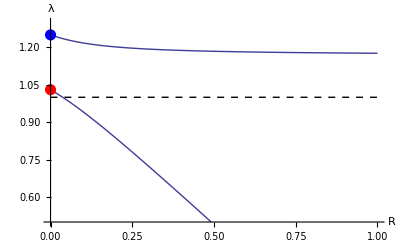

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
Factor[{λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma),λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}]
plot1=Show[
Plot[λ/.Solve[%[[1]]==0,λ],{R,0,1},PlotRange->{Automatic,{0.5,1.3}}],
ListPlot[{{0,%[[2]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,%[[3]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele a (blue) drives invasion and that invasion is possible regardless of linkage, despite the fact that the neo-W will then be further from the selected locus.

#### Example with pure sexually antagonistic selection [No haploid selection] -> neo-W invades even though R>r

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable

```mathematica
sieve[tryFAA,tryFAa,0.5,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.876289,0.855131,0.,0.5}}

{0.89344-0.932299 R-1.89629 λ+1.01326 R λ+1. λ^2,1.02255,0.87374}

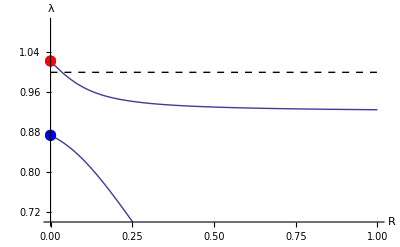

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
Factor[{λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma),λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}]

plot2=Show[
Plot[λ/.Solve[%[[1]]==0,λ],{R,0,1},PlotRange->{Automatic,{0.7,1.1}}],
ListPlot[{{0,%[[2]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,%[[3]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible only for a modest range of R values (still, R>r so this runs counter to the expectations in van Doorn and Kirkpatrick).

#### Example with pure sexually antagonistic selection with meiotic drive -> neo-W invades even though R>r

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.48;
tryαm=0.48;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.362667,0.312823,0.,0.506433}}

{0.994367-1.02231 R+2.77556×10^-17 R^2-1.99983 λ+1.07566 R λ+1. λ^2,1.07385,0.925985}

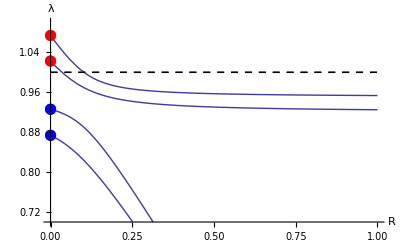

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
Factor[{λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma),λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}]

plot3=Show[
plot2,
Plot[λ/.Solve[%[[1]]==0,λ],{R,0,1},PlotRange->{Automatic,{0.7,1.1}},PlotStyle->Thick],
ListPlot[{{0,%[[2]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,%[[3]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R","λ"}
]
```

With a male biased sex ratio (thick), the eigenvalues are slight larger than with no haploid selection (thin), but the pattern is similar.

#### Letting r = R and increasing the recombination rate [No haploid selection] -> neo-W invades even though R>r

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{0.664804,0.623037,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.269049,0.204077,0.204077,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.02255,0.87374}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.87374,1.02255},{0.877268,1.02686},{0.879947,1.02901},{0.881772,1.02987},{0.882766,1.02986},{0.882963,1.02923},{0.882398,1.02816},{0.881108,1.02679},{0.879126,1.02523},{0.876489,1.02357},{0.87323,1.02187},{0.869383,1.02017},{0.864984,1.01853},{0.860067,1.01695},{0.854667,1.01546},{0.848819,1.01407},{0.842557,1.01279},{0.835912,1.0116},{0.828917,1.01052},{0.821601,1.00952},{0.813991,1.00862},{0.806112,1.0078},{0.797989,1.00706},{0.789641,1.00638},{0.781089,1.00577},{0.77235,1.00521},{0.76344,1.00471},{0.754373,1.00425},{0.745162,1.00384},{0.735819,1.00346},{0.726354,1.00312},{0.716778,1.0028},{0.707098,1.00252},{0.697322,1.00225},{0.687457,1.00202},{0.67751,1.0018},{0.667486,1.0016},{0.657391,1.00141},{0.647229,1.00124},{0.637006,1.00109},{0.626724,1.00095},{0.616387,1.00082},{0.606,1.00069},{0.595564,1.00058},{0.585083,1.00048},{0.57456,1.00038},{0.563997,1.00029},{0.553395,1.00021},{0.542758,1.00014},{0.532087,1.00007},{0.521383,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

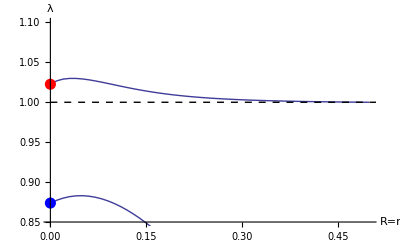

```mathematica
plot4=Show[
ListPlot[eigen1,Joined->True,PlotRange->{Automatic,{0.85,1.1}}],
ListPlot[eigen2,Joined->True],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is now possible for all R=r<1/2.

#### Letting r = R and increasing the recombination rate with meiotic drive in males -> neo-W invades even though R>r

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.48;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{0.566667,0.511278,0.,0.510429}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.155911,0.108125,0.108125,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.06485,0.898573}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.898573,1.06485},{0.900415,1.06514},{0.901889,1.06428},{0.902922,1.06264},{0.903481,1.06044},{0.903554,1.05783},{0.903135,1.05492},{0.902222,1.05182},{0.900813,1.0486},{0.898908,1.04533},{0.896508,1.04206},{0.893613,1.03885},{0.890228,1.03574},{0.886359,1.03275},{0.882016,1.02992},{0.877211,1.02726},{0.871962,1.02478},{0.866287,1.02248},{0.860208,1.02036},{0.853747,1.01842},{0.84693,1.01664},{0.83978,1.01503},{0.832321,1.01356},{0.824576,1.01224},{0.816567,1.01103},{0.808314,1.00994},{0.799837,1.00896},{0.791154,1.00806},{0.782281,1.00725},{0.773233,1.00652},{0.764023,1.00586},{0.754663,1.00525},{0.745165,1.0047},{0.735539,1.0042},{0.725795,1.00375},{0.715939,1.00333},{0.705981,1.00295},{0.695927,1.00261},{0.685783,1.00229},{0.675554,1.002},{0.665247,1.00174},{0.654866,1.00149},{0.644415,1.00127},{0.633899,1.00106},{0.62332,1.00087},{0.612683,1.00069},{0.60199,1.00053},{0.591245,1.00038},{0.58045,1.00025},{0.569608,1.00012},{0.55872,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

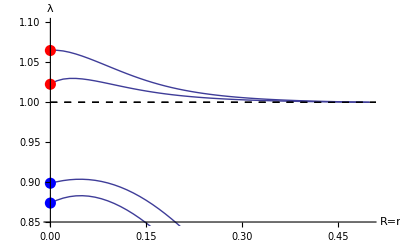

```mathematica
plot5=Show[
plot4,
ListPlot[eigen1,Joined->True,PlotRange->{Automatic,{0.85,1.1}},PlotStyle->Thick],
ListPlot[eigen2,Joined->True,PlotStyle->Thick],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is now possible for all R=r<1/2.

#### Letting r = R and increasing the recombination rate with meiotic drive in females -> neo-W invades even though R>r

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.52;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{0.873743,0.852223,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.421524,0.332718,0.332718,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.01701,0.852685}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.852685,1.01701},{0.853802,1.02448},{0.854965,1.02736},{0.855586,1.02862},{0.855552,1.02895},{0.854834,1.02865},{0.853437,1.02792},{0.851379,1.0269},{0.848689,1.02568},{0.8454,1.02435},{0.841545,1.02295},{0.83716,1.02153},{0.832281,1.02012},{0.826942,1.01875},{0.821178,1.01743},{0.815021,1.01617},{0.808502,1.01498},{0.801651,1.01386},{0.794494,1.01281},{0.787058,1.01183},{0.779366,1.01092},{0.771439,1.01007},{0.763298,1.00928},{0.754961,1.00855},{0.746445,1.00787},{0.737764,1.00724},{0.728932,1.00666},{0.719961,1.00611},{0.710863,1.00561},{0.701649,1.00514},{0.692326,1.00471},{0.682904,1.0043},{0.673391,1.00392},{0.663792,1.00357},{0.654115,1.00324},{0.644366,1.00293},{0.634548,1.00264},{0.624667,1.00237},{0.614728,1.00212},{0.604735,1.00188},{0.59469,1.00166},{0.584598,1.00144},{0.574461,1.00125},{0.564282,1.00106},{0.554064,1.00088},{0.54381,1.00071},{0.53352,1.00055},{0.523198,1.0004},{0.512845,1.00026},{0.502464,1.00013},{0.492055,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

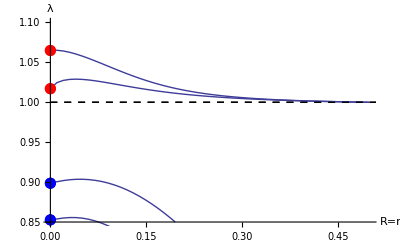

```mathematica
plot6=Show[
plot5,
ListPlot[eigen1,Joined->True,PlotStyle->Thick],
ListPlot[eigen2,Joined->True,PlotStyle->Thick],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

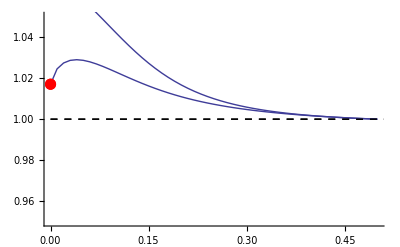

```mathematica
Show[%,PlotRange->{{0,0.5},{0.95,1.05}}]
```

These converge with increasing recombination rate.

$Aborted